# Supplementary Information for Leveraging Pre-Vaccination Antibody Titers across Multiple Influenza H3N2 Variants to Forecast the Post-Vaccination Response

The following code reproduces the plots in the main text. Made on Mathematica version 14.0.0 for Windows. Sections can be opened by mouse click.

Raw data can be found in these initialization sections.

## Figures

### Figure 1: Characteristics of the Vaccine Responses

This figure computes basic statistics about each person’s post-vaccination HAI against the vaccine strain and shows that their behavior in a prior season predicts their behavior in the following season.

#### Panel A: Examples of Strong and Weak Responses

Examples of pre- and post-vaccination HAI from two individuals in the 2016 Fox Health Care Worker (HCW) dataset.

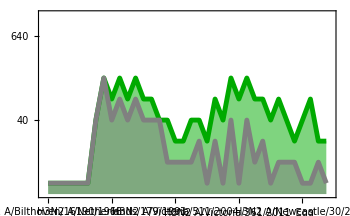
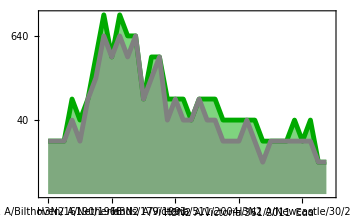

```mathematica
tableOfInterest="Fox2022HCW";
listViruses=Cases[viruses[tableOfInterest],virus_/;virusSubtype@virus=="H3N2"];
Table[
preVac=MapIndexed[{First@#2,data[{#,serum,"Day0"}]}&,listViruses];
postVac=MapIndexed[{First@#2,data[{#,serum,"Day28"}]}&,listViruses]/.dat_data:>fixTimes@dat;

Show[
ListPlot[{postVac,preVac},Joined->{True,True},Frame->{True,True,False,False},FrameTicks->{MapIndexed[{First@#2,Rotate[font[#,10],π/2],0.015}&,listViruses],Table[{5 2^(j-1),If[EvenQ@j,5 2^(j-1),""],0.02 If[EvenQ@j,1,2/3]},{j,0,10}]},FrameTicksStyle->14,FrameStyle->Directive[{Black,Thickness[0.004]}],PlotStyle->{Directive[Darker@Green,Thickness[0.01]],Directive[Gray,Thickness[0.01]]},Filling->{1->Bottom,2->Bottom,3->{1}},FillingStyle->Opacity[0.5],ScalingFunctions->"Log",PlotRange->{{0.5,Length@listViruses+0.5},{3.5,1300}},ImageSize->350,PlotRangeClipping->False]
]
,{serum,{"RMH0069_Fox2022","RMH0117_Fox2022"}}]
```

#### Panel B: Strength of Response

Distribution of post-vaccination HAI for the vaccine strain across all studies.

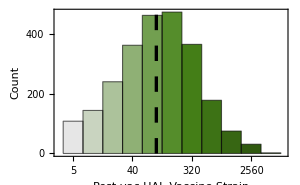

```mathematica
dist=DeleteMissing[Join@@Table[
vaccine=assocVaccineStrain[tableOfInterest];
Table[
{serum,data[{vaccine,serum,"Day28"}]/.dat_data:>fixTimes@dat}
,{serum,sera[tableOfInterest]}]
,{tableOfInterest,Join@@listCohortsInitial}],1,All];
mean=Log10[GeometricMean[Last/@dist]];
plotData=GatherBy[Sort@Log10[Last/@dist],#&];
Histogram[plotData,{Table[Log10[5]-Log10[2.]/2+jj Log10[2.],{jj,-2,12}]},PlotRange->{{Log10[3.],3.9},All},Frame->{True,True,False,False},FrameLabel->(font[#,14]&/@{"Post-vac HAI, Vaccine Strain","Count"}),FrameTicks->{Table[{Log10[5 2^jj],Row[{5 2^jj}]},{jj,0,10}],},FrameTicksStyle->12,FrameStyle->Directive[Black,Thickness[0.002]],ImageSize->300,Epilog->{Dashing[0.037],Thickness[0.008],Line[{{mean,0},{mean,700}}]},ChartStyle->(Blend[{GrayLevel[0.9],RGBColor[0.2784312712368802, 0.5176471006103812, 0.09411754367367867],Darker[RGBColor[0.2784312712368802, 0.5176471006103812, 0.09411754367367867],0.5]},#]&/@Subdivide[Length@plotData-1]),ChartBaseStyle->Directive[{EdgeForm[Black],Opacity[1]}]]
```

#### Panels C,D: Inertia of Response

Panel C: For participants vaccinated two seasons in a row between 2016-2021, how does their post-vaccination HAI in the prior season compare to their post-vaccination HAI in the next season?

Subjects are always compared against the vaccine strain from a given season. For example, a subject participating in 2017 and 2018 will be evaluated based on their post-vac HAI against H3N2 A/Hong Kong/4801/2014 in 2016 and against H3N2 A/Singapore/INFIMH-160019/2016 in 2017

We coarsely classify a post-vaccination response as strong if HAI≥80 against that season’s vaccine strain and weak if HAI<80

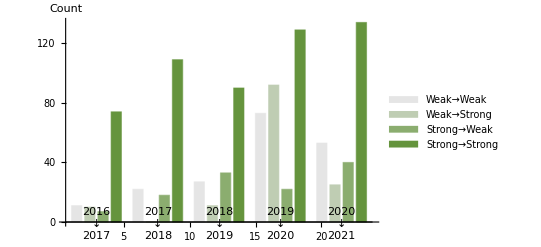

```mathematica
(* HAI post-vac against {this season's, next season's} vaccine strain for each year *)
plotDataFull=Table[
currentSeason="UGA"<>ToString@year;
nextSeason="UGA"<>ToString[year+1];
Cases[sera[currentSeason],serum_/;MemberQ[sera[nextSeason],StringReplace[serum,currentSeason->nextSeason]]:>{data[{assocVaccineStrain[currentSeason],serum,"Day28"}],data[{assocVaccineStrain[nextSeason],StringReplace[serum,currentSeason->nextSeason],"Day28"}]}/.dat_data:>fixTimes@dat]
,{year,2016,2020}];
(* Categorize vaccine potency in each year *)
plotData=Length/@{(* {Weak, Weak} *)Cases[#,{val1_,val2_}/;val1<80&&val2<80],
(* {Weak, Strong} *)Cases[#,{val1_,val2_}/;val1<80&&val2>=80],
(* {Strong, Weak} *)Cases[#,{val1_,val2_}/;val1>=80&&val2<80],
(* {Strong, Strong} *)Cases[#,{val1_,val2_}/;val1>=80&&val2>=80]}&/@plotDataFull;
BarChart[plotData,ChartStyle->{RGBColor[0.8980393195876737, 0.898039319587674, 0.8980393195876738],RGBColor[0.7474510692087118, 0.8033333957341603, 0.700392235894653],RGBColor[0.546666735370096, 0.6770588305961421, 0.4368627909706255],RGBColor[0.39607848499113407, 0.5823529067426284, 0.23921570727760477]},Ticks->{Automatic,},TicksStyle->13,AxesStyle->Directive[Black,Thickness[0.002]],AxesLabel->font["Count",14],ChartLabels->{Column[{#,"↓",#+1},Alignment->Center]&/@Range[2016,2020],None},ChartLegends->Placed[font/@{"Weak→Weak","Weak→Strong","Strong→Weak","Strong→Strong"},Scaled[{{0.2,0.8},{0.5,0.5}}]]]
```

Panel D: Statistics on what fraction of individuals are strong/weak in each season, and how many of these stay/change in the following season.

```mathematica
nStrong=Length@Cases[Join@@(First/@#&/@plotDataFull),val_/;val>=80];
nWeak=Length@Cases[Join@@(First/@#&/@plotDataFull),val_/;val<80];
Echo[Round[100{nStrong,nWeak}/(nStrong+nWeak)],"% {Strong, Weak} response in any season:"];
```

% {Strong, Weak} response in any season:  {67,33}

```mathematica
{nWeakWeak,nWeakStrong,nStrongWeak,nStrongStrong}=Total/@Transpose[plotData];
Echo[{Row[{"Strong→Strong: ",Round[100 nStrongStrong/(nStrongStrong+nStrongWeak)]}],Row[{"Strong→Weak: ",Round[100 nStrongWeak/(nStrongStrong+nStrongWeak)]}]},"% of Strong splits:"];
Echo[{Row[{"Weak→Strong: ",Round[100 nWeakStrong/(nWeakStrong+nWeakWeak)]}],Row[{"Weak→Weak: ",Round[100 nWeakWeak/(nWeakStrong+nWeakWeak)]}]},"% Weak splits:"];
```

% of Strong splits:  {Strong→Strong: 82,Strong→Weak: 18}

% Weak splits:  {Weak→Strong: 43,Weak→Weak: 57}

### Figure 2: Features that Determine the Response

For all pairs of vaccinees that have the same subset of features pre-vaccination (e.g. similar age, sex, pre-vaccination HAI... or any combination thereof), how similar will their responses be post-vaccination? In particular, we examine:

Age: ≤10 years apart in age

Sex: Must have the same sex

BMI: Have similar BMI (bin=2)

```mathematica
(*Histogram[Flatten@DeleteMissing[Table[
Replace[BMI[#],{val_?NumericQ:>Round@val,_BMI:>Missing[]}]&/@sera[cohort]
,{cohort,Flatten[listCohortsInitial]}],2],{2}]*)
```

Date Vaccinated: Vaccinated at the same time (bin=14 days)

Since most people get vaccinated in the fall, defining the day of the year as Dec 31→365, Jan 1→366 days, Jan 2→367... for continuity.

```mathematica
(*Histogram[Flatten@DeleteMissing[Table[
Replace[dateVaccine[#],{date_DateObject:>(date["DayOfYear"]/.val_/;val<100:>val+365),_dateVaccine:>Missing[]}]&/@sera[cohort]
,{cohort,Flatten[listCohortsInitial]}],2],{14}]*)
```

Vaccine dose: Standard vs high dose (the latter is only available for age≥65 in the UGA Fluzone studies

Location: Studies occurred in the same location

Pre-vac HAI against the vaccine strain: Must have the same HAI

Pre-vac HAI against variants: Have ≥5 overlapping variants variants, and the HAIs against these overlapping variants have ≥90% correlation

#### Panel A: Quantifying Feature Importance

Assessing different combination of pre-vac features. Given our ultimate goal to use past data to predict responses in future seasons, we only consider pairs given the vaccine in different seasons (and consider each person’s post-vac HAI against their vaccine strain).

```mathematica
(* Characterize the feature set for each vaccinee *)
response=Association@Table[
Table[
serum->Association@{
"Variants"->Association@Table[aliasBest[virus]->(If[NumericQ@#,Log10@#,Missing[]]&[data[{virus,serum,"Day0"}]]),{virus,Cases[viruses[cohort],virus_/;virusSubtype@virus=="H3N2"&&!MatchQ[virus,assocVaccineStrain@cohort]]}],
"Age"->If[MatchQ[#,_age],Missing[],#]&@age[serum],
"Sex"->If[MatchQ[#,_sex],Missing[],#]&@sex[serum],
"BMI"->If[MatchQ[#,_BMI],Missing[],Round@#]&@BMI[serum],
"Location"->Replace[cohort,{"Fonville2014_S5"|"Fonville2014_S6"|"Fonville2014_S13"|"Fonville2014_S14"|"Fox2022HCW":>"Australia","Fox2022HaNam":>"Ha Nam","Hinojosa2020_V2014-2015"|"Hinojosa2020_V2015"|"Hinojosa2020_U2015":>"Wisconsin","UGA2016"|"UGA2017"|"UGA2018"|"UGA2019"|"UGA2020"|"UGA2021":>"Georgia"}],
"DateVaccine"->Replace[dateVaccine[serum],{
(* Roll over anyone getting vaccinated past Jan 1 to make days continuous *)
date_DateObject:>(date["DayOfYear"]/.val_/;val<100:>val+365),
_dateVaccine:>Missing[]}],
"DoseVaccine"->Replace[vaccineDose[serum],{_vaccineDose:>Missing[]}],
"VaccinePre"->(If[NumericQ@#,Log10@#,Missing[]]&[data[{assocVaccineStrain@cohort,serum,"Day0"}]]),"VaccinePost"->(If[NumericQ@#,Log10@#,Missing[]]&[data[{assocVaccineStrain@cohort,serum,"Day28"}]/.dat_data:>fixTimes@dat])
}
,{serum,sera[cohort]}]
,{cohort,Flatten[listCohortsInitial]}]/.dat_data:>fixTimes@dat;
(* Only examine cases where the post-vac HAI is available *)
response=DeleteCases[response,entry_/;MissingQ@entry["VaccinePost"]];
```

Find pairs of subjects that match on different feature sets.

```mathematica
Clear[pairs]
```

```mathematica
pairs[{"VaccinePre"}]=Block[{pos,tablesPredictingFrom,vals},Flatten[Table[
pos=Position[listCohortsInitial,tableToPredict][[1,1]];
tablesPredictingFrom=Join@@listCohortsInitial[[1;;pos-1]];
Table[
Cases[Tuples[{sera[tablePredictingFrom],sera[tableToPredict]}],pair_/;(
(* Check for two Missings canceling each other out *)
vals={response[First@pair]["VaccinePre"],response[Last@pair]["VaccinePre"]};
MatchQ[vals,{_?NumericQ..}]&&Abs[Subtract@@vals]<=0.5 Log10[2.]
)]
,{tablePredictingFrom,tablesPredictingFrom}]
,{tableToPredict,Flatten[listCohortsInitial]}],2]
];
```

```mathematica
pairs[{"VaccinePre","Variants"}]=Block[{v1,v2,overlapViruses,vals},
Cases[pairs[{"VaccinePre"}],pair_/;(
{v1,v2}=(response[#]["Variants"]&/@pair);
overlapViruses=Intersection@@Keys/@{v1,v2};
vals={v1/@overlapViruses,v2/@overlapViruses};
vals=DeleteMissing[valsᵀ,1,All]ᵀ;
(* ≥5 overlapping viruses (excluding vaccine strains) with correlation>0.9 *)
(Length@overlapViruses>=5)&&(Length@First@vals>1)&&TrueQ[Min[StandardDeviation/@vals]>10^-6.]&&(Correlation@@vals>0.9)
)]
];
```

```mathematica
pairs[{"Age"}]=Block[{pos,tablesPredictingFrom,vals},Flatten[Table[
pos=Position[listCohortsInitial,tableToPredict][[1,1]];
tablesPredictingFrom=Join@@listCohortsInitial[[1;;pos-1]];
Table[
Cases[Tuples[{sera[tablePredictingFrom],sera[tableToPredict]}],pair_/;(
(* Check for two Missings canceling each other out *)
vals={response[First@pair]["Age"],response[Last@pair]["Age"]};
MatchQ[vals,{_?NumericQ..}]&&TrueQ[Abs[Subtract@@vals]<=10.]
)]
,{tablePredictingFrom,tablesPredictingFrom}]
,{tableToPredict,Flatten[listCohortsInitial]}],2]
];
```

```mathematica
pairs[{"Sex"}]=Block[{pos,tablesPredictingFrom,vals},Flatten[Table[
pos=Position[listCohortsInitial,tableToPredict][[1,1]];
tablesPredictingFrom=Join@@listCohortsInitial[[1;;pos-1]];
Table[
Cases[Tuples[{sera[tablePredictingFrom],sera[tableToPredict]}],pair_/;(
(* Check for two Missings canceling each other out *)
vals={response[First@pair]["Sex"],response[Last@pair]["Sex"]};
MatchQ[vals,{_String..}]&&Equal@@vals
)]
,{tablePredictingFrom,tablesPredictingFrom}]
,{tableToPredict,Flatten[listCohortsInitial]}],2]
];
```

```mathematica
pairs[{"BMI"}]=Block[{pos,tablesPredictingFrom,vals},Flatten[Table[
pos=Position[listCohortsInitial,tableToPredict][[1,1]];
tablesPredictingFrom=Join@@listCohortsInitial[[1;;pos-1]];
Table[
Cases[Tuples[{sera[tablePredictingFrom],sera[tableToPredict]}],pair_/;(
(* Check for two Missings canceling each other out *)
vals={response[First@pair]["BMI"],response[Last@pair]["BMI"]};
MatchQ[vals,{_?NumericQ..}]&&TrueQ[Abs[Subtract@@vals]<=2.]
)]
,{tablePredictingFrom,tablesPredictingFrom}]
,{tableToPredict,Flatten[listCohortsInitial]}],2]
];
```

```mathematica
pairs[{"DateVaccine"}]=Block[{pos,tablesPredictingFrom,vals},Flatten[Table[
pos=Position[listCohortsInitial,tableToPredict][[1,1]];
tablesPredictingFrom=Join@@listCohortsInitial[[1;;pos-1]];
Table[
Cases[Tuples[{sera[tablePredictingFrom],sera[tableToPredict]}],pair_/;(
(* Check for two Missings canceling each other out *)
vals={response[First@pair]["DateVaccine"],response[Last@pair]["DateVaccine"]};
MatchQ[vals,{_?NumericQ..}]&&TrueQ[Abs[Subtract@@vals]<=14.]
)]
,{tablePredictingFrom,tablesPredictingFrom}]
,{tableToPredict,Flatten[listCohortsInitial]}],2]
];
```

```mathematica
pairs[{"DoseVaccine"}]=Block[{pos,tablesPredictingFrom,vals},Flatten[Table[
pos=Position[listCohortsInitial,tableToPredict][[1,1]];
tablesPredictingFrom=Join@@listCohortsInitial[[1;;pos-1]];
Table[
Cases[Tuples[{sera[tablePredictingFrom],sera[tableToPredict]}],pair_/;(
(* Check for two Missings canceling each other out *)
vals={response[First@pair]["DoseVaccine"],response[Last@pair]["DoseVaccine"]};
MatchQ[vals,{_String..}]&&Equal@@vals
)]
,{tablePredictingFrom,tablesPredictingFrom}]
,{tableToPredict,Flatten[listCohortsInitial]}],2]
];
```

```mathematica
pairs[{"Location"}]=Block[{pos,tablesPredictingFrom,vals},Flatten[Table[
pos=Position[listCohortsInitial,tableToPredict][[1,1]];
tablesPredictingFrom=Join@@listCohortsInitial[[1;;pos-1]];
Table[
Cases[Tuples[{sera[tablePredictingFrom],sera[tableToPredict]}],pair_/;(
(* Check for two Missings canceling each other out *)
vals={response[First@pair]["Location"],response[Last@pair]["Location"]};
MatchQ[vals,{_String..}]&&Equal@@vals
)]
,{tablePredictingFrom,tablesPredictingFrom}]
,{tableToPredict,Flatten[listCohortsInitial]}],2]
];
```

```mathematica
(* Adding on these features to other feature sets *)
pairs[{features__,"Age"}]:=pairs[{features,"Age"}]=Block[{vals},
Cases[pairs[{features}],pair_/;(
(* Check for two Missings canceling each other out *)
vals={response[First@pair]["Age"],response[Last@pair]["Age"]};
MatchQ[vals,{_?NumericQ..}]&&TrueQ[Abs[Subtract@@vals]<=10.]
)]
];
pairs[{features__,"Sex"}]:=pairs[{features,"Sex"}]=Block[{vals},
Cases[pairs[{features}],pair_/;(
(* Check for two Missings canceling each other out *)
vals={response[First@pair]["Sex"],response[Last@pair]["Sex"]};
MatchQ[vals,{_String..}]&&Equal@@vals
)]
];
pairs[{features__,"BMI"}]:=pairs[{features,"BMI"}]=Block[{vals},
Cases[pairs[{features}],pair_/;(
(* Check for two Missings canceling each other out *)
vals={response[First@pair]["BMI"],response[Last@pair]["BMI"]};
MatchQ[vals,{_?NumericQ..}]&&TrueQ[Abs[Subtract@@vals]<=2.]
)]
];
pairs[{features__,"DateVaccine"}]:=pairs[{features,"DateVaccine"}]=Block[{vals},
Cases[pairs[{features}],pair_/;(
(* Check for two Missings canceling each other out *)
vals={response[First@pair]["DateVaccine"],response[Last@pair]["DateVaccine"]};
MatchQ[vals,{_?NumericQ..}]&&TrueQ[Abs[Subtract@@vals]<=14.]
)]
];
pairs[{features__,"DoseVaccine"}]:=pairs[{features,"DoseVaccine"}]=Block[{vals},
Cases[pairs[{features}],pair_/;(
(* Check for two Missings canceling each other out *)
vals={response[First@pair]["DoseVaccine"],response[Last@pair]["DoseVaccine"]};
MatchQ[vals,{_String..}]&&Equal@@vals
)]
];
pairs[{features__,"Location"}]:=pairs[{features,"Location"}]=Block[{vals},
Cases[pairs[{features}],pair_/;(
(* Check for two Missings canceling each other out *)
vals={response[First@pair]["Location"],response[Last@pair]["Location"]};
MatchQ[vals,{_String..}]&&Equal@@vals
)]
];
```

Plot the predictive power of different combinations of features.

```mathematica
featuresList={
{"Age"},
{"Sex"},
{"BMI"},
{"DateVaccine"},
{"DoseVaccine"},
{"Location"},

{"VaccinePre"},
{"VaccinePre","Age"},
{"VaccinePre","Sex"},
{"VaccinePre","BMI"},
{"VaccinePre","DateVaccine"},
{"VaccinePre","DoseVaccine"},
{"VaccinePre","Location"},

{"VaccinePre","Variants"},
{"VaccinePre","Variants","Age"},
{"VaccinePre","Variants","Sex"},
{"VaccinePre","Variants","BMI"},
{"VaccinePre","Variants","DateVaccine"},
{"VaccinePre","Variants","DoseVaccine"},
{"VaccinePre","Variants","Location"}
};
(* Number of studies that the pairs span for each feature. When this is only 1, you may have an artificially low RMSE because you are within one superset *)
numStudies=Table[
Total[Boole@ContainsAny[sera[#],Flatten@pairs[features]]&/@{"UGA","Fox2022","Fonville2014","Hinojosa2020"}]
,{features,featuresList}];
Clear[rmse]
rmse[features_List]:=Block[{plotData},
10^RootMeanSquare[Subtract@@@DeleteMissing[Map[response[#]["VaccinePost"]&,pairs[features],{2}],1,All]]
]
plotDataRMSE=MapIndexed[{First@#2,rmse[#]}&,featuresList];
```

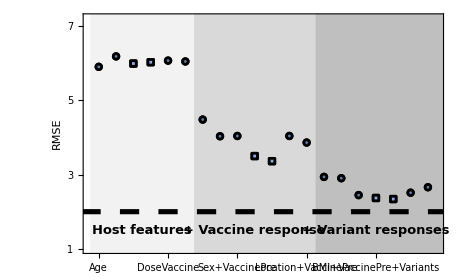

```mathematica
(* Plotting *)
frameTicks=MapIndexed[{First@#2,Rotate[Style[font@Total@#,If[numStudies[[First@#2]]==1,
(* If all pairs are from UGA studies *)
RGBColor[0.5477240862612718, 0.6781403431438215, 0.9198750056398158],
(* Features whose statistics derive from ≥2 data supersets (i.e. more than just UGA) *)
Black
]],π/2],0.015}&,featuresList];
ListPlot[List/@plotDataRMSE,Frame->{True,True,False,False},PlotRange->{{0.5,Length@plotDataRMSE+0.5},{1,7.2}},FrameTicks->{frameTicks,},Epilog->{Black,Dashing[0.03],Thickness[0.008],Line[{{0,2},{30,2}}],
Text[font["Host features",Bold,13],{3.5,1.5}],
Text[font["+ Vaccine response",Bold,13],{10,1.5}],
Text[font["+ Variant responses",Bold,13],{17,1.5}]},Prolog->{{GrayLevel[0.95],Rectangle[{0.5,0.5},{6.5,8}]},{GrayLevel[0.85],Rectangle[{6.5,0.5},{13.5,8}]},{GrayLevel[0.75],Rectangle[{13.5,0.5},{23.5,8}]}},PlotMarkers->ReplacePart[ConstantArray[plotMarker[0.04,"EdgeThickness"->0.1],Length@featuresList],Position[numStudies,1]->plotMarker[0.043,"Type"->"Square","EdgeThickness"->0.1]],PlotStyle->ReplacePart[ConstantArray[ColorData[97,1],Length@featuresList],Position[numStudies,1]->RGBColor[0.5477240862612718, 0.6781403431438215, 0.9198750056398158]],FrameLabel->font["RMSE",16],FrameStyle->Directive[Black,Thickness[0.002]],FrameTicksStyle->14,AspectRatio->0.6]
```

```mathematica
numDatasets=Table[Total[Boole@ContainsAny[sera[#],Flatten@pairs[features]]&/@Flatten[listCohortsInitial]],{features,featuresList}];
showGrid[Prepend[Transpose@{font/@Total/@featuresList,numDatasets,numStudies,Length/@pairs/@featuresList},{"Features","# Datasets","# Supersets","n Measurements"}],"Header"->"TopLeft"]
```

Features | # Datasets | # Supersets | n Measurements
Age | 13 | 4 | 676081
Sex | 8 | 2 | 815767
BMI | 5 | 1 | 254499
DateVaccine | 6 | 1 | 303004
DoseVaccine | 8 | 2 | 1230140
Location | 14 | 4 | 1404421
VaccinePre | 15 | 4 | 369658
Age+VaccinePre | 13 | 4 | 106897
Sex+VaccinePre | 8 | 2 | 111264
BMI+VaccinePre | 5 | 1 | 34511
DateVaccine+VaccinePre | 6 | 1 | 40269
DoseVaccine+VaccinePre | 8 | 2 | 169140
Location+VaccinePre | 14 | 4 | 199739
VaccinePre+Variants | 14 | 4 | 5134
Age+VaccinePre+Variants | 12 | 4 | 2546
Sex+VaccinePre+Variants | 7 | 2 | 1768
BMI+VaccinePre+Variants | 4 | 1 | 708
DateVaccine+VaccinePre+Variants | 5 | 1 | 1165
DoseVaccine+VaccinePre+Variants | 7 | 2 | 2750
Location+VaccinePre+Variants | 13 | 4 | 3621

#### Panel B: Example Feature Sets

Plotting the predictions from four feature sets, assuming that the post-vac from vaccinee 1 is the predicted post-vac for vaccinee 2.

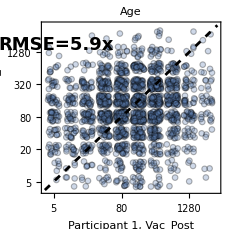
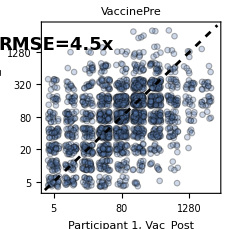
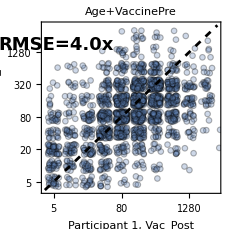
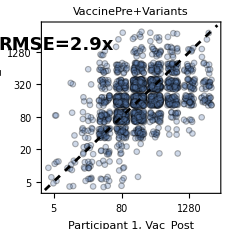

```mathematica
SeedRandom[12345];
Table[
plotData=Cases[Map[response[#]["VaccinePost"]&,pairs[feature],{2}],{_?NumericQ..}];
rmse=ToString@Round[10^RootMeanSquare[Subtract@@@plotData],0.1];
If[StringTake[rmse,-1]==".",rmse=rmse<>"0"];
epilog={Text[font[Row[{"RMSE=",rmse,"x"}],18,Bold],Log@{5.5,1800},{-1,0},Background->Directive[Opacity[0.5,White]]]};
plotData=#+RandomReal[0.1{-1,1},Dimensions@#]&[RandomSample[plotData,UpTo@2000]];
plot[10^plotData,PlotLabel->font[Total@feature,18],PlotStyle->{Opacity[0.4],PointSize[0.02]},FrameLabel->(font[#,16]&/@{"Participant 1, Vac_Post","Participant 2, Vac_Post"}),PlotMarkers->plotMarker[0.04,0.3],PlotRange->{3.5,4000},ScalingFunctions->{"Log","Log"},Epilog->epilog,FrameTicks->ConstantArray[{Table[{5 2^j,5 2^j,0.028},{j,0,9}],None},2],FrameTicksStyle->14,ImageSize->230,Frame->True,FrameStyle->Directive[Black,Thickness[0.005]]]
,{feature,{{"Age"},{"VaccinePre"},{"VaccinePre","Age"},{"VaccinePre","Variants"}}}]
```

### Figure 3: Building the Model

This figure describes the components of our modeling framework and shows some example predictions.

#### Panel A: Unifying Viruses

Since predictions were based on the HAI of overlapping variants between studies, we increased this overlap by equating variants whose HA sequences differed by ΔAAEpitope<5 amino acids in H3N2 epitopes A-E. The snippet below shows two small examples, and the full list of virus aliases is shown in Figure S3.

```mathematica
Table[
Rotate[DynamicModule[{listViruses},
listVirusCohort=Join@@(Thread[{Cases[viruses[#],virus_/;virusSubtype@virus=="H3N2"],#}]&/@Flatten@listCohortsInitial);
listVirusCohort=Cases[listVirusCohort,virusCohort_/;MemberQ[$listVirusesGlobal,First@virusCohort]];
aliases=aliasBest/@listVirusCohort;

arrows=Arrow[{{-0.5+Position[$listVirusesGlobal,#[[1]]][[1,1]],0.5+Length@Flatten@listCohortsInitial-3-Position[Flatten@listCohortsInitial,#[[2]]][[1,1]]},{-0.5+Position[$listVirusesGlobal,aliasBest@#[[1]]][[1,1]],0.5+Length@Flatten@listCohortsInitial-3-Position[Flatten@listCohortsInitial,#[[2]]][[1,1]]}}]&/@DeleteCases[listVirusCohort,virusCohort_/;virusCohort===aliasBest@virusCohort||MemberQ[viruses[Last@virusCohort],First@aliasBest@virusCohort]];

listViruses=SortBy[DeleteDuplicates[First/@listVirusCohort],virusYear];
Show[ArrayPlot[Table[
Table[
Which[
(* Measured *)
MemberQ[listVirusCohort,{virus,cohort}],1,
(* Aliased *)
!MemberQ[listVirusCohort,aliasBest@{virus,cohort}]&&MemberQ[aliases,aliasBest@{virus,cohort}],2,
(* Not measured or aliased *)
True,0
]
,{virus,$listVirusesGlobal}]
,{cohort,Flatten[listCohortsInitial][[;;-4]]}],Mesh->True,MeshStyle->Directive[Black],ColorRules->{2->Darker[RGBColor[0.92, 0.71, 0.],0.1](*RGBColor[0.9400000000000001, 0.77, 0.]*),1->RGBColor[1, 0.7866666666666667, 0.5933333333333333],0->RGBColor[0.5800000000000001, 0.6266666666666667, Rational[2, 3]]},Frame->True,FrameStyle->Directive[Black,Thickness[0.02]],PlotRangePadding->None,PlotRangeClipping->True,FrameTicks->{{None,MapIndexed[{First@#2,Rotate[font[StringRiffle[label@#," "],12],π]}&,Flatten@listCohortsInitial]},{MapIndexed[{First@#2,Rotate[font[#,12],π/2]}&,stripSubtype/@$listVirusesGlobal],None}},ImageSize->{Automatic,300}],Graphics[{Thickness[0.03],Arrowheads[0.22],arrows}]]
],-π/2]
,{$listVirusesGlobal,{{"H3N2 A/Aichi/2/1968","H3N2 A/Bilthoven/16190/1968","H3N2 A/Hong Kong/1/1968"},{"H3N2 A/Brisbane/10/2007","H3N2 A/Uruguay/716/2007","H3N2 A/Hanam/135/2008"}}}]
```

{,}

#### Panel B: Inferring Virus Relations

Examples of pairwise predictions (based only a single other study) predicting the post-vaccination HAI of H3N2 A/Uruguay/716/2007 in UGA2017.

```mathematica
{virusOfInterest,timeOfInterest,studyOfInterest}={"H3N2 A/Uruguay/716/2007","Day21","UGA2017"};
(* Find every other cohort that contains this virus-of-interest *)
listCohortsForPrediction=Cases[Flatten@listCohortsInitial,cohort_/;MemberQ[DeleteDuplicates[First/@leaveOneOut[{virusOfInterest,timeOfInterest,studyOfInterest}]],cohort]];
(* Predictions from each table *)
plotData=Table[
completionPredictions[{virusOfInterest,studyOfInterest},"OtherTables"->cohort,"Forest"->leaveOneOut,"PredictAbEvolution"->("Day21"|"Day28"->{"Day0"}),"Return"->"Titers","FoldChangeQ"->False]
,{cohort,listCohortsForPrediction}];
```

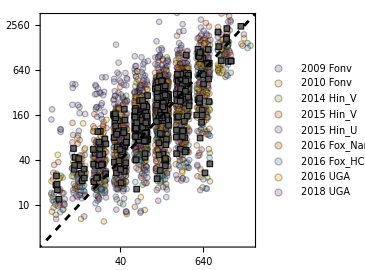

```mathematica
SeedRandom[1234];
{tick,tickFrac}={0.025,0.25};
Show[ListPlot[#+RandomReal[0.1{-1,1},Dimensions@#]&/@plotData,PlotMarkers->plotMarker[0.04,0.3],PlotRange->ConstantArray[{0.5,3.5},2],AspectRatio->1,ImageSize->270,Frame->{True,True,False,False},FrameTicks->ConstantArray[Table[{Log10[5 2^(j-1)],If[EvenQ@j,5 2^(j-1),""],0.035 If[EvenQ@j,1,2/3]},{j,0,10}],2],FrameTicksStyle->14,FrameStyle->Directive[Black,Thickness[0.002]],PlotLegends->(StringRiffle[label[#]," "]&/@listCohortsForPrediction)],ListPlot[Mean@plotData+RandomReal[0.1{-1,1},Dimensions@Mean@plotData],PlotMarkers->plotMarker[0.03,0.9,"Type"->"Square"],PlotStyle->Darker@Gray],Plot[{x},{x,0,4},PlotStyle->{Black,Dashed},PlotHighlighting->None]]
```

#### Panel C: Chord Diagram

Visualizing the accuracy of predictions between a subset of studies (full relations shown in Figure S5).

```mathematica
(* Color options *)
vacYears=virusYear/@assocVaccineStrain/@Join@@listCohortsInitial;
gradient=Blend[{Lighter[RGBColor[0.5017113270778731, 0., 0.5017113982851967],0.2],RGBColor[0.18039198677354365, 0.45882344569527705, 0.7137255033670243],RGBColor[0.4738489078908023, 0.7048888088131038, 0.3916054687399008]},#]&;
colors=gradient[Rescale[#,MinMax@vacYears,{0,1}]]&/@vacYears;
```

```mathematica
(* Chords diagram *)
Clear[showPlot]
showPlot[opacity_,connections_List:{}]:=Block[{connect,n=Length@Flatten@listCohortsInitial},
connect=ReplacePart[DiagonalMatrix[ConstantArray[1.,n-1],1],{n,1}->1.];
Do[
connect[[entry[[1]]]]=ReplacePart[ConstantArray[0,n],entry[[2]]->1];
connect[[entry[[2]]]]=ReplacePart[ConstantArray[0,n],entry[[1]]->1]
,{entry,connections}];
Show[chordDiagram[connect,"TotalWidth"->17,"Colors"->colors,"BackgroundOpacity"->opacity,"Labels"->(font[Column[label[#],Spacings->0,Alignment->Center],9]&/@Join@@listCohortsInitial)],ImageSize->350]
]
```

```mathematica
(* Mean RMSE (over all overlapping viruses) between datasets *)
Clear[meanError]
meanError[tablePredictingFrom_,tableToPredict_]:=meanError[tablePredictingFrom,tableToPredict]=Mean[Last/@virusPredict[tablePredictingFrom->tableToPredict,"Return"->"Titer"]]/._Mean:>Missing[]
```

```mathematica
(* The explicit chords shown in Fig 3C *)
entries={
{"Fonville2014_S5","Hinojosa2020_V2015"},
{"Fonville2014_S13","Hinojosa2020_U2015"},
{"Fonville2014_S14","Hinojosa2020_V2014-2015"},
{"Fox2022HCW","UGA2018"},
{"Fox2022HaNam","UGA2016"},
{"UGA2017","UGA2019"},
{"UGA2020","UGA2021"}
};
(* Calculating mean RMSE, making it symmetric (representing predictions in either direction) *)
transparency=ConstantArray[0,{#,#}&@Length@Flatten@listCohortsInitial];
Do[
{tablePredictingFrom,tableToPredict}=entry[[;;2]];
{j,k}=Flatten@Position[Flatten@listCohortsInitial,tablePredictingFrom|tableToPredict];
transparency[[j,k]]=transparency[[k,j]]=1/2(meanError[tablePredictingFrom,tableToPredict]+meanError[tableToPredict,tablePredictingFrom])
,{entry,entries}];
transparency=transparency/.{0->0,val_?NumericQ:>(2/val)^2,_Missing->0};
(* Chord diagram *)
showPlot[transparency,Map[Position[Flatten@listCohortsInitial,#][[1,1]]&,entries[[All,;;2]],{2}]]
```

-Graphics-

#### Panel D: Error vs Prior Years Trained Upon

Predicting each study by training on all studies from the past n years.

Calculate prediction accuracy for every dataset using every possible n. For speed, the code is commented and the results are canned below

```mathematica
(*(* Remove 2015 Subscript[Hinojosa, U] with its singular infection history *)
listDatasetsNoHinU=DeleteCases[listCohortsInitial,"Hinojosa2020_U2015",2];
plotData=Table[
res=Table[
{studyYear[tableToPredict]-predictingSince,trainingSet=Cases[Flatten@listDatasetsNoHinU,study_/;predictingSince<=studyYear[study]<=studyYear[tableToPredict]-1];
(* Make sure there is at least one study from exactly 'nPriorSeasons' *)
If[Min[studyYear/@trainingSet]===predictingSince,
virusPredict[trainingSet->tableToPredict,"Return"->"Titer","Forest"->leaveOneOut],
Missing[]
]}
,{predictingSince,1997,studyYear[tableToPredict]-1}]
,{tableToPredict,Flatten[listDatasetsNoHinU]}];
plotData=DeleteMissing[plotData,2,All];
plotDataFull=MapAt[Mean[#[[All,-1]]]&,plotData,{All,All,2}];
Iconize[plotDataFull]*)
plotDataFull=;
```

Show prediction accuracy along with an interpolation line to visualize the trend as a function of n

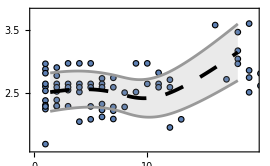

```mathematica
(* Binning the results for interpolation. There are few values with very large n≥20, so we ignore that regime that clearly goes back too far *)
vals=DeleteCases[Join@@plotDataFull,{n_,_}/;n>=20];
vals=N@SortBy[GatherBy[vals,Which[
#[[1]]<=2,1,
#[[1]]<=5,2,
#[[1]]<=10,3,
#[[1]]<=15,4,
#[[1]]<=20,5,
True,6
]&],#[[1,1]]&];
Show[ListPlot[Join@@plotDataFull,PlotStyle->ColorData[97,1],PlotMarkers->plotMarker[0.055,"EdgeThickness"->Small],PlotRange->{{0,19.5},{1.6,3.8}},Frame->{True,True,False,False},FrameTicks->,FrameStyle->Directive[Black,Thickness[0.0023]],FrameTicksStyle->14,ImageSize->270],ListPlot[{{Mean@#[[All,1]],Mean@#[[All,2]]-StandardDeviation@#[[All,2]]}&/@vals,{Mean@#[[All,1]],Mean@#[[All,2]]}&/@vals,{Mean@#[[All,1]],Mean@#[[All,2]]+StandardDeviation@#[[All,2]]}&/@vals},PlotStyle->{GrayLevel[0.6],Directive[Thickness[0.01],Black,Dashing[Large]],GrayLevel[0.6]},Filling->{1->{3}},Joined->True,InterpolationOrder->3]]
```

#### Panel E: Example Serum Predictions in 2017 UGA

Predicting 5 (out of 271) serum responses from 2017 UGA.

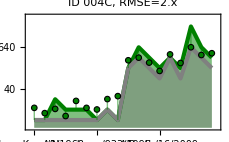
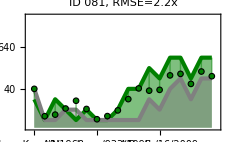
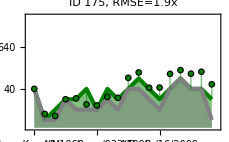
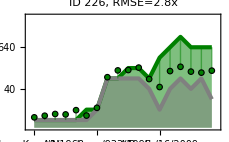
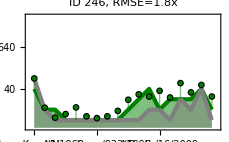

```mathematica
tableToPredict="UGA2017";
(* Train upon all studies from the past 10 year *)
tablesPredictingFrom=Cases[Join@@listCohortsFinal,cohort_/;1<=studyYear[tableToPredict]-studyYear[cohort]<=10];
(* Five example sera from 2017 UGA to predict *)
listSera={"ID_004C_UGA2017","ID_081_UGA2017","ID_175_UGA2017","ID_226_UGA2017","ID_246_UGA2017"};
Table[
Show[showLandscape[serumOfInterest,tableToPredict,"PostVacPredict"->predictOneIndividual[tablesPredictingFrom->tableToPredict,serumOfInterest,"IncludeVirusNames"->True],"FrameTicksSize"->12,"PlotMarkerSize"->0.05,"PlotMarkerEdgeThickness"->Small][[1]]/.Thickness[0.01]->Thickness[0.013],PlotLabel->font[Row[{"ID "<>StringSplit[serumOfInterest,"_"][[2]],", RMSE=",rmse,"x"}],16],FrameTicksStyle->12,FrameStyle->Directive[Black,Thickness[0.002]],FrameLabel->None]
,{serumOfInterest,listSera}]/."A/Hong Kong/4801/2014"->Sequence@@{"A/Hong Kong/4801/2014",RGBColor[0.498039131762729, 1.380902197214637*^-7, 0.4980391892092125]}
```

#### Panel F: Example Virus Predictions in 2017 UGA

Predicting responses against 4 (out of 18) viruses from 2017 UGA.

```mathematica
virusIndex={1,9,11,17};
plots=virusPredict[tablesPredictingFrom->tableToPredict,"PlotType"->"Jittered",PlotMarkers->plotMarker[0.04,0.9,"EdgeThickness"->0.05]];
labels=virusPredict[tablesPredictingFrom->tableToPredict,"Return"->"Titer"][[virusIndex]];
```

```mathematica
Show[#[[1]],PlotLabel->font[Row[{stripSubtype@virusNameYear@#[[2,1]],", RMSE=",#[[2,2]],If[StringTake[ToString@#[[2,2]],-1]==".","0",""],"x"}],12],PlotRange->ConstantArray[Log10@{4,3000},2],FrameTicks->ConstantArray[Table[{Log10[5 2^(j-1)],If[EvenQ@j,5 2^(j-1),""],0.035 If[EvenQ@j,1,2/3]},{j,0,10}],2],FrameLabel->(font/@{"Measured HAI","Predicted HAI"}),FrameStyle->Directive[Black,Thickness[0.003]]]&/@Transpose@{Flatten[plots[[1,1]]][[virusIndex]],labels}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### Panel G: Random Forest, Null, and Linear Models in 2017 UGA

Assessing the random forest model against all variants in 2017 UGA. For comparison, we also use a null model (assuming no HAI response) and a linear model (assuming a linear response for each variant).

```mathematica
plotDataForecast=virusPredict[tablesPredictingFrom->tableToPredict,"Method"->"Forecast","Return"->"Titer"];
plotDataNull=virusPredict[tablesPredictingFrom->tableToPredict,"Method"->"Baseline","Return"->"Titer"];
plotDataLinear=virusPredict[tablesPredictingFrom->tableToPredict,"Method"->"Linear","Return"->"Titer"];
```

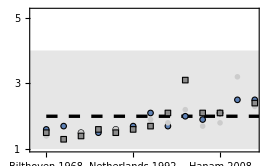

```mathematica
ListPlot[{plotDataForecast,plotDataNull,plotDataLinear}/.Thread[plotDataForecast[[All,1]]->Range@Length@plotDataForecast],PlotMarkers->{plotMarker[1.5 0.04,1,"EdgeThickness"->Small],plotMarker[1.5 0.03,1,"EdgeThickness"->Small,"Type"->"Square"],plotMarker[1.5 0.03,1,"EdgeThickness"->Small,"Type"->"Diamond"]},PlotStyle->{ColorData[97,1],GrayLevel[0.55],GrayLevel[0.8]},PlotRange->{{0.3,All},{1,5.2}},ImageSize->270,Frame->{True,True,False,False},FrameTicks->{MapIndexed[{First@#2,Rotate[font[stripSubtype@virusNameYear@#,12,If[#==="H3N2 A/Hong Kong/4801/2014",RGBColor[0.498039131762729, 1.380902197214637*^-7, 0.4980391892092125],Black]],π/2],0.015}&,plotDataForecast[[All,1]]],},Prolog->{{RGBColor[0.9019608142372235, 0.9019608142372239, 0.9019608142372235],Rectangle[{0,1},{Length@plotDataForecast+1,4}]},{Dashing[0.03],Thickness[0.009],Line[{{1,2},{Length@plotDataForecast+1,2}}]}},FrameStyle->Directive[Black,Thickness[0.002]],FrameTicksStyle->14]
```

### Figure 4: Predictions across All Studies - New, make sure this runs [it should!]

#### Panel A: Predictions Stratified by Study

```mathematica
assoc=Association@Table[
tablesPredictingFrom=Cases[Join@@listCohortsFinal,cohort_/;1<=studyYear[tableToPredict]-studyYear[cohort]<=10];
tableToPredict->virusPredict[tablesPredictingFrom->tableToPredict,"Return"->"Titer"]
,{tableToPredict,Rest@Flatten@listCohortsFinal}];
```

```mathematica
(* Master list of all viruses (aliased) predicted across all studies *)
listViruses=SortBy[DeleteDuplicates[aliasBest/@First/@Join@@Values[assoc]],virusYear];
repViruses=MapIndexed[#->First@#2&,listViruses];
```

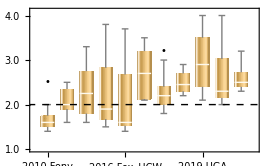

```mathematica
BoxWhiskerChart[Last/@#&/@assoc,{{"Outliers","•",Black},{"MedianMarker",Directive[Thick,Lighter[RGBColor[0.9194021976505456, 0.7566356889463239, 0.3501495412630121],0.9](*White*)]}},ChartLabels->(Rotate[font[StringRiffle[label[#]," "],14],π/2]&/@Keys@assoc),Frame->True,FrameTicks->{{LinTicks[1,4,TickLengthScale->2.5],None},Automatic},ChartElementFunction->"GlassBoxWhisker"(*,ChartStyle->RGBColor[0.9194021976505456, 0.7566356889463239, 0.3501495412630121]*),Epilog->{Black,Dashed,Line[{{0,2},{16,2}}]},FrameStyle->Directive[Black,Thickness[0.0025]],FrameTicksStyle->Directive[12,Black],ImageSize->270,PlotRange->{{0.3,11.7},{1,4.1}},PlotRangeClipping->True,PlotRangePadding->None]
```

#### Panel B: Predictions Stratified by Variant

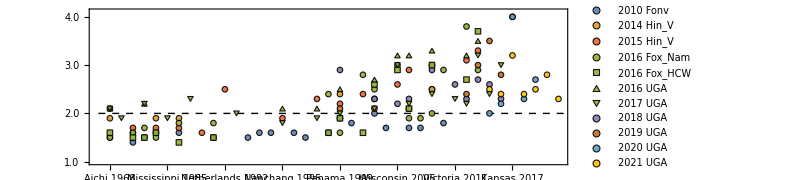

```mathematica
ListPlot[Values[assoc]/.virus_String:>(aliasBest[virus]/.repViruses),PlotMarkers->ReplacePart[ConstantArray[plotMarker[0.05,0.9,"EdgeThickness"->Small],11],{5->plotMarker[0.05,0.9,"Type"->"Square","EdgeThickness"->Small],
6->plotMarker[0.05,0.9,"Type"->"Triangle","EdgeThickness"->Small],
7->plotMarker[0.05,0.9,"Type"->"UpsideDownTriangle","EdgeThickness"->Small]}],PlotStyle->(ColorData[97]/@{1,2,4,3,3,3,3,5,6,7,8}),PlotLegends->Placed[PointLegend[Automatic,font[StringRiffle[label[#]," "],14]&/@Rest@Flatten@listCohortsFinal,LegendLayout->{"Column",3},LegendFunction->frame,Spacings->{0.4,0.2},LegendMarkerSize->8],Scaled[{{0.03,1.},{0,1}}]],PlotRange->{1,4.1},AspectRatio->0.3,PlotRangeClipping->False,ImageSize->600,Frame->{True,True,False,False},FrameTicks->{MapIndexed[{First@#2,Rotate[font[stripSubtype@virusNameYear@#,12],π/2],0.01}&,listViruses]/.{
"Perth 2009"->Style["Perth 2009",Darker[ColorData[97,1],0.1]],
"Texas 2012"->Style["Texas 2012",Darker[ColorData[97,2],0.1]],
"Switzerland 2013"->Style["Switzerland 2013",Darker[ColorData[97,4],0.1]],
"Hong Kong 2014"->Style["Hong Kong 2014",Darker[ColorData[97,3],0.1]],
"Singapore 2016"->Style["Singapore 2016",Darker[ColorData[97,5],0.1]],
"Kansas 2017"->Style["Kansas 2017",Darker[ColorData[97,6],0.1]],
"Hong Kong 2019"->Style["Hong Kong 2019",Darker[ColorData[97,7],0.1]],
"Tasmania 2020"->Style["Tasmania 2020",Darker[ColorData[97,8],0.1]]
},LinTicks[1,4,TickLengthScale->1.3]},FrameStyle->Directive[Black,Thickness[0.0012]],FrameTicksStyle->Directive[13,Black],Prolog->{{Dashed,Line[{{0.,2},{50,2}}]}}]
```

#### Panel C: Predictions Stratified by Age

```mathematica
assocAge=Association@Table[
tablesPredictingFrom=Cases[Join@@listCohortsFinal,cohort_/;1<=studyYear[tableToPredict]-studyYear[cohort]<=10];
tableToPredict->virusPredict[tablesPredictingFrom->tableToPredict,"Return"->"TiterFull"]
,{tableToPredict,Rest[Flatten@listCohortsFinal][[;;]]}];
```

```mathematica
res=KeyValueMap[{age/@sera[#1],#2[[All,2]]ᵀ}&,assocAge[[;;]]];
res=#ᵀ&/@MapAt[If[Length@#>0,10^RootMeanSquare[#],Missing[]]&[DeleteMissing[Subtract@@@#,1,All]]&,res,{All,2,All}];
```

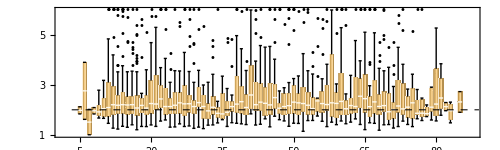

```mathematica
plotData=GatherBy[Sort@Cases[Join@@res,{_?NumericQ..}],First@#&];
plotDataFinal=Clip[Range[5,85]/.Join[#[[1,1]]->#[[All,2]]&/@plotData,#->{}&/@Range[5,85]],{0,6}];
BoxWhiskerChart[plotDataFinal,{{"Outliers",(*"·"*)"•"(*"•"*),Black},{"Fences",0.7,Thin},{"Whiskers",Thin},{"MedianMarker",Directive[Thick,Lighter[RGBColor[0.9194021976505456, 0.7566356889463239, 0.3501495412630121],0.9](*White*)]}},PlotRange->{{-2.5,83.5},{1,6}},ChartLabels->(Range[5,85]/.n_Integer/;n/5!=Floor[n/5]:>""),Frame->True,FrameTicks->{{LinTicks[1,6,TickLengthScale->1.2]/."6"->"≥6",None},Automatic},ChartElementFunction->"GlassBoxWhisker",Epilog->{Black,Dashed,Thickness[0.0015],Line[{{-0.7,2},{85,2}}]},FrameStyle->Directive[Black,Thickness[0.0015]],FrameTicksStyle->Directive[11.5,Black],PlotRangeClipping->True,PlotRangePadding->None,ImageSize->500,AspectRatio->0.3]
```

### Figure 5: New Vaccine Study Predictions

We conducted four new vaccine studies (one in 2022, three from the latest 2023 season). The code below uses the pre-vaccination data from each study to predict the 1-month post-vaccination response.

The 2022 and 2023 UGA studies represent a small sampling (25 individuals from each year) that received Fluzone. They are predicted using the same random forest model presented above (using the null and linear models for comparison).

The 2023 Crotty_Afluria study administered Afluria, and it is also predicted using the same random forest model presented above (using the null and linear models for comparison).

The 2023 Crotty_FluMist study administered FluMist, and previous studies show that this vaccine elicit little-to-no HAI titers post-vaccination. Hence, we modeled the FluMist cohort using the null model (using the linear model for comparison).

#### 2022-2023 UGA predictions

```mathematica
predictionsUGA2022=Join@@Table[Thread[({"UGA2022Sample",virus,data[{virus,#,"Day28"}]/.dat_data:>fixTimes@dat}&/@sera["UGA2022Sample"])->Map[Round[10^(Last@#)]&,completionPredictions[{virus,"UGA2022Sample"},"OtherTables"->{"Hinojosa2020_V2014-2015","Hinojosa2020_V2015","Fox2022HaNam","Fox2022HCW","UGA2016","UGA2017","UGA2018","UGA2019","UGA2020","UGA2021"},"Forest"->leaveOneOut,"PredictAbEvolution"->("Day21"|"Day28"->{"Day0"}),"Return"->"Titers"]]]
,{virus,viruses["UGA2022Sample"]}];
predictionsUGA2022=#[[1,;;-2]]->{#[[1,-1]],#[[2]]}&/@predictionsUGA2022;
```

```mathematica
predictionsUGA2023=Join@@Table[Thread[({"UGA2023Sample",virus,data[{virus,#,"Day28"}]/.dat_data:>fixTimes@dat}&/@sera["UGA2023Sample"])->Map[Round[10^(Last@#)]&,completionPredictions[{virus,"UGA2023Sample"},"OtherTables"->{"Hinojosa2020_V2014-2015","Hinojosa2020_V2015","Fox2022HaNam","Fox2022HCW","UGA2016","UGA2017","UGA2018","UGA2019","UGA2020","UGA2021","UGA2022Sample"},"Forest"->leaveOneOut,"PredictAbEvolution"->("Day21"|"Day28"->{"Day0"}),"Return"->"Titers"]]]
,{virus,Cases[viruses["UGA2023Sample"],virus_/;virusSubtype@virus=="H3N2"]}];
predictionsUGA2023=#[[1,;;-2]]->{#[[1,-1]],#[[2]]}&/@predictionsUGA2023;
```

#### 2023 Crotty predictions

```mathematica
predictionsFM=Join@@Table[{"Crotty2023FM",virus,data[{virus,serum,"Day28p"}]}->Round@data[{virus,serum,"Day0"}],{serum,sera["Crotty2023FM"]},{virus,viruses["Crotty2023"]}];
predictionsFM=#[[1,;;-2]]->{#[[1,-1]],#[[2]]}&/@predictionsFM;
```

```mathematica
(* Afluria predictions using the past 4 seasons *)
predictionsAfluriaUsingLast10Seasons=Join@@Table[Thread[({"Crotty2023Afluria",virus,data[{virus,#,"Day28"}]}&/@sera["Crotty2023Afluria"])->Map[Round[10^(Last@#)]&,completionPredictions[{virus,"Crotty2023Afluria"},"OtherTables"->{"Hinojosa2020_V2014-2015","Hinojosa2020_V2015","Fox2022HaNam","Fox2022HCW","UGA2016","UGA2017","UGA2018","UGA2019","UGA2020","UGA2021","UGA2022Sample"},"Forest"->leaveOneOut,"PredictAbEvolution"->("Day21"|"Day28"->{"Day0"}),"Return"->"Titers"]]]
,{virus,viruses["Crotty2023"]}];
predictionsAfluriaUsingLast10Seasons=#[[1,;;-2]]->{#[[1,-1]],#[[2]]}&/@predictionsAfluriaUsingLast10Seasons/.dat_data:>fixTimes@dat;
```

#### Combined Plot

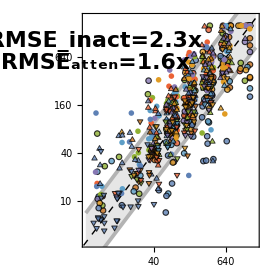
-Graphics- |  |

```mathematica
SeedRandom[12345];
Block[{
colors={RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.368417, 0.506779, 0.709798]},opac=0.8,s=0.06,plotRange=ConstantArray[{3,2000},2],
listPredictions={predictionsUGA2022,predictionsUGA2023,predictionsAfluriaUsingLast10Seasons,predictionsFM},
plotData,vals,errorInact,errorFluMist
},
plotData=Table[
vals=Cases[predictions,entry_/;entry[[1,2]]==virus];
RandomReal[10^(0.1{-1,1}),Dimensions[Last/@vals]]Last/@vals
,{predictions,listPredictions},{virus,viruses["Crotty2023"]}];
(* Now showing the (slightly larger) error from the inactive vaccine predictions only *)
errorInact=RootMeanSquare[Subtract@@@Log10[Join@@N@listPredictions[[;;3,All,-1]]]];
errorFluMist=RootMeanSquare[Subtract@@@Log10[Join@@N@listPredictions[[{4},All,-1]]]];
Grid[{{ListPlot[Clip[Join@@Replace[plotData,{}->{{1,1}},{2}],{-∞,1600}],ScalingFunctions->{"Log","Log"},AspectRatio->1,PlotRange->plotRange,PlotStyle->colors,PlotMarkers->Join@@(ConstantArray[#,Length@viruses["Crotty2023"]]&/@{plotMarker[s,opac,"EdgeThickness"->0.04],plotMarker[s,opac,"Type"->"Diamond","EdgeThickness"->0.04],plotMarker[s,opac,"Type"->"Triangle","EdgeThickness"->0.03],plotMarker[s,opac,"Type"->"UpsideDownTriangle","EdgeThickness"->0.035]}),ImageSize->270,Frame->True,FrameTicks->ConstantArray[{Table[{5 2^(j-1),If[EvenQ@j,5 2^(j-1),""],0.035 If[EvenQ@j,1,2/3]},{j,0,10}],None},2],FrameStyle->Directive[Black,Thickness[0.003]],FrameTicksStyle->14,Prolog->{{GrayLevel[0.9],Polygon[Log@{{plotRange[[1,1]],plotRange[[1,1]] 10^errorInact},{plotRange[[1,2]],plotRange[[1,2]] 10^errorInact},{plotRange[[1,2]],plotRange[[1,2]]/10^errorInact},{plotRange[[1,1]],plotRange[[1,1]]/10^errorInact}}]},{GrayLevel[0.7],Thickness[0.01],Line[Log@{{{plotRange[[1,1]],plotRange[[1,1]] 10^errorInact},{plotRange[[1,2]],plotRange[[1,2]] 10^errorInact}},{{plotRange[[1,1]],plotRange[[1,1]]/10^errorInact},{plotRange[[1,2]],plotRange[[1,2]]/10^errorInact}}}]},{Black,Dashed,Thick,Line[Log@{{2,2},{2000,2000}}]}},Epilog->{Text[font[Row[{"RMSE_inact=",Round[10^errorInact,0.1],"x"}],22,Bold],Log@{4.3,1000},{-1,0},Background->Directive[{White,Opacity[0.5]}]],Text[font[Row[{"RMSE_atten=",Round[10^errorFluMist,0.1],"x"}],22,Bold],Log@{4.3,550},{-1,0},Background->Directive[{White,Opacity[0.5]}]]}],PointLegend[ConstantArray[GrayLevel[0.85],4],font/@{"2022 UGA","2023 UGA","2023 Crotty_Afluria","2023 Crotty_FluMist"},LegendMarkers->{plotMarker["EdgeThickness"->0.03],plotMarker["Type"->"Diamond","EdgeThickness"->0.01],plotMarker["Type"->"Triangle","EdgeThickness"->0.01],plotMarker["Type"->"UpsideDownTriangle","EdgeThickness"->0.01]},LegendMarkerSize->10,LegendFunction->frame],
SwatchLegend[Reverse@colors,font/@stripSubtype/@StringReplace[Reverse@viruses["Crotty2023"],"-"->"-"],LegendFunction->frame]}}]
]
```

### Figure 6: Peak Analysis - Rerun now that peaksQ has been updated

We introduce a new metric, Δ_Peak, that represents the number of years between the two latest peaks in the HAI landscape. We show that 2≤Δ_Peak≤3 corresponds to strong fold-change post-vaccination whereas 4≤Δ_Peak≤6 corresponds to weak fold-change.

#### Panel A: Overview of Problem

Plotting the geometric mean HAI titer (GMT) pre- and post-vaccination for every individual across every dataset.

```mathematica
plotData=Join@@Table[
year=Switch[tableOfInterest,
"Fonville2014_S13",2009,
"Fonville2014_S14",2010,
"Hinojosa2020_V2014-2015",2014,
"Hinojosa2020_V2015",2015,
"Fox2022HaNam"|"Fox2022HCW",2016,
Alternatives@@{"UGA2016","UGA2017","UGA2018","UGA2019","UGA2020","UGA2021"},ToExpression@StringTake[tableOfInterest,-4]
];
listViruses=viruses[tableOfInterest];
Table[GeometricMean/@Transpose[Cases[Table[{data[{virus,serum,"Day0"}],data[{virus,serum,"Day28p"}]},{virus,listViruses}],{_?NumericQ..}]],{serum,sera[tableOfInterest]}]
,{tableOfInterest,{"Fonville2014_S13","Fonville2014_S14","Fox2022HCW","Fox2022HaNam","UGA2016","UGA2017","UGA2018","UGA2019","UGA2020","UGA2021"}}];
```

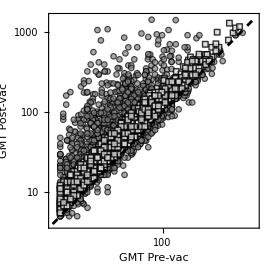

```mathematica
plot[{Cases[plotData,{x_,y_}/;y<=1.1x||y>=2.5x],Cases[plotData,{x_,y_}/;1.1x<y<2.5x]},PlotMarkers->{plotMarker[0.03,0.7],plotMarker[0.01,0.8,"Type"->"Square","EdgeThickness"->0.05]},PlotStyle->{Gray,LightGray},PlotRange->{4.,1500},ScalingFunctions->{"Log","Log"},FrameLabel->(font[#,14]&/@{"GMT Pre-vac","GMT Post-vac"}),FrameTicksStyle->14,FrameStyle->Directive[{Black,Thickness[0.004]}],FrameTicks->ConstantArray[,2]]
```

#### Panel B: Examples of a Strong and Weak Responder

Examples of Δ_Peak shown for a robustly strong and robustly weak responder.

```mathematica
tableOfInterest="UGA2019";
listViruses=DeleteCases[viruses[tableOfInterest],"H3N2 A/South Australia/34/2019"];
{min,max}=MinMax@Flatten@Position[SortBy[listViruses,virusYear],virus_/;studyYear[tableOfInterest]-6<=virusYear@virus<=studyYear[tableOfInterest]];
Table[
preVac=MapIndexed[{First@#2,data[{#,serum,"Day0"}]}&,listViruses];
postVac=MapIndexed[{First@#2,data[{#,serum,"Day28p"}]}&,listViruses];
Show[
showLandscape[serum,ImageSize->130,"VirusNameTicksQ"->False,Prolog->{LightPurple,Rectangle[{min,1.1},{max,Log@4000}]},"ExcludeViruses"->{"H3N2 A/South Australia/34/2019"}][[1]],
ListPlot[peaksQ[serum,studyYear[tableOfInterest],"Return"->"IndexedPeaks"],ScalingFunctions->"Log",PlotStyle->White,PlotMarkers->plotMarker[0.09,0.9,"Type"->"Square","EdgeThickness"->0.1]],PlotLabel->None,FrameLabel->None,FrameTicksStyle->8]
,{serum,{"ID_208_UGA2019","ID_050C_UGA2019"}}]
```

#### Panel C: Individual Study Results

Statistics of the Δ_Peak characterization across all studies.

```mathematica
Clear[stats]
listStudies={"Fonville2014_S13","Fonville2014_S14","Hinojosa2020_V2014-2015","Hinojosa2020_V2015","Fox2022HCW","Fox2022HaNam","UGA2016","UGA2017","UGA2018","UGA2019","UGA2020","UGA2021"};
Block[{correct={},incorrect={},year,listViruses,plotData,actualLargeFoldChange,actualSmallFoldChange,pntsLarge,pntsSmall,categoryLarge,categorySmall,ruleLarge,ruleSmall,largeCorrectlyPredicted,largeIncorrectlyPredicted,smallCorrectlyPredicted,smallIncorrectlyPredicted,peakσ=1},
Do[
year=Switch[tableOfInterest,
"Fonville2014_S13",2009,
"Fonville2014_S14",2010,
"Hinojosa2020_V2014-2015",2014,
"Hinojosa2020_V2015",2015,
"Fox2022HaNam"|"Fox2022HCW",2016,
Alternatives@@{"UGA2016","UGA2017","UGA2018","UGA2019","UGA2020","UGA2021","UGA2022Sample","UGA2023Sample"},ToExpression@StringTake[tableOfInterest,{4,7}],
"Crotty2023Afluria",2023
];
listViruses=viruses[tableOfInterest];plotData=Table[Prepend[GeometricMean/@Transpose[Cases[Table[{data[{virus,serum,"Day0"}],data[{virus,serum,"Day28p"}]},{virus,listViruses}],{_?NumericQ..}]],serum],{serum,sera[tableOfInterest]}];
(* "ID_136_UGA2020" does not have any Day28p values *)
plotData=DeleteCases[plotData,{"ID_136_UGA2020",__}];

actualLargeFoldChange=Cases[plotData,{serum_,x_,y_}/;y>=2.5x:>serum];
actualSmallFoldChange=Cases[plotData,{serum_,x_,y_}/;y<=1.1x:>serum];

{categoryLarge,pntsLarge}=Transpose[peaksQ[#,year,peakσ]&/@actualLargeFoldChange];
{categorySmall,pntsSmall}=Transpose[peaksQ[#,year,peakσ]&/@actualSmallFoldChange];

ruleLarge=Join[Rule@@@N@Tally@categoryLarge,{"PredictLargeFC"->0,"PredictSmallFC"->0}];
ruleSmall=Join[Rule@@@N@Tally@categorySmall,{"PredictLargeFC"->0,"PredictSmallFC"->0}];
{largeCorrectlyPredicted,largeIncorrectlyPredicted}={"PredictLargeFC","PredictSmallFC"}/.ruleLarge;
{smallCorrectlyPredicted,smallIncorrectlyPredicted}={"PredictSmallFC","PredictLargeFC"}/.ruleSmall;

(* {# predicted (strong/weak), # that could be predicted (strong/weak/Missing), total # of sera } *)
stats[tableOfInterest,"FracPredicted"]={largeCorrectlyPredicted+largeIncorrectlyPredicted+smallCorrectlyPredicted+smallIncorrectlyPredicted,Length@actualLargeFoldChange+Length@actualSmallFoldChange,Length@sera[tableOfInterest]};
stats[tableOfInterest,"StrongCorrectlyPredicted"]={largeCorrectlyPredicted,largeCorrectlyPredicted+largeIncorrectlyPredicted};
stats[tableOfInterest,"WeakCorrectlyPredicted"]={smallCorrectlyPredicted,smallCorrectlyPredicted+smallIncorrectlyPredicted};
,{tableOfInterest,listStudies}]
]
```

```mathematica
showGrid[Join[
{font[#,Bold]&/@{"Study",Column[{"Strong or Weak","Subjects"},Alignment->Center],Column[{"Subjects","Predicted"},Alignment->Center],Column[{"% Strong","Predictions Correct"},Alignment->Center],Column[{"% Weak","Predictions Correct"},Alignment->Center]}},
Table[
{StringJoin@Riffle[label@tableOfInterest," "],
Row[{Round@#[[2]],"/",#[[3]]}]&@stats[tableOfInterest,"FracPredicted"],
Row[{Round@#[[1]],"/",#[[2]]}]&@stats[tableOfInterest,"FracPredicted"],
If[#==={0,0},"N/A (0/0)",Row[{Round[100#[[1]]/#[[2]]],"%  ( ",Round@#[[1]],"/",Round@#[[2]],")"}]]&@stats[tableOfInterest,"StrongCorrectlyPredicted"],If[#==={0,0},"N/A (0/0)",Row[{Round[100#[[1]]/#[[2]]],"%  ( ",Round@#[[1]],"/",Round@#[[2]],")"}]]&@stats[tableOfInterest,"WeakCorrectlyPredicted"]}
,{tableOfInterest,listStudies}],
{font[#,Bold]&/@{
"Cumulative",
(*Total[Length/@sera/@listStudies],*)
Row[{Round@#[[2]],"/",#[[3]]}]&@(Total/@Transpose[stats[#,"FracPredicted"]&/@listStudies]),
Row[{Round@#[[1]],"/",#[[2]]}]&@(Total/@Transpose[stats[#,"FracPredicted"]&/@listStudies]),
Row[{Round[100#[[1]]/#[[2]]],"%  ( ",Round@#[[1]],"/",Round@#[[2]],")"}]&@(Total/@Transpose[stats[#,"StrongCorrectlyPredicted"]&/@listStudies]),
Row[{Round[100#[[1]]/#[[2]]],"%  ( ",Round@#[[1]],"/",Round@#[[2]],")"}]&@(Total/@Transpose[stats[#,"WeakCorrectlyPredicted"]&/@listStudies])
}}
],Dividers->{{RGBColor[0.2, 0.2, 0.2],{RGBColor[0.75, 0.75, 0.75]},RGBColor[0.2, 0.2, 0.2]},{RGBColor[0.2, 0.2, 0.2],RGBColor[0.2, 0.2, 0.2],{False},RGBColor[0.2, 0.2, 0.2],RGBColor[0.2, 0.2, 0.2]}}]
```

Study | Strong or Weak
Subjects | Subjects
Predicted | % Strong
Predictions Correct | % Weak
Predictions Correct
2009 Fonv | 25/80 | 2/25 | N/A (0/0) | 100%  ( 2/2)
2010 Fonv | 12/80 | 6/12 | 100%  ( 2/2) | 25%  ( 1/4)
2014 Hin_V | 18/41 | 0/18 | N/A (0/0) | N/A (0/0)
2015 Hin_V | 14/41 | 0/14 | N/A (0/0) | N/A (0/0)
2016 Fox_HCW | 6/49 | 4/6 | 67%  ( 2/3) | 0%  ( 0/1)
2016 Fox_Nam | 59/100 | 41/59 | 87%  ( 34/39) | 0%  ( 0/2)
2016 UGA | 80/148 | 27/80 | 100%  ( 22/22) | 0%  ( 0/5)
2017 UGA | 138/271 | 58/138 | 86%  ( 19/22) | 81%  ( 29/36)
2018 UGA | 112/250 | 16/112 | 0%  ( 0/5) | 100%  ( 11/11)
2019 UGA | 258/461 | 21/258 | 69%  ( 11/16) | 60%  ( 3/5)
2020 UGA | 97/339 | 40/97 | 12%  ( 2/16) | 92%  ( 22/24)
2021 UGA | 134/337 | 9/134 | 67%  ( 4/6) | 0%  ( 0/3)
Cumulative | 953/2197 | 224/953 | 73%  ( 96/131) | 73%  ( 68/93)

#### Panel D: Cumulative Results

Classifying everyone in every study using Δ_Peak. Individuals that cannot be categorized are shown as small gray circles.

```mathematica
{plotDataPredictedLargeFC,plotDataPredictedSmallFC,plotDataNotPredicted}=Block[{res,correct={},incorrect={},year,listViruses,plotData,actualLargeFoldChange,actualSmallFoldChange,pntsLarge,pntsSmall,categoryLarge,categorySmall,ruleLarge,ruleSmall,largeCorrectlyPredicted,largeIncorrectlyPredicted,smallCorrectlyPredicted,smallIncorrectlyPredicted,peakσ=1,plotDataPredictedLargeFC,plotDataPredictedSmallFC,plotDataNotPredicted},
res=Table[
year=Switch[tableOfInterest,
"Fonville2014_S13",2009,
"Fonville2014_S14",2010,
"Hinojosa2020_V2014-2015",2014,
"Hinojosa2020_V2015",2015,
"Fox2022HaNam"|"Fox2022HCW",2016,
Alternatives@@{"UGA2016","UGA2017","UGA2018","UGA2019","UGA2020","UGA2021"},ToExpression@StringTake[tableOfInterest,-4]
];
listViruses=viruses[tableOfInterest];plotData=Table[Prepend[GeometricMean/@Transpose[Cases[Table[{data[{virus,serum,"Day0"}],data[{virus,serum,"Day28p"}]},{virus,listViruses}],{_?NumericQ..}]],serum],{serum,sera[tableOfInterest]}];
(* "ID_136_UGA2020" does not have any Day28p values *)
plotData=DeleteCases[plotData,{"ID_136_UGA2020",___}];

actualLargeFoldChange=Cases[plotData,{serum_,x_,y_}/;(y>=2.5x):>serum];
actualSmallFoldChange=Cases[plotData,{serum_,x_,y_}/;(y<=1.1x):>serum];

{categoryLarge,pntsLarge}=Transpose[peaksQ[#,year,peakσ]&/@actualLargeFoldChange];
{categorySmall,pntsSmall}=Transpose[peaksQ[#,year,peakσ]&/@actualSmallFoldChange];

plotDataPredictedLargeFC=Cases[plotData,{Alternatives@@Join[Extract[actualLargeFoldChange,Position[categoryLarge,"PredictLargeFC"]],Extract[actualSmallFoldChange,Position[categorySmall,"PredictLargeFC"]]],__}];
plotDataPredictedSmallFC=Cases[plotData,{Alternatives@@Join[Extract[actualLargeFoldChange,Position[categoryLarge,"PredictSmallFC"]],Extract[actualSmallFoldChange,Position[categorySmall,"PredictSmallFC"]]],__}];
plotDataNotPredicted=Complement[plotData,plotDataPredictedLargeFC,plotDataPredictedSmallFC];

{plotDataPredictedLargeFC,plotDataPredictedSmallFC,plotDataNotPredicted}
,{tableOfInterest,{"Fonville2014_S13","Fonville2014_S14","Fox2022HCW","Fox2022HaNam","UGA2016","UGA2017","UGA2018","UGA2019","UGA2020","UGA2021"}}];
Join@@@Transpose@res
];
```

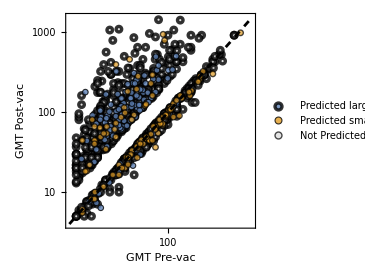

```mathematica
plot[{Cases[plotDataNotPredicted,{_,x_,y_}/;y<=1.1x||y>=2.5x],plotDataPredictedLargeFC,plotDataPredictedSmallFC}[[All,All,{-2,-1}]],PlotMarkers->{plotMarker[0.015,0.8,"EdgeThickness"->0.12],plotMarker[0.045,0.8,"EdgeThickness"->0.04],plotMarker[0.03,0.7,"EdgeThickness"->0.05]},PlotStyle->{LightGray,ColorData[97,1],ColorData[97,2]},PlotRange->{4.,1500},ScalingFunctions->{"Log","Log"},PlotLegends->Placed[PointLegend[{ColorData[97,1],ColorData[97,2],LightGray},font/@{"Predicted large FC (n="<>ToString@Length@plotDataPredictedLargeFC<>")","Predicted small FC (n="<>ToString@Length@plotDataPredictedSmallFC<>")","Not Predicted (n="<>ToString@Length[Cases[plotDataNotPredicted,{_,x_,y_}/;y<=1.1x||y>=2.5x]]<>")"},Spacings->{0.2,0.4},LegendFunction->frameOpaque],Scaled[{{0.62,0.15},{0.5,0.5}}]],FrameTicksStyle->14,FrameLabel->(font[#,14]&/@{"GMT Pre-vac","GMT Post-vac"}),FrameStyle->Directive[{Black,Thickness[0.004]}],FrameTicks->ConstantArray[,2]]
```

### Table 1: Study Statistics

Overview of all vaccine studies examined in this work.

```mathematica
showGrid[Prepend[{Row[Riffle[label[#]," "]],Length@sera[#] Length@viruses[#],Length@sera[#],Length@viruses[#]}&/@Join[Flatten@listCohortsInitial,listCohortsNew],{"Study","# of measurements","# sera","# H3N2 viruses"}]]
```

Study | # of measurements | # sera | # H3N2 viruses
1997 Fonv | 7420 | 106 | 70
1998 Fonv | 8960 | 128 | 70
2009 Fonv | 1600 | 80 | 20
2010 Fonv | 1600 | 80 | 20
2014 Hin_V | 656 | 41 | 16
2015 Hin_V | 656 | 41 | 16
2015 Hin_U | 496 | 31 | 16
2016 Fox_Nam | 4100 | 100 | 41
2016 Fox_HCW | 1764 | 49 | 36
2016 UGA | 2516 | 148 | 17
2017 UGA | 4878 | 271 | 18
2018 UGA | 2500 | 250 | 10
2019 UGA | 3688 | 461 | 8
2020 UGA | 2373 | 339 | 7
2021 UGA | 2359 | 337 | 7
2022 UGA | 175 | 25 | 7
2023 UGA | 150 | 25 | 6
2023 Crotty_Afluria | 168 | 24 | 7
2023 Crotty_FluMist | 175 | 25 | 7

### Table S1: Weak→Weak/Strong→Strong Responses when the Vaccine is Unchanged

For repeaters who participate in two consecutive years during the UGA studies, what is the probability that they will either be strong (post-vac HAI≥80 against vaccine strain) in both years or weak (post-vac HAI<80 against vaccine strain) in both years?

```mathematica
cohortsUGA={
(* FluZone studies *)
"UGA2016","UGA2017","UGA2018","UGA2019","UGA2020","UGA2021","UGA2022Sample","UGA2023Sample"
};
(* When was each subject measured *)
replaceCohort=#[[1,1]]->Last/@#&/@Cases[GatherBy[Join@@(Tuples[{StringRiffle[#,"_"]&/@Most/@StringSplit[sera[#],"_"],{#}}]&/@cohortsUGA),First],entry_/;Length@entry>1];
```

```mathematica
(* Times that each subject was measured *)
replaceTimes=Table[
First@entry->(Cases[seraTimes[#],{First@entry<>"_"<>StringDelete[#,"Sample"],_}][[2]]&/@Last@entry)
,{entry,replaceCohort}];
```

```mathematica
Clear[vaccine]
(* H3N2 Vaccines *)
vaccine["2016","H3N2"]="H3N2 A/Hong Kong/4801/2014";
vaccine["2017","H3N2"]="H3N2 A/Hong Kong/4801/2014";
vaccine["2018","H3N2"]="H3N2 A/Singapore/INFIMH-160019/2016";
vaccine["2019","H3N2"]="H3N2 A/Kansas/14/2017";
vaccine["2020","H3N2"]="H3N2 A/Hong Kong/2671/2019";
vaccine["2021","H3N2"]="H3N2 A/Tasmania/503/2020";
vaccine["2022","H3N2"]="H3N2 A/Darwin/9/2021";
vaccine["2023","H3N2"]="H3N2 A/Darwin/9/2021";
```

```mathematica
(* Identify when an individual had a poor response (0=poor response, 1=strong response) *)
subtype="H3N2";
assoc=Association@Table[
First@entry->({year=Last@StringSplit[First@#,"_UGA"],Boole[data[{vaccine[year,subtype],First@#,Last@#}]>=80]}&/@Last@entry)
,{entry,replaceTimes}];
res=Values[assoc][[All,All,-1]];
```

```mathematica
(* Strong->Strong + Weak->Weak *)
Echo[subtype,"Results for:"];
Table[
tally=Tally@Cases[ToExpression@assoc,entry_/;ContainsAll[First/@entry,{year,year+1}]:>{year/.Rule@@@entry,year+1/.Rule@@@entry}];
Echo[Row[{Round[100.(({1,1}/.Rule@@@tally)+({0,0}/.Rule@@@tally))/Total[Last/@tally],0.1]," n=(",Total[Last/@tally],")"}],"Chance of being strong/strong or weak/weak in "<>ToString@year<>"-"<>ToString[year+1]]
,{year,2016,2022}];
```

Results for:  H3N2

Chance of being strong/strong or weak/weak in 2016-2017  83.3 n=(102)

Chance of being strong/strong or weak/weak in 2017-2018  87.9 n=(149)

Chance of being strong/strong or weak/weak in 2018-2019  72.7 n=(161)

Chance of being strong/strong or weak/weak in 2019-2020  63.9 n=(316)

Chance of being strong/strong or weak/weak in 2020-2021  74.2 n=(252)

Chance of being strong/strong or weak/weak in 2021-2022  84.2 n=(19)

Chance of being strong/strong or weak/weak in 2022-2023  {100.,100.} n=(3)

### Figure S1: Demographics and Dataset Overview

Quantifying the demographics and the number of vaccinees that show little-to-no vaccine response in each study.

```mathematica
listStudies=Flatten@{listCohortsFinal,listCohortsNew};
showGrid@Prepend[Table[
nWeak=Length@Cases[sera[tableToPredict],serum_/;Max[Divide@@@ReverseSort/@Cases[Table[
{data[{virus,serum,"Day0"}],data[{virus,serum,"Day28"}]/.dat_data:>fixTimes@dat}
,{virus,Cases[viruses[tableToPredict],virus_/;virusSubtype@virus=="H3N2"]}],{_?NumericQ..}]]<=2];
nTotal=Length@sera[tableToPredict];
{StringRiffle[label@tableToPredict," "],Length@sera[tableToPredict],vals=DeleteCases[age/@sera[tableToPredict],_age];
If[vals==={},
"-",
Row[{Round@N@Median[vals]," (",Min[vals],"-",Max[vals],")"}]
],
vals=Length/@{Cases[sera[tableToPredict],subject_/;sex[subject]=="M"],Cases[sera[tableToPredict],subject_/;sex[subject]=="F"]};
If[vals==={0,0},
"-",
Row[{Round[100 vals[[1]]/(Total@vals)],"%/",Round[100 vals[[2]]/(Total@vals)],"%"}]
],
Row[{Round[100 nWeak/nTotal],"% (",nWeak,"/",nTotal,")"}],
stripSubtype@assocVaccineStrain@tableToPredict/.{"A/Perth/27/2007"->"A/Brisbane/10/2007","A/Hong Kong/4801/2014_Egg"->"A/Hong Kong/4801/2014","A/Singapore/INFIMH-160019/2016"->"A/Singapore/INFIMH-160019/2016","A/Tasmania/503/2020"->"A/Cambodia/e0826360/2020","UGA2022Sample"|"UGA2023Sample"|"Crotty2023Afluria"|"Crotty2023FM"->"A/Darwin/9/2021"}
}
,{tableToPredict,listStudies}],{"Study",Column[{"# of","Subjects"},Alignment->Center,Spacings->0.05],Column[{"Median Age","(Range)"},Alignment->Center,Spacings->0.05],Column[{"Gender","(% Male/% Female)"},Alignment->Center,Spacings->0.05],Column[{"% Null Responders =","(# with ≤2 fold-change)/(# subjects)"},Alignment->Center,Spacings->0.05],"H3N2 Vaccine Strain"}/.str_String:>font[str,Bold]]
```

Study | # of
Subjects | Median Age
(Range) | Gender
(% Male/% Female) | % Null Responders =
(# with ≤2 fold-change)/(# subjects) | H3N2 Vaccine Strain
2009 Fonv | 80 | - | - | 49% (39/80) | A/Brisbane/10/2007
2010 Fonv | 80 | - | - | 24% (19/80) | A/Perth/16/2009
2014 Hin_V | 41 | 11 (5-16) | - | 44% (18/41) | A/Texas/50/2012
2015 Hin_V | 41 | 12 (6-17) | - | 27% (11/41) | A/Switzerland/9715293/2013
2016 Fox_Nam | 100 | 49 (20-81) | 38%/62% | 1% (1/100) | A/Hong Kong/4801/2014
2016 Fox_HCW | 49 | 38 (24-66) | 33%/67% | 37% (18/49) | A/Hong Kong/4801/2014
2016 UGA | 148 | 27 (18-74) | 39%/61% | 25% (37/148) | A/Hong Kong/4801/2014
2017 UGA | 271 | 27 (12-83) | 45%/55% | 35% (94/271) | A/Hong Kong/4801/2014
2018 UGA | 250 | 16 (12-80) | 44%/56% | 48% (120/250) | A/Singapore/INFIMH-160019/2016
2019 UGA | 461 | 42 (11-85) | 40%/60% | 20% (94/461) | A/Kansas/14/2017
2020 UGA | 339 | 45 (12-85) | 38%/62% | 52% (176/339) | A/Hong Kong/2671/2019
2021 UGA | 337 | 44 (10-86) | 41%/59% | 43% (145/337) | A/Cambodia/e0826360/2020
2022 UGA | 25 | 43 (11-87) | 52%/48% | 20% (5/25) | A/Darwin/9/2021
2023 UGA | 25 | 53 (11-85) | 56%/44% | 72% (18/25) | A/Darwin/9/2021
2023 Crotty_Afluria | 24 | 28 (20-58) | 46%/54% | 67% (16/24) | A/Darwin/9/2021
2023 Crotty_FluMist | 25 | 29 (18-41) | 48%/52% | 84% (21/25) | A/Darwin/9/2021

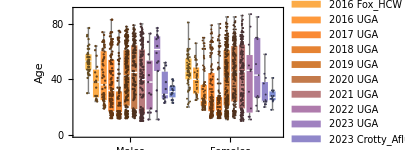

```mathematica
colors=Blend[{#,Black},0.6]&/@{RGBColor[0.9843136860317651, 0.7411764840775561, 0.3254900649788416],RGBColor[0.9882353125344961, 0.6705883187353149, 0.27843131014870315],RGBColor[0.9960786195259893, 0.5999998717333314, 0.23529412119723858],RGBColor[0.9803923008246186, 0.5372548957784151, 0.19999997624115612],RGBColor[0.9019608498139944, 0.5137253845652253, 0.19999992106895892],RGBColor[0.8235293905669796, 0.4862744532628713, 0.200000013014909],RGBColor[0.7647058276539125, 0.47843123357128486, 0.2941175873643535],RGBColor[0.7254901657527417, 0.4823527882995268, 0.48627436738955193],RGBColor[0.6862745309616242, 0.48235289116681374, 0.6745098795423832],RGBColor[0.6274512283626891, 0.5058822907512919, 0.7529412797492486],RGBColor[0.5647059058287746, 0.5294118716431245, 0.7921569474748068],RGBColor[0.49803918809521336, 0.5568627210036746, 0.8313725374746216]};
SeedRandom[12345];
Show[BoxWhiskerChart[{Table[age/@Cases[sera[cohort],subject_/;sex[subject]=="M"],{cohort,listStudies[[5;;]]}],{{}},
Table[age/@Cases[sera[cohort],subject_/;sex[subject]=="F"],{cohort,listStudies[[5;;]]}]},ChartLabels->{font[#,14]&/@{"Males","","Females"},None},ChartLegends->SwatchLegend[Automatic,font/@(StringRiffle[label@#," "]&/@listStudies[[5;;]]),LegendLayout->{"Column",2}],FrameLabel->font["Age",14],FrameTicks->{{,None},{Table[{jj,"",0.03},{jj,1,2}],None}},FrameStyle->Directive[{Black,Thickness[0.003]}],ImageSize->300,AspectRatio->1/2,PlotRange->{{-0.5,26},{0,90}},PlotRangePadding->None],
ListPlot[MapIndexed[Transpose[{RandomReal[0.2{-1,1},Length@#]+First@#2,#}]&,Table[age/@Cases[sera[cohort],subject_/;sex[subject]=="M"],{cohort,listStudies[[5;;]]}]],PlotStyle->colors],ListPlot[MapIndexed[Transpose[{RandomReal[0.2{-1,1},Length@#]+13.1+First@#2,#}]&,Table[age/@Cases[sera[cohort],subject_/;sex[subject]=="F"],{cohort,listStudies[[5;;]]}]],PlotStyle->colors]]
```

### Figure S2: Feature Importance for Age≥65

Here, we show how the predictive power from Figure 2 changes if we restrict our analysis to ages 65+. Although the number of pairs we can test is smaller, the predictions show a consistent trend downwards, especially once variants are considered.

```mathematica
(* === Vaccine+variants+age, across datasets === *)
Δage=10.;
response=Association@Table[
Table[
serum->Association@{
"Variants"->Association@Table[aliasBest[virus]->(If[NumericQ@#,Log10@#,Missing[]]&[data[{virus,serum,"Day0"}]]),{virus,Cases[viruses[cohort],virus_/;virusSubtype@virus=="H3N2"&&!MatchQ[virus,assocVaccineStrain@cohort]]}],
"Age"->If[MatchQ[#,_age],Missing[],#]&@age[serum],
"Sex"->If[MatchQ[#,_sex],Missing[],#]&@sex[serum],
"BMI"->If[MatchQ[#,_BMI],Missing[],Round@#]&@BMI[serum],
"Location"->Replace[cohort,{"Fonville2014_S5"|"Fonville2014_S6"|"Fonville2014_S13"|"Fonville2014_S14"|"Fox2022HCW":>"Australia","Fox2022HaNam":>"Ha Nam","Hinojosa2020_V2014-2015"|"Hinojosa2020_V2015"|"Hinojosa2020_U2015":>"Wisconsin","UGA2016"|"UGA2017"|"UGA2018"|"UGA2019"|"UGA2020"|"UGA2021":>"Georgia"}],
"DateVaccine"->Replace[dateVaccine[serum],{
(* Roll over anyone getting vaccinated past Jan 1 to make days continuous *)
date_DateObject:>(date["DayOfYear"]/.val_/;val<100:>val+365),
_dateVaccine:>Missing[]}],
"DoseVaccine"->Replace[vaccineDose[serum],{_vaccineDose:>Missing[]}],
"VaccinePre"->(If[NumericQ@#,Log10@#,Missing[]]&[data[{assocVaccineStrain@cohort,serum,"Day0"}]]),"VaccinePost"->(If[NumericQ@#,Log10@#,Missing[]]&[data[{assocVaccineStrain@cohort,serum,"Day28"}]/.dat_data:>fixTimes@dat])
}
,{serum,Cases[sera[cohort],serum_/;age[serum]>=65]}]
,{cohort,{"Fox2022HaNam","Fox2022HCW","UGA2016","UGA2017","UGA2018","UGA2019","UGA2020","UGA2021"}}]/.dat_data:>fixTimes@dat;
response=DeleteCases[response,entry_/;MissingQ@entry["VaccinePost"]];
```

```mathematica
Clear[pairs]
```

```mathematica
pairs[{"VaccinePre"}]=Block[{pos,tablesPredictingFrom,vals},Flatten[Table[
pos=Position[listCohortsInitial,tableToPredict][[1,1]];
tablesPredictingFrom=Join@@listCohortsInitial[[1;;pos-1]];
Table[
Cases[Tuples[{sera[tablePredictingFrom],sera[tableToPredict]}],pair_/;(
(* Check for two Missings canceling each other out *)
vals={response[First@pair]["VaccinePre"],response[Last@pair]["VaccinePre"]};
MatchQ[vals,{_?NumericQ..}]&&Abs[Subtract@@vals]<=0.5 Log10[2.]
)]
,{tablePredictingFrom,tablesPredictingFrom}]
,{tableToPredict,Flatten[listCohortsInitial]}],2]
];
```

```mathematica
pairs[{"VaccinePre","Variants"}]=Block[{v1,v2,overlapViruses,vals},
Cases[pairs[{"VaccinePre"}],pair_/;(
{v1,v2}=(response[#]["Variants"]&/@pair);
overlapViruses=Intersection@@Keys/@{v1,v2};
vals={v1/@overlapViruses,v2/@overlapViruses};
vals=DeleteMissing[valsᵀ,1,All]ᵀ;
(* ≥5 overlapping viruses (excluding vaccine strains) with correlation>0.9 *)
(Length@overlapViruses>=5)&&(Length@First@vals>1)&&TrueQ[Min[StandardDeviation/@vals]>10^-6.]&&(Correlation@@vals>0.9)
)]
];
```

```mathematica
pairs[{"Age"}]=Block[{pos,tablesPredictingFrom,vals},Flatten[Table[
pos=Position[listCohortsInitial,tableToPredict][[1,1]];
tablesPredictingFrom=Join@@listCohortsInitial[[1;;pos-1]];
Table[
Cases[Tuples[{sera[tablePredictingFrom],sera[tableToPredict]}],pair_/;(
(* Check for two Missings canceling each other out *)
vals={response[First@pair]["Age"],response[Last@pair]["Age"]};
MatchQ[vals,{_?NumericQ..}]&&TrueQ[Abs[Subtract@@vals]<=Δage]
)]
,{tablePredictingFrom,tablesPredictingFrom}]
,{tableToPredict,Flatten[listCohortsInitial]}],2]
];
```

```mathematica
pairs[{"Sex"}]=Block[{pos,tablesPredictingFrom,vals},Flatten[Table[
pos=Position[listCohortsInitial,tableToPredict][[1,1]];
tablesPredictingFrom=Join@@listCohortsInitial[[1;;pos-1]];
Table[
Cases[Tuples[{sera[tablePredictingFrom],sera[tableToPredict]}],pair_/;(
(* Check for two Missings canceling each other out *)
vals={response[First@pair]["Sex"],response[Last@pair]["Sex"]};
MatchQ[vals,{_String..}]&&Equal@@vals
)]
,{tablePredictingFrom,tablesPredictingFrom}]
,{tableToPredict,Flatten[listCohortsInitial]}],2]
];
```

```mathematica
pairs[{"BMI"}]=Block[{pos,tablesPredictingFrom,vals},Flatten[Table[
pos=Position[listCohortsInitial,tableToPredict][[1,1]];
tablesPredictingFrom=Join@@listCohortsInitial[[1;;pos-1]];
Table[
Cases[Tuples[{sera[tablePredictingFrom],sera[tableToPredict]}],pair_/;(
(* Check for two Missings canceling each other out *)
vals={response[First@pair]["BMI"],response[Last@pair]["BMI"]};
MatchQ[vals,{_?NumericQ..}]&&TrueQ[Abs[Subtract@@vals]<=2.]
)]
,{tablePredictingFrom,tablesPredictingFrom}]
,{tableToPredict,Flatten[listCohortsInitial]}],2]
];
```

```mathematica
pairs[{"DateVaccine"}]=Block[{pos,tablesPredictingFrom,vals},Flatten[Table[
pos=Position[listCohortsInitial,tableToPredict][[1,1]];
tablesPredictingFrom=Join@@listCohortsInitial[[1;;pos-1]];
Table[
Cases[Tuples[{sera[tablePredictingFrom],sera[tableToPredict]}],pair_/;(
(* Check for two Missings canceling each other out *)
vals={response[First@pair]["DateVaccine"],response[Last@pair]["DateVaccine"]};
MatchQ[vals,{_?NumericQ..}]&&TrueQ[Abs[Subtract@@vals]<=14.]
)]
,{tablePredictingFrom,tablesPredictingFrom}]
,{tableToPredict,Flatten[listCohortsInitial]}],2]
];
```

```mathematica
pairs[{"DoseVaccine"}]=Block[{pos,tablesPredictingFrom,vals},Flatten[Table[
pos=Position[listCohortsInitial,tableToPredict][[1,1]];
tablesPredictingFrom=Join@@listCohortsInitial[[1;;pos-1]];
Table[
Cases[Tuples[{sera[tablePredictingFrom],sera[tableToPredict]}],pair_/;(
(* Check for two Missings canceling each other out *)
vals={response[First@pair]["DoseVaccine"],response[Last@pair]["DoseVaccine"]};
MatchQ[vals,{_String..}]&&Equal@@vals
)]
,{tablePredictingFrom,tablesPredictingFrom}]
,{tableToPredict,Flatten[listCohortsInitial]}],2]
];
```

```mathematica
pairs[{"Location"}]=Block[{pos,tablesPredictingFrom,vals},Flatten[Table[
pos=Position[listCohortsInitial,tableToPredict][[1,1]];
tablesPredictingFrom=Join@@listCohortsInitial[[1;;pos-1]];
Table[
Cases[Tuples[{sera[tablePredictingFrom],sera[tableToPredict]}],pair_/;(
(* Check for two Missings canceling each other out *)
vals={response[First@pair]["Location"],response[Last@pair]["Location"]};
MatchQ[vals,{_String..}]&&Equal@@vals
)]
,{tablePredictingFrom,tablesPredictingFrom}]
,{tableToPredict,Flatten[listCohortsInitial]}],2]
];
```

```mathematica
pairs[{features__,"Age"}]:=pairs[{features,"Age"}]=Block[{vals},
Cases[pairs[{features}],pair_/;(
(* Check for two Missings canceling each other out *)
vals={response[First@pair]["Age"],response[Last@pair]["Age"]};
MatchQ[vals,{_?NumericQ..}]&&TrueQ[Abs[Subtract@@vals]<=Δage]
)]
];
pairs[{features__,"Sex"}]:=pairs[{features,"Sex"}]=Block[{vals},
Cases[pairs[{features}],pair_/;(
(* Check for two Missings canceling each other out *)
vals={response[First@pair]["Sex"],response[Last@pair]["Sex"]};
MatchQ[vals,{_String..}]&&Equal@@vals
)]
];
pairs[{features__,"BMI"}]:=pairs[{features,"BMI"}]=Block[{vals},
Cases[pairs[{features}],pair_/;(
(* Check for two Missings canceling each other out *)
vals={response[First@pair]["BMI"],response[Last@pair]["BMI"]};
MatchQ[vals,{_?NumericQ..}]&&TrueQ[Abs[Subtract@@vals]<=2.]
)]
];
pairs[{features__,"DateVaccine"}]:=pairs[{features,"DateVaccine"}]=Block[{vals},
Cases[pairs[{features}],pair_/;(
(* Check for two Missings canceling each other out *)
vals={response[First@pair]["DateVaccine"],response[Last@pair]["DateVaccine"]};
MatchQ[vals,{_?NumericQ..}]&&TrueQ[Abs[Subtract@@vals]<=14.]
)]
];
pairs[{features__,"DoseVaccine"}]:=pairs[{features,"DoseVaccine"}]=Block[{vals},
Cases[pairs[{features}],pair_/;(
(* Check for two Missings canceling each other out *)
vals={response[First@pair]["DoseVaccine"],response[Last@pair]["DoseVaccine"]};
MatchQ[vals,{_String..}]&&Equal@@vals
)]
];
pairs[{features__,"Location"}]:=pairs[{features,"Location"}]=Block[{vals},
Cases[pairs[{features}],pair_/;(
(* Check for two Missings canceling each other out *)
vals={response[First@pair]["Location"],response[Last@pair]["Location"]};
MatchQ[vals,{_String..}]&&Equal@@vals
)]
];
```

```mathematica
featuresList={
{"Age"},
{"Sex"},
{"BMI"},
{"DateVaccine"},
{"DoseVaccine"},
{"Location"},

{"VaccinePre"},
{"VaccinePre","Age"},
{"VaccinePre","Sex"},
{"VaccinePre","BMI"},
{"VaccinePre","DateVaccine"},
{"VaccinePre","DoseVaccine"},
{"VaccinePre","Location"},

{"VaccinePre","Variants"},
{"VaccinePre","Variants","Age"},
{"VaccinePre","Variants","Sex"},
{"VaccinePre","Variants","BMI"},
{"VaccinePre","Variants","DateVaccine"},
{"VaccinePre","Variants","DoseVaccine"},
{"VaccinePre","Variants","Location"}
};
(* Number of studies that the pairs span for each feature. When this is only 1, you may have an artificially low RMSE because you are within one superset *)
numStudies=Table[
Total[Boole@ContainsAny[sera[#],Flatten@pairs[features]]&/@{"UGA","Fox2022","Fonville2014","Hinojosa2020"}]
,{features,featuresList}];
Clear[rmse]
rmse[features_List]:=Block[{plotData},
10^RootMeanSquare[Subtract@@@DeleteMissing[Map[response[#]["VaccinePost"]&,pairs[features],{2}],1,All]]
]
plotDataRMSE=MapIndexed[{First@#2,rmse[#]}&,featuresList];
```

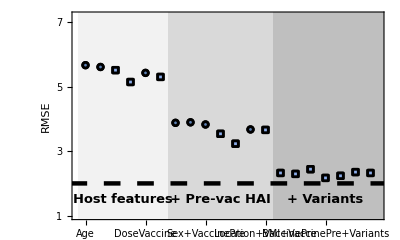

```mathematica
(* Plotting *)
frameTicks=MapIndexed[{First@#2,Rotate[Style[font@Total@#,If[numStudies[[First@#2]]==1,
(* If all pairs are from UGA studies *)
RGBColor[0.5477240862612718, 0.6781403431438215, 0.9198750056398158],
(* Features whose statistics derive from ≥2 data supersets (i.e. more than just UGA) *)
Black
]],π/2],0.015}&,featuresList];
ListPlot[List/@plotDataRMSE,Frame->{True,True,False,False},PlotRange->{{0.5,Length@plotDataRMSE+0.5},{1,7.2}},FrameTicks->{frameTicks,},Epilog->{Black,Dashing[0.03],Thickness[0.008],Line[{{0,2},{30,2}}],
Text[font["Host features",Bold,13],{3.5,1.5}],
Text[font["+ Pre-vac HAI",Bold,13],{10,1.5}],
Text[font["+ Variants",Bold,13],{17,1.5}]},Prolog->{{GrayLevel[0.95],Rectangle[{0.5,0.5},{6.5,8}]},{GrayLevel[0.85],Rectangle[{6.5,0.5},{13.5,8}]},{GrayLevel[0.75],Rectangle[{13.5,0.5},{23.5,8}]}},PlotMarkers->ReplacePart[ConstantArray[plotMarker[0.04,"EdgeThickness"->0.1],Length@featuresList],Position[numStudies,1]->plotMarker[0.043,"Type"->"Square","EdgeThickness"->0.1]],PlotStyle->ReplacePart[ConstantArray[ColorData[97,1],Length@featuresList],Position[numStudies,1]->RGBColor[0.5477240862612718, 0.6781403431438215, 0.9198750056398158]],FrameLabel->font["RMSE",16],FrameStyle->Directive[Black,Thickness[0.002]],FrameTicksStyle->14,AspectRatio->0.6]
```

```mathematica
numDatasets=Table[Total[Boole@ContainsAny[sera[#],Flatten@pairs[features]]&/@Flatten[listCohortsInitial]],{features,featuresList}];
showGrid[Prepend[Transpose@{font/@Total/@featuresList,numDatasets,numStudies,Length/@pairs/@featuresList},{"Features","# Datasets","# Supersets","n Measurements"}],"Header"->"TopLeft"]
```

Features | # Datasets | # Supersets | n Measurements
Age | 8 | 2 | 39125
Sex | 8 | 2 | 21862
BMI | 5 | 1 | 9983
DateVaccine | 6 | 1 | 17027
DoseVaccine | 8 | 2 | 25213
Location | 6 | 1 | 41060
VaccinePre | 8 | 2 | 7161
Age+VaccinePre | 8 | 2 | 6537
Sex+VaccinePre | 8 | 2 | 3699
BMI+VaccinePre | 5 | 1 | 1658
DateVaccine+VaccinePre | 6 | 1 | 2788
DoseVaccine+VaccinePre | 8 | 2 | 4462
Location+VaccinePre | 6 | 1 | 6833
VaccinePre+Variants | 5 | 1 | 79
Age+VaccinePre+Variants | 5 | 1 | 71
Sex+VaccinePre+Variants | 5 | 1 | 41
BMI+VaccinePre+Variants | 4 | 1 | 16
DateVaccine+VaccinePre+Variants | 4 | 1 | 46
DoseVaccine+VaccinePre+Variants | 5 | 1 | 67
Location+VaccinePre+Variants | 5 | 1 | 79

### Figure S3: Full Virus Aliases

To increase the overlapping variants between studies, we equate nearly homologous variants that have sufficiently similar sequences. We call these equated variants virus “aliases” in the code, so that after transforming each variant to its aliased name we will have fewer total variants and more overlap across studies. This figure describes how we chose these aliases to maximize overlap while still ensuring that the aliased variants exhibited similar HAI profiles.

#### Panel A: HAI vs Sequence Similarity

For any pair of variants whose HA sequence at epitopes A-E differ by ≤ΔAA_Epitope (x-axis), we calculate the RMSE between their HAI against the vaccine strain (y-axis).

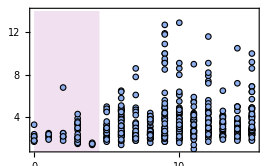

```mathematica
plotData={#[[1,1]],ToExpression@#[[2]]}&/@Join@@Table[
assoc=Association[sequences[tableOfInterest/.{"Fonville2014_S13"->"Fonville2014","Fonville2014_S14"->"Fonville2014","Hinojosa2020_V2014-2015"->"Hinojosa2020","Hinojosa2020_V2015"->"Hinojosa2020","Fox2022HaNam"->"Fox2022","Fox2022HCW"->"Fox2022","UGA2016"->"UGA","UGA2017"->"UGA","UGA2018"->"UGA","UGA2019"->"UGA","UGA2020"->"UGA","UGA2021"->"UGA"}]];
listViruses=Cases[viruses[tableOfInterest],virus_/;(StringQ@#&&StringLength@#==566&[assoc[virus]])];
{compareSequences[assoc/@#,"EpitopeReferenceStrain"->"H3N2 A/Perth/16/2009","ΔAAHead"->{"H3N2",Automatic},"Return"->"NumDifferences"],
diffHAI=Log10@Cases[
Table[
{data[{First@#,First@serumTime,Last@serumTime}],data[{Last@#,First@serumTime,Last@serumTime}]}
,{serumTime,seraTimes[tableOfInterest]}]
,{_?NumericQ..}];
rmse=ToString@Round[10^RootMeanSquare[Subtract@@@diffHAI],0.1]}&/@Subsets[listViruses,{2}]
,{tableOfInterest,Flatten[listCohortsFinal]}];
ListPlot[plotData,PlotRange->{{0,15.2},{1,14}},PlotMarkers->plotMarker[],PlotStyle->ColorData[95,1],Frame->{True,True,False,False},FrameTicks->,FrameTicksStyle->12,FrameStyle->Directive[{Black,Thickness[0.002]}],ImageSize->270,Prolog->{LightPurple,Rectangle[{0,0},{4.5,14}]}]
```

#### Panel B: Sequence Similarity

Table showing all variant pairs with ΔAA_Epitope≤5 across all studies.

```mathematica
seqs=;
replacements={#,aliasBest[#]}&/@SortBy[DeleteCases[Cases[DeleteDuplicates[Join@@viruses/@Flatten@listCohortsInitial],virus_/;virusSubtype@virus=="H3N2"&&virus=!=aliasBest@virus],Alternatives@@{"H3N2 A/Shanghai/11/1987","H3N2 A/Sichuan/2/1987"}],virusYear];
vals=Prepend[Join[stripSubtype/@#,compareSequences[#[[1]]/.seqs,#[[2]]/.seqs,"EpitopeReferenceStrain"->"H3N2 A/Perth/16/2009","Return"->"NumDifferences","ΔAAHead"->{"H3N2",Automatic}]]&/@replacements,font[#,Bold]&/@{"Original H3N2 Virus","Analogous Virus","ΔAA_Epitope","ΔAA_Head","ΔAA_Total"}];
(* Manually fixing "H3N2 A/Victoria/3/1975" and "H3N2 A/Bilthoven/1761/1976" (insertion in the latter) *)
vals[[5,-3;;]]=compareSequences["H3N2 A/Victoria/3/1975"/.seqs,StringInsert["H3N2 A/Bilthoven/1761/1976"/.seqs,"-",25],"EpitopeReferenceStrain"->"H3N2 A/Perth/16/2009","Return"->"NumDifferences","ΔAAHead"->{"H3N2",Automatic}];
showGrid[vals]
```

Warning!  Sequences not the same length

Original H3N2 Virus | Analogous Virus | ΔAA_Epitope | ΔAA_Head | ΔAA_Total
A/Aichi/2/1968 | A/Hong Kong/1/1968 | 0 | 0 | 0
A/Bilthoven/16190/1968 | A/Hong Kong/1/1968 | 2 | 2 | 3
A/Bilthoven/21793/1972 | A/Port Chalmers/1/1973 | 3 | 3 | 4
A/Victoria/3/1975 | A/Bilthoven/1761/1976 | 4 | 5 | 6
A/Bilthoven/2271/1976 | A/Texas/1/1977 | 0 | 0 | 1
A/Netherlands/233/1982 | A/Bangkok/1/1979 | 4 | 3 | 6
A/Netherlands/620/1989 | A/Beijing/353/1989 | 2 | 2 | 3
A/Wuhan/359/1995 | A/Nanchang/933/1995 | 2 | 2 | 2
A/Townsville/2/1999 | A/Panama/2007/1999 | 1 | 2 | 3
A/Philippines/472/2002 | A/Wyoming/3/2003 | 4 | 4 | 6
A/South Australia/84/2002 | A/Netherlands/1/2002 | 2 | 2 | 3
A/California/7/2004 | A/New York/55/2004 | 3 | 3 | 4
A/New York/55/2004_Egg | A/New York/55/2004 | 0 | 0 | 0
A/Wisconsin/67/2005_Egg | A/Wisconsin/67/2005 | 0 | 0 | 0
A/Brisbane/10/2007 | A/Uruguay/716/2007 | 1 | 1 | 2
A/Perth/27/2007 | A/Hanam/134/2008 | 1 | 1 | 4
A/Hanam/135/2008 | A/Uruguay/716/2007 | 3 | 3 | 5
A/Victoria/208/2009 | A/Hanam/201/2009 | 4 | 4 | 4
A/Hanam/53/2010 | A/Hanam/444/2010 | 3 | 2 | 3
A/Victoria/8/2010 | A/Victoria/361/2011_Egg | 3 | 3 | 6
A/Hong Kong/4801/2014_Egg | A/Hong Kong/4801/2014 | 0 | 0 | 0
A/Singapore/INFIMH-160019/2016_Egg | A/Singapore/INFIMH-160019/2016 | 0 | 0 | 0

#### Panel C: Virus Aliases

Table showing the exact variants measured in each study (light orange), the aliased variants (gold), and variants that were not measured not aliased (gray).

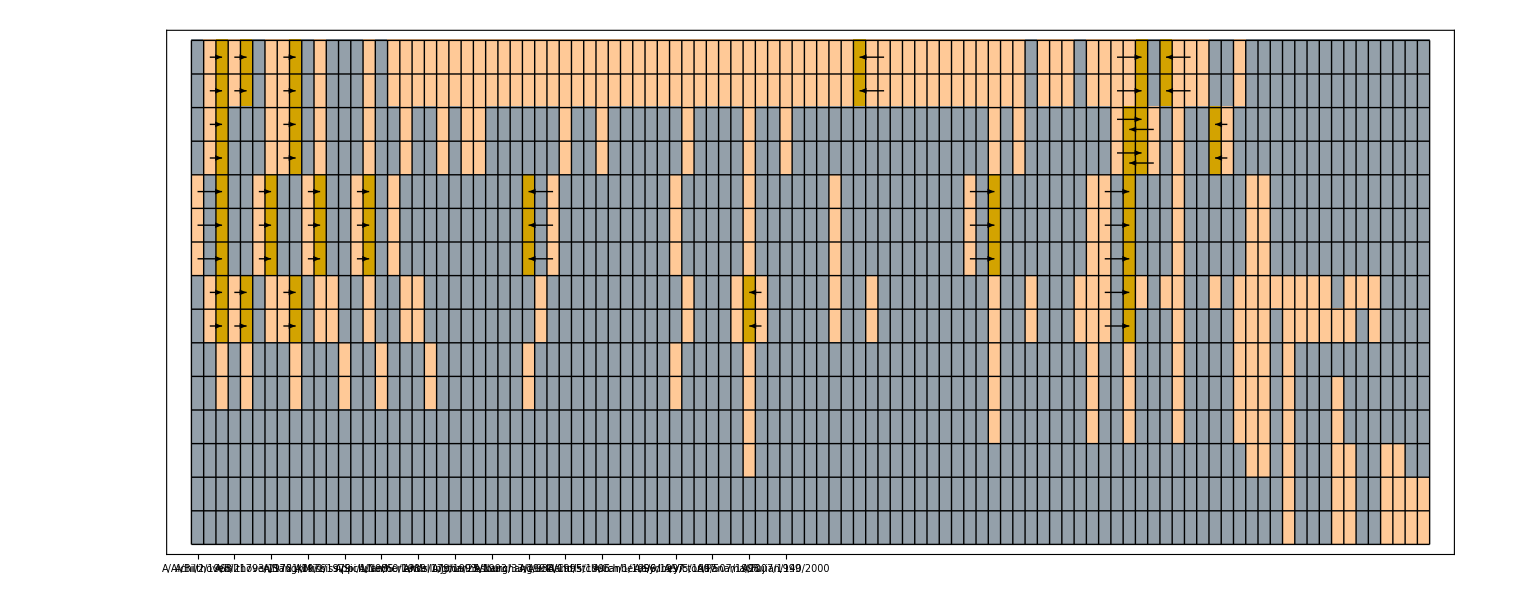

```mathematica
delete={"H3N2 A/Shanghai/11/1987","H3N2 A/Sichuan/2/1987",
(* This variant gets aliased to Victoria 2011_Egg, and we do not show egg strains *)
"H3N2 A/Victoria/8/2010"};
$listVirusesGlobal=SortBy[Cases[Union@Flatten[Join[#,aliasBest/@#]&/@viruses/@Flatten@listCohortsInitial],virus_/;virusSubtype@virus=="H3N2"],virusYear];
$listVirusesGlobal=DeleteCases[$listVirusesGlobal,Alternatives@@delete];
refinedViruses=DeleteCases[$listVirusesGlobal,"H3N2 A/Philippines/472/2002_Egg"|"H3N2 A/New York/55/2004_Egg"|"H3N2 A/Wisconsin/67/2005_Egg"|"H3N2 A/Uruguay/716/2007_Egg"|"H3N2 A/Perth/16/2009_Egg"|"H3N2 A/Victoria/8/2010"|"H3N2 A/Victoria/361/2011_Egg"|"H3N2 A/Texas/50/2012_Egg"|"H3N2 A/Switzerland/9715293/2013_Egg"|"H3N2 A/Hong Kong/4801/2014_Egg"|"H3N2 A/Singapore/INFIMH-160019/2016_Egg"|"H3N2 A/Kansas/14/2017_Egg"];
listVirusCohort=Join@@(Thread[{Cases[viruses[#],virus_/;virusSubtype@virus=="H3N2"],#}]&/@Flatten@listCohortsInitial);
listVirusCohort=DeleteCases[listVirusCohort,
(* Remove egg strains that have non-egg counterparts in the same dataset *)
(* All other egg strains will be taken care of by virus aliases *)
{Alternatives@@delete,_}]/.{"H3N2 A/New York/55/2004_Egg"->"H3N2 A/New York/55/2004","H3N2 A/Wisconsin/67/2005_Egg"->"H3N2 A/Wisconsin/67/2005","H3N2 A/Hong Kong/4801/2014_Egg"->"H3N2 A/Hong Kong/4801/2014","H3N2 A/Singapore/INFIMH-160019/2016_Egg"->"H3N2 A/Singapore/INFIMH-160019/2016"};
aliases=aliasBest/@listVirusCohort;
arrows=Arrow[{{-0.5+Position[refinedViruses,#[[1]]][[1,1]],0.5+Length@Flatten@listCohortsInitial-Position[Flatten@listCohortsInitial,#[[2]]][[1,1]]},{-0.5+Position[refinedViruses,aliasBest@#[[1]]][[1,1]],0.5+Length@Flatten@listCohortsInitial-Position[Flatten@listCohortsInitial,#[[2]]][[1,1]]}}]&/@DeleteCases[listVirusCohort,virusCohort_/;virusCohort===aliasBest@virusCohort||MemberQ[viruses[Last@virusCohort],First@aliasBest@virusCohort]];
listViruses=SortBy[DeleteDuplicates[First/@listVirusCohort],virusYear];
Rotate[Show[ArrayPlot[Table[
Table[
Which[
(* Measured *)
MemberQ[listVirusCohort,{virus,cohort}],1,
(* Aliased *)
!MemberQ[listVirusCohort,aliasBest@{virus,cohort}]&&MemberQ[aliases,aliasBest@{virus,cohort}],2,
(* Not measured or aliased *)
True,0
]
,{virus,refinedViruses}]
,{cohort,Flatten@listCohortsInitial}],Mesh->True,MeshStyle->Directive[Black],ColorRules->{2->Darker[RGBColor[0.92, 0.71, 0.],0.1](*RGBColor[0.9400000000000001, 0.77, 0.]*),1->RGBColor[1, 0.7866666666666667, 0.5933333333333333],0->RGBColor[0.5800000000000001, 0.6266666666666667, Rational[2, 3]]},Frame->True,PlotRangePadding->None,PlotRangeClipping->True,FrameTicks->{{None,MapIndexed[{First@#2,Rotate[font[StringRiffle[label@#," "],12],π]}&,Flatten@listCohortsInitial]},{MapIndexed[{First@#2,Rotate[font[#,12],π/2]}&,stripSubtype/@refinedViruses],None}},ImageSize->15 Length@refinedViruses],Graphics[{Thick,Arrowheads[Medium],arrows/.{(* Prevent arrow collisions *)
Arrow[{{75.5,12.5},{77.5,12.5}}]->Arrow[{{75.5,12.65},{77.5,12.65}}],
Arrow[{{78.5,12.5},{76.5,12.5}}]->Arrow[{{78.5,12.35},{76.5,12.35}}],
Arrow[{{75.5,11.5},{77.5,11.5}}]->Arrow[{{75.5,11.65},{77.5,11.65}}],
Arrow[{{78.5,11.5},{76.5,11.5}}]->Arrow[{{78.5,11.35},{76.5,11.35}}]
}}]],-π/2]
```

#### Panel D: Virus Equivalence

Check cases of virus aliases when both variants are measured in the same study.

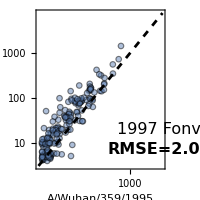
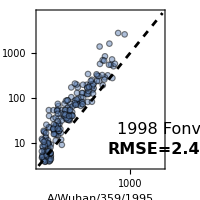
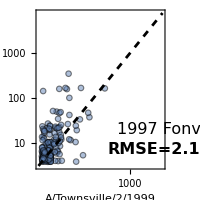
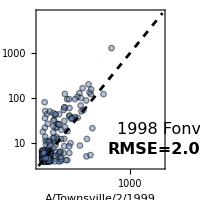
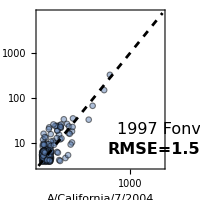
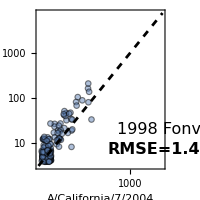
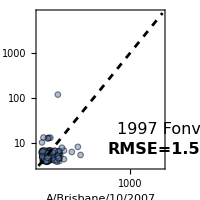
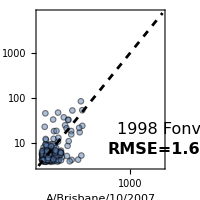

```mathematica
(* Cases of virus equivalence (both measured in the same study) that we can explicitly check *)
checks=Cases[replacements,entry_/;Length@Intersection[containingTables[entry[[1]]],containingTables[entry[[2]]],Flatten@listCohortsInitial]>0];
SeedRandom[12345];
Table[
cohorts=Cases[Flatten@listCohortsInitial,cohort_/;ContainsAll[viruses[cohort],check]];
(
plotData=DeleteMissing[Log10[Join@@Table[{data[{check[[1]],serum,time}],data[{check[[2]],serum,time}]},{serum,sera[#]},{time,times[#]}]]/.dat_data:>Missing[],1,All];
rmse=ToString@Round[10^RootMeanSquare[Subtract@@@plotData],0.1];
If[StringTake[rmse,-1]==".",rmse=rmse<>"0"];
plot[RandomReal[0.13{-1,1},Dimensions@plotData]+plotData,ImageSize->200,Frame->True,FrameStyle->Directive[Black,Thickness[0.006]],FrameTicks->ConstantArray[{MapAt[Log10,,{All,1}],None},2],FrameTicksStyle->12,PlotRange->Log10@{3,8000},FrameLabel->(font[#,14]&/@stripSubtype/@{check[[1]],check[[2]]}),Epilog->{Text[font[Row[Riffle[label[#]," "]],16],{3.8,1.3},{1,0}],Text[font[Row[{"RMSE=",rmse,"x"}],16,Bold],{3.8,0.85},{1,0}]},PlotMarkers->plotMarker[0.07,0.5,"EdgeThickness"->Small]]
)&/@cohorts
,{check,checks}]
```

#### Panel E: Egg Strains = Non-Egg Strains

Check cases of egg and non-egg variants measured in the same study.

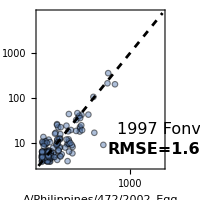
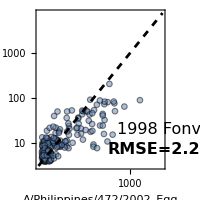
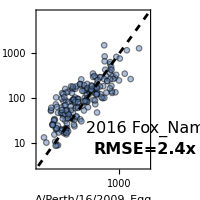
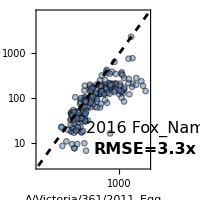
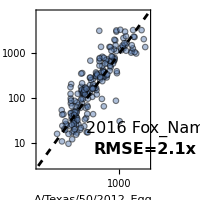
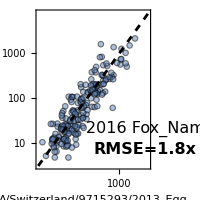
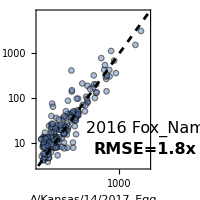
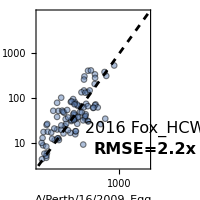

```mathematica
entries=Flatten[(
eggs=Cases[viruses[#],str_String/;StringMatchQ[str,__~~"Egg"]];
Cases[eggs,virus_/;MemberQ[viruses[#],StringDelete[virus,"_Egg"]]:>{virus,#}]
)&/@Flatten@listCohortsInitial,1];
SeedRandom[12345];
Table[
{virusOfInterest,cohort}=entry;
plotData=DeleteMissing[Log10[Join@@Table[{data[{virusOfInterest,serum,time}],data[{StringDelete[virusOfInterest,"_Egg"],serum,time}]},{serum,sera[cohort]},{time,times[cohort]}]]/.dat_data:>Missing[],1,All];
rmse=ToString@Round[10^RootMeanSquare[Subtract@@@plotData],0.1];
If[StringTake[rmse,-1]==".",rmse=rmse<>"0"];
plot[RandomReal[0.13{-1,1},Dimensions@plotData]+plotData,ImageSize->200,Frame->True,FrameStyle->Directive[Black,Thickness[0.006]],FrameTicks->ConstantArray[{MapAt[Log10,,{All,1}],None},2],FrameTicksStyle->12,PlotRange->Log10@{3,8000},FrameLabel->(font[#,If[MemberQ[entries[[{6,11}]],entry],12,14]]&/@stripSubtype/@{virusOfInterest,StringDelete[virusOfInterest,"_Egg"]}),Epilog->{Text[font[Row[Riffle[label[cohort]," "]],16],{3.8,1.3},{1,0}],Text[font[Row[{"RMSE=",rmse,"x"}],16,Bold],{3.8,0.85},{1,0}]},PlotMarkers->plotMarker[0.07,0.5,"EdgeThickness"->Small]]
,{entry,entries}]
```

### Figure S4: Feature Importance for Uruguay 2007

Example random forests to predict H3N2 Uruguay 2007 in 2017 UGA. For simplicity, we choose one study from each superset.

For speed, we comment and can the results below

```mathematica
(*vals=completionPredictions[{"H3N2 A/Uruguay/716/2007","UGA2017"},"OtherTables"->{"Fonville2014_S13","Hinojosa2020_V2014-2015","Fox2022HCW","UGA2016"},"Forest"->leaveOneOut,"PredictAbEvolution"->("Day21"|"Day28"->{"Day0"}),"Return"->"VariableImportance"];*)
vals=;
```

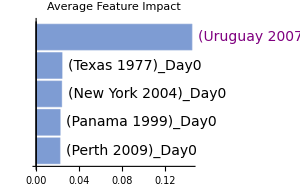
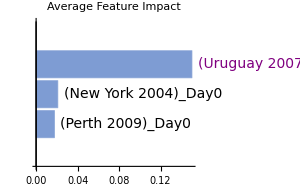
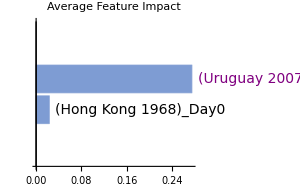
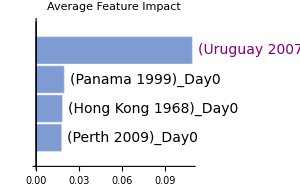
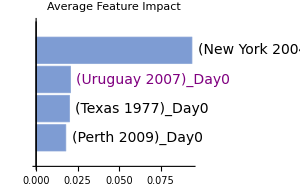
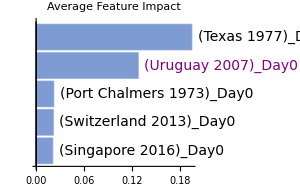
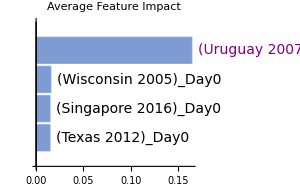
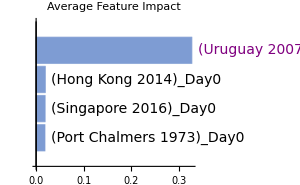
<|Fonville2014_S13→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},Fox2022HCW→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},Hinojosa2020_V2014-2015→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},UGA2016→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}|>

```mathematica
Map[
BarChart[#,ChartLabels->Placed[Automatic,After],ChartStyle->Darker[ColorData[95,1],0.1],TicksStyle->11,ImageSize->300, BarOrigin->Left,PlotLabel->"Average Feature Impact",PerformanceGoal->"Speed"]&,Association/@(Normal[#]/.{{virus_String,day_String}:>font[Subscript[stripSubtype@virusNameYear@virus,day],14,If[virus==="H3N2 A/Uruguay/716/2007",Purple,Black]]})&/@vals,{2}]
```

### Figure S5: Chord Diagram Between All Datasets

Quantifying prediction accuracy between each pair of studies. By identifying the worst-predicted datasets, we can determine what features of vaccine studies generate fundamentally different vaccine responses.

#### Panels A,B: Chord Diagrams

We first show which studies have ≥4 overlapping variants [below-left], which provides us with sufficient overlap to predict all of their data. Then we make these predictions and show the average accuracy for all variants [below-right, more transparency signifies worse prediction accuracy].

```mathematica
(* Which datasets have ≥4 overlapping viruses? They will be connected with a chord *)
virusOverlap=N@Table[
HeavisideTheta[Length@Cases[Intersection[virusAlias[viruses[tablePredictingFrom],tablePredictingFrom->tableToPredict],viruses[tableToPredict]],virus_/;virusSubtype@virus=="H3N2"]-3.5]
,{tableToPredict,Join@@listCohortsInitial},{tablePredictingFrom,Join@@listCohortsInitial}];
```

```mathematica
(*(* Mean RMSE (over all overlapping viruses) between datasets *)
Clear[meanError]
meanError[tablePredictingFrom_,tableToPredict_]:=meanError[tablePredictingFrom,tableToPredict]=Mean[Last/@virusPredict[tablePredictingFrom->tableToPredict,"Return"->"Titer"]]/._Mean:>Missing[]
(* Calculating mean RMSE, making it symmetric (representing predictions in either direction) *)
transparency=Table[
meanError[tablePredictingFrom,tableToPredict]
,{tableToPredict,Join@@listCohortsInitial},{tablePredictingFrom,Join@@listCohortsInitial}];
transparency=(transparency+transparencyᵀ)/2/.{val_?NumericQ:>(2/val)^2,_Missing->0};
Iconize[transparency]*)
transparency=;
```

```mathematica
vacYears=virusYear/@assocVaccineStrain/@Join@@listCohortsInitial;
gradient=Blend[{Lighter[RGBColor[0.5017113270778731, 0., 0.5017113982851967],0.2],RGBColor[0.18039198677354365, 0.45882344569527705, 0.7137255033670243],RGBColor[0.4738489078908023, 0.7048888088131038, 0.3916054687399008]},#]&;
colors=gradient[Rescale[#,MinMax@vacYears,{0,1}]]&/@vacYears;
```

```mathematica
Clear[showPlot]
showPlot[opacity_,emphasis_:None]:=Show[chordDiagram[virusOverlap,"TotalWidth"->190,"Colors"->colors,"BackgroundOpacity"->opacity,"WedgeEmphasis"->emphasis,"Labels"->(font[Column[label[#],Spacings->0,Alignment->Center],9]&/@Join@@listCohortsInitial)],ImageSize->350]
```

```mathematica
Row[{Grid[{{Labeled[showPlot[1],showGrid[{{Column[font[#,16,Bold]&/@{"Predictions possible","(≥4 overlapping variants)"},Alignment->Center]}}],Top],Labeled[showPlot[transparency,{Prepend[#,EdgeForm[{Thick,Darker[Red,0.1]}]]&,{{1},{2},{7}}}],showGrid[{{Column[font[#,16,Bold]&/@{"Prediction error","between two studies"},Alignment->Center]}}],Top]}},Spacings->5]," ",BarLegend[{GrayLevel[1-(2/#)^2]&,{1,8}}]}]
```

-Graphics-Predictions possible
(≥4 overlapping variants) | -Graphics-Prediction error
between two studies

#### Panel C: Distribution of Prediction Error

Distribution of prediction error for each study. While we only consider predictions forward in time throughout the majority of the paper (e.g. if Study S_1 was conducted before Study S_2, then we only use S_1 to predict S_2), in this figure we also consider backwards in time (using S_2 to predict S_1). Therefore, the distribution of RMSEs for Study S_0 show both how well other studies predict S_0 as well as how accurately S_0 predicts other studies.

```mathematica
(*(* Mean RMSE (over all overlapping viruses) between datasets *)
Clear[meanError]
meanError[tablePredictingFrom_,tableToPredict_]:=meanError[tablePredictingFrom,tableToPredict]=Mean[Last/@virusPredict[tablePredictingFrom->tableToPredict,"Return"->"Titer"]]/._Mean:>Missing[]
(* Rows represent predicting to a specific table, columns represent different tables predicting from *)
cohortError=Table[
If[NumericQ@#,#,Missing[]]&@Mean[{meanError[tableOfInterest,otherTable],meanError[otherTable,tableOfInterest]}]
,{tableOfInterest,Join@@listCohortsInitial},{otherTable,Join@@listCohortsInitial}];
Iconize[cohortError]*)
cohortError=;
```

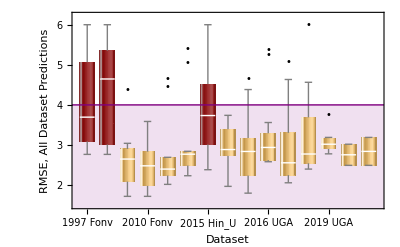

```mathematica
BoxWhiskerChart[Clip[DeleteMissing/@cohortError,{-∞,6}],{{"Outliers","•",Black}},ChartStyle->ReplacePart[ConstantArray[RGBColor[0.9843136860317651, 0.7411764840775561, 0.3254900649788416],Length@cohortError],1|2|7->Darker@Red],ChartLabels->(Rotate[font[StringRiffle[label[#]," "],14],π/2]&/@Join@@listCohortsInitial),ChartElementFunction->"GlassBoxWhisker",Epilog->{Purple,Line[{{0,4},{16,4}}]},FrameLabel->(font[#,14]&/@{"Dataset","RMSE, All Dataset Predictions"}),FrameStyle->Directive[Black,Thickness[0.002]],FrameTicksStyle->Directive[14,Black],Prolog->{LightPurple,Rectangle[{0,1},{16,4}]},PlotRange->{{0,15.7},{1,All}},PlotRangePadding->None]
```

### Figure S6: Predictions Across All Cohorts

Using our full random forest model, we quantify prediction error in each vaccine study.

#### Panel A: High Level Summary of All Predictions

Distribution of prediction error in each vaccine study, and the average prediction error of each variant in each study.

```mathematica
assoc=Association@Table[
tablesPredictingFrom=Cases[Join@@listCohortsFinal,cohort_/;1<=studyYear[tableToPredict]-studyYear[cohort]<=10];
tableToPredict->virusPredict[tablesPredictingFrom->tableToPredict,"Return"->"Titer"]
,{tableToPredict,Rest@Flatten@listCohortsFinal}];
```

```mathematica
(* Master list of all viruses (aliased) predicted across all studies *)
listViruses=SortBy[DeleteDuplicates[aliasBest/@First/@Join@@Values[assoc]],virusYear];
repViruses=MapIndexed[#->First@#2&,listViruses];
```

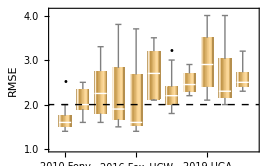

```mathematica
BoxWhiskerChart[Last/@#&/@assoc,{{"Outliers","•",Black}},ChartLabels->(Rotate[font[StringRiffle[label[#]," "],14],π/2]&/@Keys@assoc),Frame->True,FrameTicks->{{,None},Automatic},ChartElementFunction->"GlassBoxWhisker",Epilog->{Black,Dashed,Line[{{0,2},{16,2}}]},FrameStyle->Directive[Black,Thickness[0.0025]],FrameTicksStyle->Directive[12,Black],FrameLabel->font["RMSE",16],ImageSize->270,PlotRange->{{0.3,11.7},{1,4.1}},PlotRangeClipping->True,PlotRangePadding->None]
```

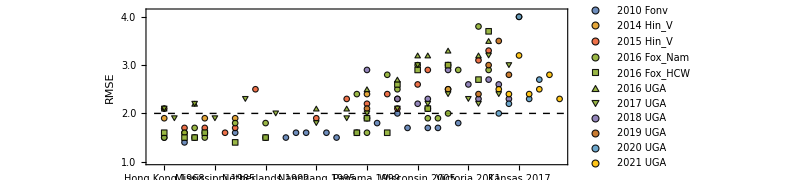

```mathematica
ListPlot[Values[assoc]/.virus_String:>(aliasBest[virus]/.repViruses),PlotMarkers->ReplacePart[ConstantArray[plotMarker[0.05,0.9,"EdgeThickness"->Small],11],{5->plotMarker[0.05,0.9,"Type"->"Square","EdgeThickness"->Small],
6->plotMarker[0.05,0.9,"Type"->"Triangle","EdgeThickness"->Small],
7->plotMarker[0.05,0.9,"Type"->"UpsideDownTriangle","EdgeThickness"->Small]}],PlotStyle->(ColorData[97]/@{1,2,4,3,3,3,3,5,6,7,8}),PlotLegends->PointLegend[Automatic,font[StringRiffle[label[#]," "],14]&/@Rest@Flatten@listCohortsFinal,LegendLayout->{"Column",1},LegendFunction->frame,Spacings->{0.4,0.2},LegendMarkerSize->8],PlotRange->{1,4.1},AspectRatio->0.3,PlotRangeClipping->False,ImageSize->600,Frame->{True,True,False,False},FrameTicks->{MapIndexed[{First@#2,Rotate[font[stripSubtype@virusNameYear@#,12],π/2],0.01}&,listViruses]/.{
"Perth 2009"->Style["Perth 2009",Darker[ColorData[97,1],0.1]],
"Texas 2012"->Style["Texas 2012",Darker[ColorData[97,2],0.1]],
"Switzerland 2013"->Style["Switzerland 2013",Darker[ColorData[97,4],0.1]],
"Hong Kong 2014"->Style["Hong Kong 2014",Darker[ColorData[97,3],0.1]],
"Singapore 2016"->Style["Singapore 2016",Darker[ColorData[97,5],0.1]],
"Kansas 2017"->Style["Kansas 2017",Darker[ColorData[97,6],0.1]],
"Hong Kong 2019"->Style["Hong Kong 2019",Darker[ColorData[97,7],0.1]],
"Tasmania 2020"->Style["Tasmania 2020",Darker[ColorData[97,8],0.1]]
},},FrameLabel->font["RMSE",16],FrameStyle->Directive[Black,Thickness[0.0012]],FrameTicksStyle->Directive[13,Black],Prolog->{{Dashed,Line[{{0.,2},{50,2}}]}}]
```

#### Panels B-L: Predictions from Each Dataset

Predictions of representative subjects from each dataset [left] together with the distribution of all variant predictions [right] in each study.

Starting:  Fonville2014_S14

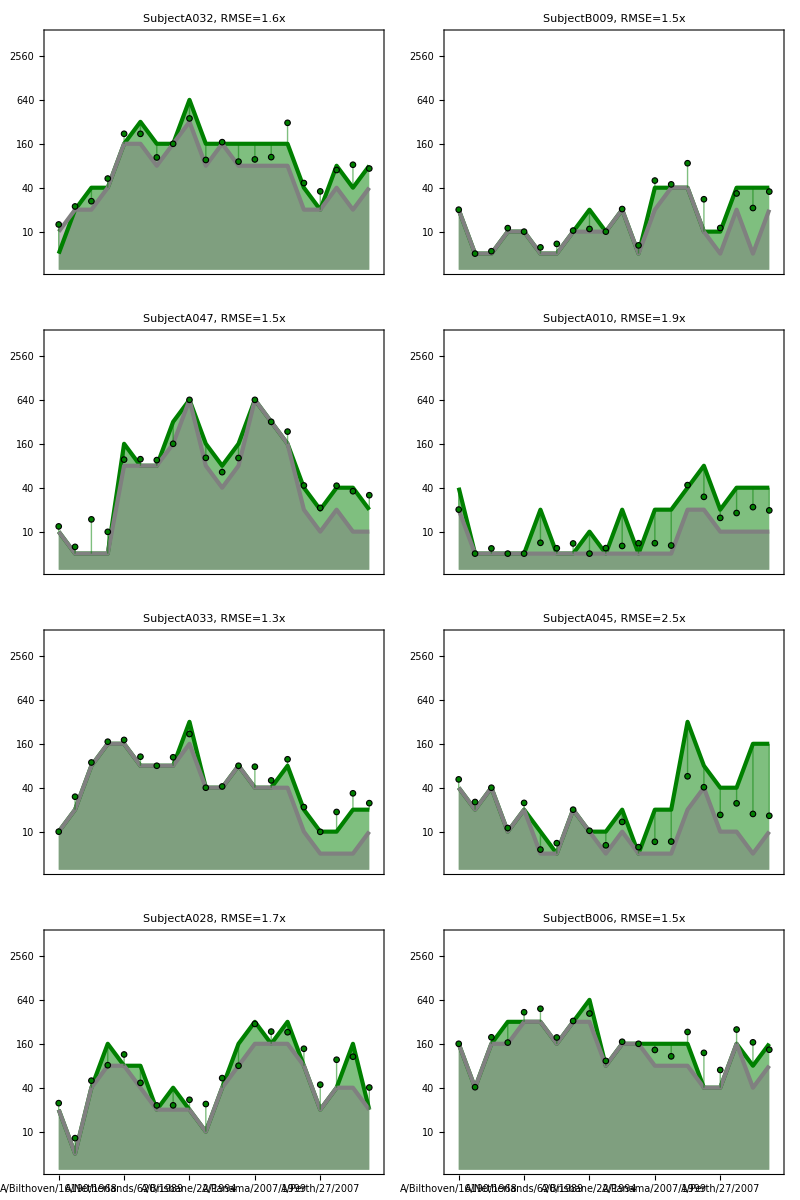
{-Graphics-,-Graphics-}

Starting:  Hinojosa2020_V2014-2015

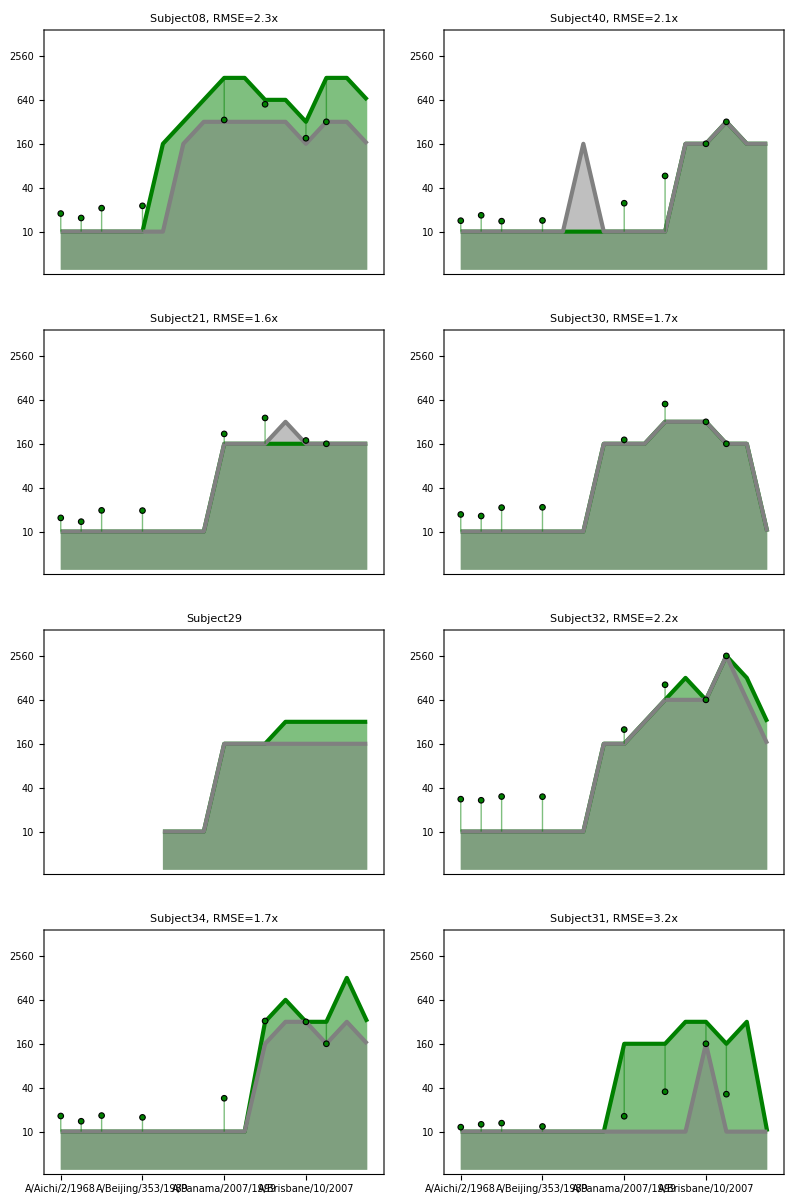
{-Graphics-,-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- |  | 
 |  |  |  | 
 |  |  |  | }

Starting:  Hinojosa2020_V2015

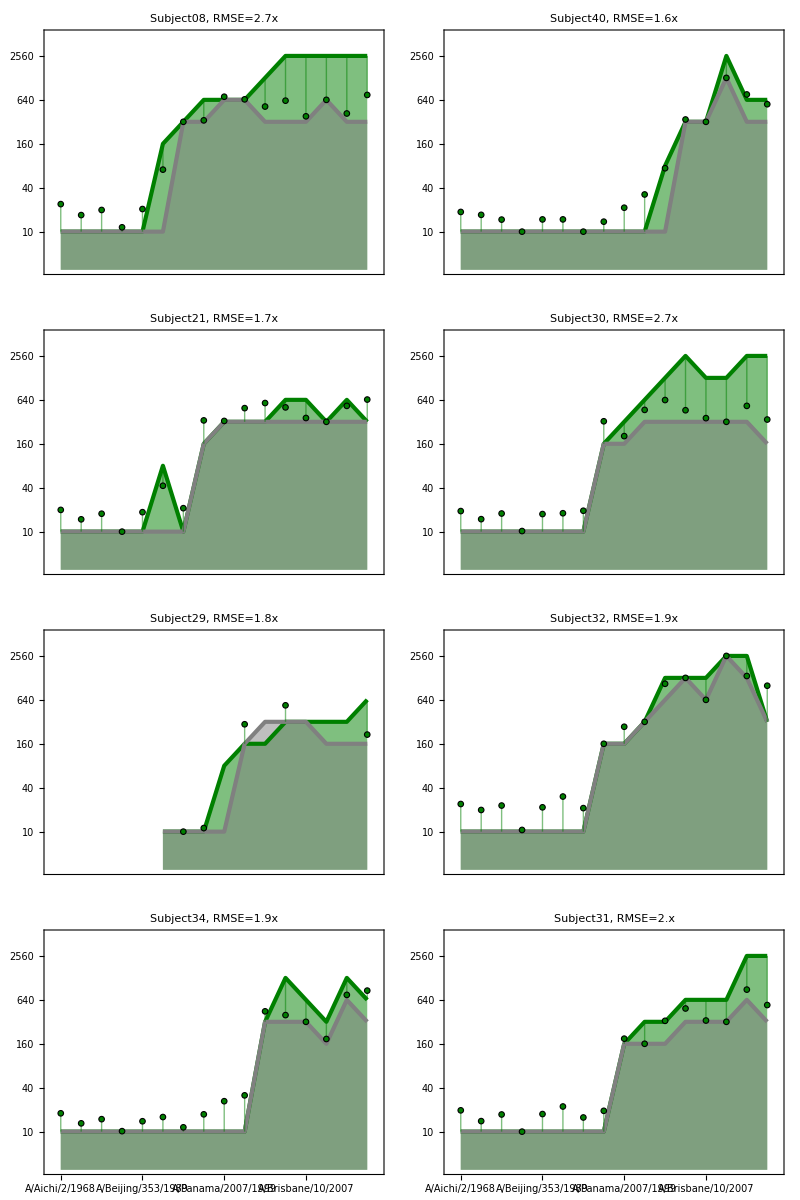
{-Graphics-,-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- |  |  |  | }

Starting:  Fox2022HaNam

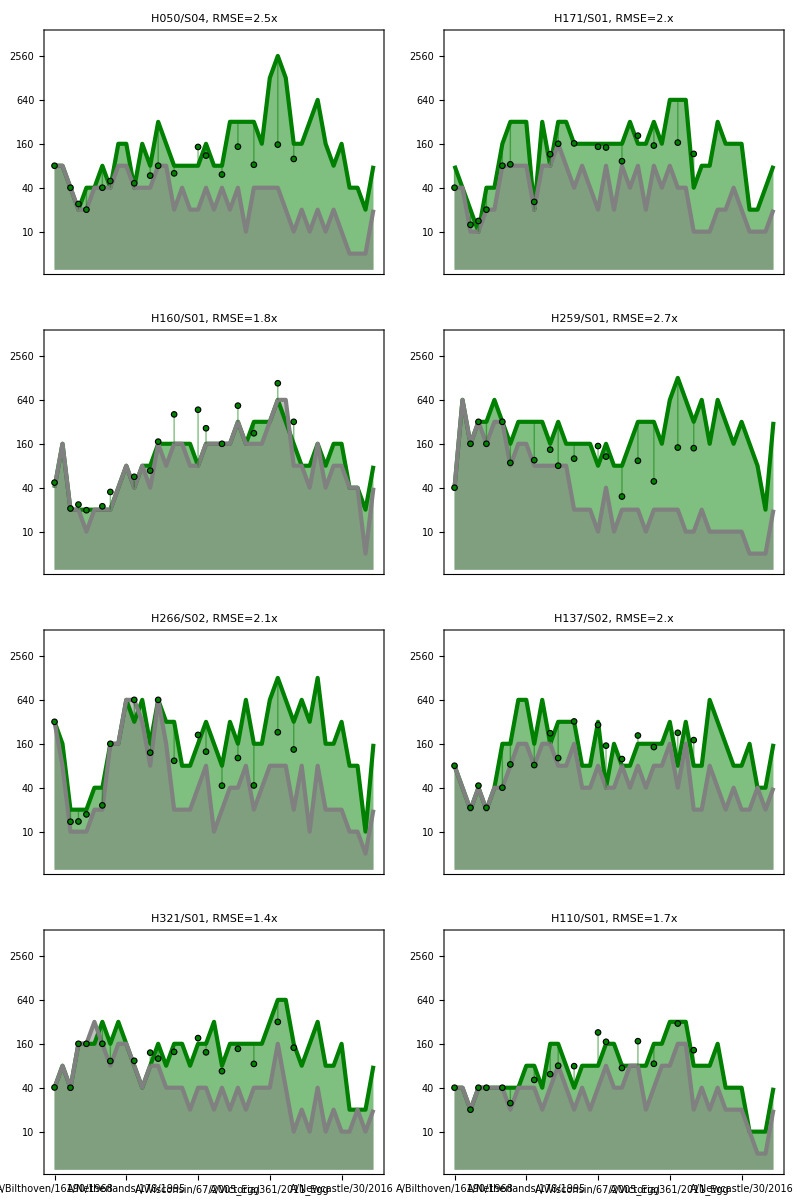
{-Graphics-,-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- |  |  | }

Starting:  Fox2022HCW

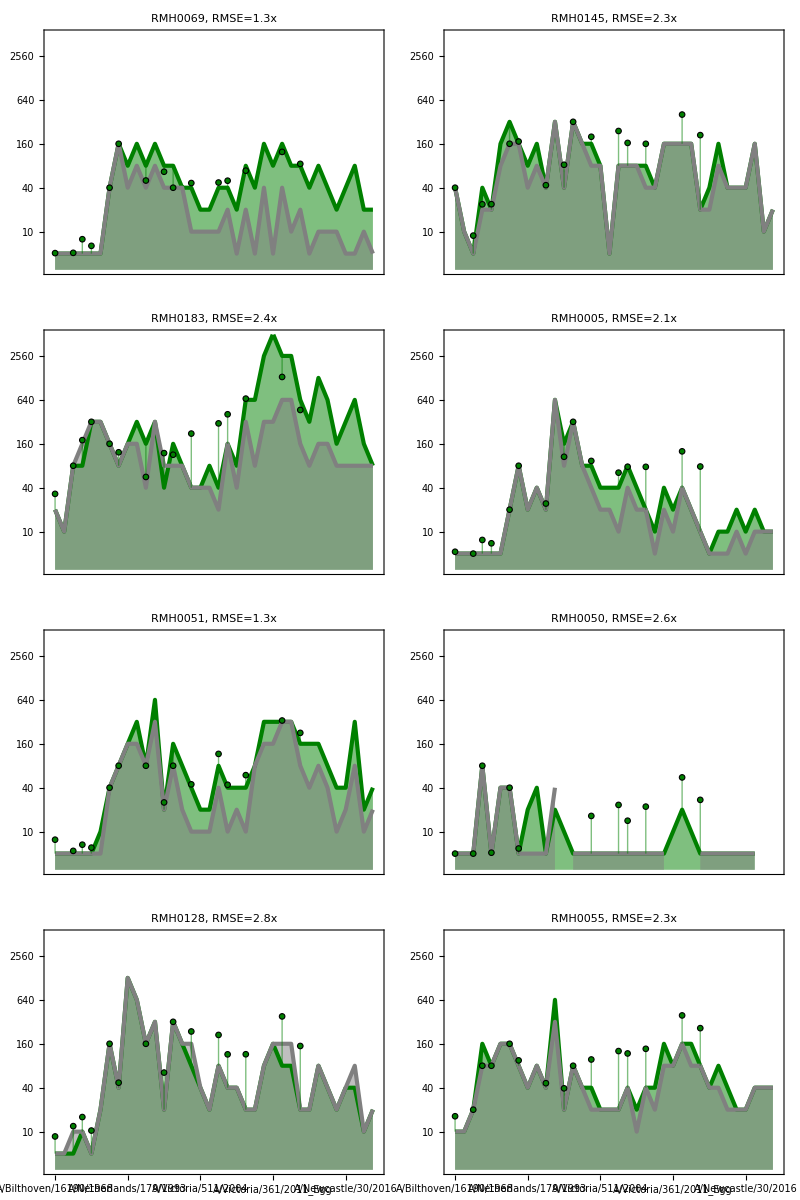
{-Graphics-,-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
 |  |  |  | }

Starting:  UGA2016

{-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-,-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- |  |  |  | 
 |  |  |  | }

Starting:  UGA2017

{-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-,-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- |  | }

Starting:  UGA2018

{-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-,-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- |  | 
 |  |  | 
 |  |  | }

Starting:  UGA2019

{-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-,-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- |  | 
 |  |  | 
 |  |  | 
 |  |  | }

Starting:  UGA2020

{-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-,-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- |  |  | 
 |  |  | 
 |  |  | 
 |  |  | }

Starting:  UGA2021

{-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-,-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | 
 |  |  | 
 |  |  | 
 |  |  | }

```mathematica
uga={"UGA2018","UGA2019","UGA2020","UGA2021"};
Do[
Echo[tableToPredict,"Starting:"];
tablesPredictingFrom=Cases[Join@@listCohortsFinal,cohort_/;1<=studyYear[tableToPredict]-studyYear[cohort]<=10];
vaccine=assocVaccineStrain@tableToPredict;
Echo@{
(* === Individual landscapes === *)
SeedRandom[12345];
listSera=RandomSample[sera[tableToPredict],8];
Grid[Partition[MapIndexed[(
serumOfInterest=#;
serumShortName=StringSplit[serumOfInterest,"_"][[1]];
If[serumShortName==="ID",serumShortName=serumShortName<>" "<>StringSplit[serumOfInterest,"_"][[2]]];
Show[showLandscape[serumOfInterest,tableToPredict,"PostVacPredict"->predictOneIndividual[tablesPredictingFrom->tableToPredict,serumOfInterest,"IncludeVirusNames"->True],"FrameTicksSize"->If[MatchQ[tableToPredict,"Fox2022HaNam"|"Fox2022HCW"],8,12],"PlotMarkerSize"->0.05,"PlotMarkerEdgeThickness"->Small,"VirusNameTicksQ"->(First@#2>=If[!MemberQ[uga,tableToPredict],7,5])][[1]]/.Thickness[0.01]->Thickness[0.013],PlotLabel->font[Row[{serumShortName,Sequence@@If[NumericQ@rmse,{", RMSE=",rmse,"x"},{}]}]],FrameTicksStyle->12,FrameStyle->Directive[Black,Thickness[0.002]],FrameLabel->None]
)&,listSera],If[!MemberQ[uga,tableToPredict],2,4]]]/.stripSubtype@vaccine->Style[stripSubtype@vaccine,Bold,Purple],
(* === Virus grid === *)
labels=virusPredict[tablesPredictingFrom->tableToPredict,"Return"->"Titer"];
SeedRandom[12345];
subset=Sort@RandomSample[Range@Length@labels,UpTo@20];
Grid[Partition[PadRight[Show[#[[1]],PlotLabel->font[Row[{stripSubtype@virusNameYear@#[[2,1]],", RMSE=",#[[2,2]],If[StringTake[ToString@#[[2,2]],-1]==".","0",""],"x"}],12,If[#[[2,1]]===vaccine,Directive[Purple,Bold],Black]],FrameLabel->None,Epilog->{},PlotRange->ConstantArray[Log10@{4,3000},2],FrameTicks->ConstantArray[Table[{Log10[5 2^(j-1)],If[EvenQ@j,5 2^(j-1),""],0.035 If[EvenQ@j,1,2/3]},{j,0,10}],2],FrameStyle->Directive[Black,Thickness[0.003]]]&/@Transpose[{DeleteCases[Flatten@virusPredict[tablesPredictingFrom->tableToPredict,"PlotType"->"Jittered",PlotMarkers->plotMarker[0.04,0.9,"EdgeThickness"->0.05]][[1,1]],""],labels}][[subset]],20,""],If[!MemberQ[uga,tableToPredict],5,4]]]
}
,{tableToPredict,Rest[Flatten@listCohortsFinal]}]
```

### Figure S7: Comparison with Null Models

We show prediction accuracy in 2017 UGA using our random forest approach, a linear model, and a null model.

#### Panel A: Comparing Models in 2017 UGA

Predicting four representative variants (A/Hong Kong/1/1968, H3N2 A/Panama/2007/1999, H3N2 A/Wisconsin/67/2005, and H3N2 A/Hong Kong/4801/2014) using all three models. Within each plot, the dots represent the predictions of the n=271 participants in this study.

```mathematica
tableToPredict="UGA2017";
tablesPredictingFrom=Cases[Join@@listCohortsFinal,cohort_/;1<=studyYear[tableToPredict]-studyYear[cohort]<=10];
(* Specific variants to show *)
subset={1,9,11,17};
plotDataForecast=virusPredict[tablesPredictingFrom->tableToPredict,"Method"->"Forecast","Return"->"TiterFull"][[subset]];
plotDataNull=virusPredict[tablesPredictingFrom->tableToPredict,"Method"->"Baseline","Return"->"TiterFull"][[subset]];
plotDataLinear=virusPredict[tablesPredictingFrom->tableToPredict,"Method"->"Linear","Return"->"TiterFull"][[subset]];
```

```mathematica
Table[
Show[plotCompletion[{plotDataForecast,plotDataLinear,plotDataNull}[[All,index,-1]],IntervalMarkersStyle->None,PlotLabel->font[Row[{stripSubtype@virusNameYear@plotDataForecast[[index,1]]}]],"σToShow"->0,"PlotRange"->ConstantArray[Log10@{4,3000},2],"ShowTiterThreshold"->∞,"PlotType"->"Jittered","RSquaredPos"->None,PlotMarkers->{plotMarker[0.04,0.9,"EdgeThickness"->0.05],plotMarker[0.025,0.9,"EdgeThickness"->0.05,"Type"->"Square"],plotMarker[0.03,0.9,"EdgeThickness"->0.05,"Type"->"Diamond"]},PlotStyle->{ColorData[97,1],GrayLevel[0.55],GrayLevel[0.85]}],PlotLabel->font[stripSubtype@virusNameYear@viruses[tableToPredict][[index]],14],Epilog->{},PlotRange->ConstantArray[Log10@{4,3000},2],FrameLabel->(font[#,14]&/@{"Measured HAI","Predicted HAI"}),FrameTicks->ConstantArray[Table[{Log10[5 2^(j-1)],If[EvenQ@j,5 2^(j-1),""],0.035 If[EvenQ@j,1,2/3]},{j,0,10}],2],FrameStyle->Directive[Black,Thickness[0.003]]]
,{index,Length@subset}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
showGrid@Prepend[
Table[
Prepend[Round[10^RootMeanSquare[Subtract@@@#],0.1]&/@{plotDataNull,plotDataLinear,plotDataForecast}[[All,index,-1]],plotDataNull[[index,1]]]
,{index,Length@subset}],
{font["RMSE",Bold],"Null","Linear","Forecast"}
]
```

RMSE | Null | Linear | Forecast
H3N2 A/Hong Kong/1/1968 | 1.4 | 1.4 | 2.1
H3N2 A/Panama/2007/1999 | 2. | 1.9 | 2.
H3N2 A/Wisconsin/67/2005 | 3.7 | 3.9 | 3.
H3N2 A/Hong Kong/4801/2014 | 3.2 | 19.1 | 2.4

#### Panel B: All Predictions

Distribution of errors when predicting all variants in 2017 UGA using each model.

```mathematica
titersForecast=Table[
tablesPredictingFrom=Cases[Join@@listCohortsFinal,cohort_/;1<=studyYear[tableToPredict]-studyYear[cohort]<=10];
virusPredict[tablesPredictingFrom->tableToPredict,"Return"->"Titer"]
,{tableToPredict,Rest[Flatten@listCohortsFinal]}];
titersBaseline=Table[
tablesPredictingFrom=Cases[Join@@listCohortsFinal,cohort_/;1<=studyYear[tableToPredict]-studyYear[cohort]<=10];
virusPredict[tablesPredictingFrom->tableToPredict,"Return"->"Titer",Method->"Baseline"]
,{tableToPredict,Rest[Flatten@listCohortsFinal]}];
titersLinear=Table[
tablesPredictingFrom=Cases[Join@@listCohortsFinal,cohort_/;1<=studyYear[tableToPredict]-studyYear[cohort]<=10];
virusPredict[tablesPredictingFrom->tableToPredict,"Return"->"Titer",Method->"Linear"]
,{tableToPredict,Rest[Flatten@listCohortsFinal]}];
```

```mathematica
MapIndexed[Histogram[Clip[Join@@#[[All,All,-1]]-0.01,{1,∞}],{0.5},PlotRange->All,ImageSize->270,ChartStyle->EdgeForm[Opacity[1]],Prolog->{LightPurple,Rectangle[{4+If[#===titersForecast,1,0],0},{100,100}]},PlotLabel->font[Switch[First@#2,1,"Random Forest",2,"Linear Model",3,"Null Model"],14],FrameLabel->(font[#,14]&/@{"RMSE of Variant","Count"}),Frame->{True,True,False,False},FrameTicksStyle->12,FrameStyle->Directive[{Black,Thickness[0.002]}]]&,{titersForecast,titersBaseline,titersLinear}]
```

{-Graphics-,-Graphics-,-Graphics-}

### Figure S8: Vaccine Strain Predictions Within/Across Datasets

Comparing vaccine strain HAI for 2016 Fox_Nam and 2016 Fox_HCW, both of which administer the same vaccine (H3N2 A/Hong Kong/4801/2014).

#### Panel B: Predicting Between the Fox Datasets with a Linear Model

Fitting a linear model to the pre-vac and post-vac HAI against the vaccine strain (H3N2 A/Hong Kong/4801/2014) in 2016 Fox_Nam and 2016 Fox_HCW. Each plot shows the model fit within that study, whereas the predictions in Panel C will use the predictions from the other study as the training set.

```mathematica
SeedRandom[12345];
vaccine=assocVaccineStrain["Fox2022HaNam"];
Table[
color=If[cohort==="Fox2022HaNam",RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.528488, 0.470624, 0.701351]];
plotData=Table[{data[{vaccine,serum,"Day0"}],data[{vaccine,serum,"Day21"}]},{serum,sera[cohort]}];
fitting[cohort]=fitPerp[Log10@plotData];Show[plot[Log10@plotData+RandomReal[0.05{-1,1},Dimensions@plotData],PlotLabel->font[StringRiffle[label[cohort]," "],17],ImageSize->250,FrameTicks->ConstantArray[MapAt[Log10,,{All,1}],2],FrameTicksStyle->12,FrameStyle->Directive[{Black,Thickness[0.004]}],PlotRange->Log10@{3,8000},PlotStyle->color,Prolog->{LightGray,Triangle[{{0,0},{4,4},{4,0}}]},PlotMarkers->{plotMarker[0.06,0.7]},FrameLabel->(font[#,14]&/@{"HAI Pre-vac, Vaccine Strain","HAI Post-vac, Vaccine Strain"})]
,Plot[fitting[cohort],{x,0,5},PlotStyle->Directive[{Darker[color,0.1],Thickness[0.04],Opacity[0.8]}]]]
,{cohort,{"Fox2022HaNam","Fox2022HCW"}}]
```

{-Graphics-,-Graphics-}

#### Panel C: Quantifying Prediction Error with a Linear Model

Comparing two different prediction approaches:

Approach 1: Using 70% of Day 0 and Day 21 data from one study to predict the remaining 30% of responses in this same study. This is a simpler but less practical prediction challenge, since it requires vaccinating a group of individuals in a season before you can predict how others would respond to the vaccine.

```mathematica
Labeled[showGrid[Prepend[Table[
fitData=Log10@Table[data[{vaccine,serum,time}],{serum,sera[cohort]},{time,{"Day0","Day21"}}];
index=Range@Length@fitData;
SeedRandom[12345];
res=Table[
training=RandomSample[index,Floor[0.7Length@index]];
fit=fitPerp[fitData[[training]]];
RootMeanSquare[#[[2]]-(fit/.x->#[[1]])&/@fitData[[Complement[index,training]]]]
,{iteration,10}];
res=10^(Mean@res);
{font[StringRiffle[label[cohort]," "]]->font[StringRiffle[label[cohort]," "]],
Switch[res,
val_/;val>100,Item[font[Row[{Round[res,10],"x"}],12,Bold],Background->Darker[Red,0.1]],
val_/;val>4,Item[font[Row[{res,"x"}],12,Bold],Background->Darker[Red,0.1]],
_,ToString@Round[res,0.1]<>"x"
]}
,{cohort,{"Fox2022HaNam","Fox2022HCW"}}],font[#,12,Bold]&/@{"Cohort","   Error   "}],Dividers->{{GrayLevel[0],{RGBColor[0.75, 0.75, 0.75]},GrayLevel[0]},{GrayLevel[0],{RGBColor[0.75, 0.75, 0.75]},GrayLevel[0]}}]/.GrayLevel[0.9400000000000001]->White,font["Within-Dataset Predictions",14,Bold],Top]
```

Cohort |    Error   
2016 Fox_Nam→2016 Fox_Nam | 120x
2016 Fox_HCW→2016 Fox_HCW | 2.9xWithin-Dataset Predictions

Approach 2: Using 0% of Day 21 data and only training using the other study. This represents a realistic prediction challenge, with training done exclusively on one study and then used to predict another study. We note, however, that in this case both studies were conducted in the same year (2016). Hence, this example primarily serves to illustrate the point that vaccine responses can be markedly different across studies.

```mathematica
cohorts={"Fox2022HaNam","Fox2022HCW"};
assoc=Association@Table[
fitData=Log10@Table[data[{vaccine,serum,time}],{serum,sera[First@DeleteCases[cohorts,cohortOfInterest]]},{time,{"Day0","Day21"}}];
fit=fitPerp[fitData];
predictData=Log10@Table[data[{vaccine,serum,time}],{serum,sera[cohortOfInterest]},{time,{"Day0","Day21"}}];
cohortOfInterest->Round[10^RootMeanSquare[#[[2]]-(fit/.x->#[[1]])&/@predictData],0.1]
,{cohortOfInterest,cohorts}];
Labeled[showGrid[Prepend[Table[
{font[StringRiffle[label[First@DeleteCases[cohorts,cohortOfInterest]]," "]->StringRiffle[label[cohortOfInterest]," "]],
res=assoc[cohortOfInterest];
Switch[res,
val_/;val>100,Item[font[Row[{Round[res,10],"x"}],12,Bold],Background->Darker[Red,0.1]],
val_/;val>4,Item[font[Row[{res,"x"}],12,Bold],Background->Darker[Red,0.1]],
_,Row[{res,"x"}]
]
},{cohortOfInterest,cohorts}],font[#,12,Bold]&/@{"Cohort","   Error   "}],Dividers->{{GrayLevel[0],{RGBColor[0.75, 0.75, 0.75]},GrayLevel[0]},{GrayLevel[0],{RGBColor[0.75, 0.75, 0.75]},GrayLevel[0]}}]/.GrayLevel[0.9400000000000001]->White,font["Cross-Dataset Predictions",14,Bold],Top]
```

Cohort |    Error   
2016 Fox_HCW→2016 Fox_Nam | 5.9x
2016 Fox_Nam→2016 Fox_HCW | 280xCross-Dataset Predictions

### Figure S9: Predictions for New Vaccine Studies

Predicting each variant in our four new vaccine studies.

Note: Although for this study we analyzed only 25 participants from the 2022-2023 UGA studies, we measured the full cohort (n=245 in 2022 UGA and n=234 in 2023 UGA), as well as three other cohorts of vaccinees receiving Flucelvax (2022 and 2023) or FluAd (2023). Since we had these full data, we decided to use the full 2022 UGA data when making the 2023 UGA and 2023 Crotty_Afluria predictions, even though we still only show the results for the 25 individuals from our original sample. All of these datasets will be posted in full within our associated GitHub once they are publicly available.

As a result, there will be some discrepancies between the results below and the figures in the paper, especially for the linear model. Moreover, when making the specialized 2023 Crotty_Afluria predictions, we ultimately found that the best predictions come from training upon the three Flucelvax and FluAd datasets from 2022-2023; those results are not shown below, but we include the process we used to determine these best studies.

```mathematica
{xx,yy,Δy}={0.65,2.95,0.3};
ft=12;
listViruses={"H3N2 A/Darwin/9/2021","H3N2 A/Tasmania/503/2020","H3N2 A/Hong Kong/2671/2019","H3N2 A/South Australia/34/2019","H3N2 A/Kansas/14/2017","H3N2 A/Singapore/INFIMH-160019/2016","H3N2 A/Hong Kong/4801/2014"};
repColor=Thread[listViruses->ColorData[97]/@Range@7];
```

#### Panel C: 2023 Crotty_FluMist

```mathematica
tableToPredict="Crotty2023FM";
tablesPredictingFrom=Cases[Append[Join@@listCohortsFinal,"UGA2022Sample"],cohort_/;1<=studyYear[tableToPredict]-studyYear[cohort]<=10];
plotDataNull=Rule@@@virusPredict[tablesPredictingFrom->tableToPredict,"Method"->"Baseline","Return"->"TiterFull"];
plotDataLinear=Rule@@@virusPredict[tablesPredictingFrom->tableToPredict,"Method"->"Linear","Return"->"TiterFull"];
```

```mathematica
Echo["","2023 Crotty_FluMist"];
Table[
plotData=virus/.{plotDataLinear,plotDataNull};
Show[plotCompletion[plotData,IntervalMarkersStyle->None,"σToShow"->RootMeanSquare[Subtract@@@plotData[[-1]]],"PlotRange"->ConstantArray[Log10@{3,1500},2],"ShowTiterThreshold"->∞,"PlotType"->"Jittered","RSquaredPos"->None,PlotMarkers->{plotMarker[0.025,0.9,"EdgeThickness"->0.05,"Type"->"Square"],plotMarker[0.03,0.9,"EdgeThickness"->0.05,"Type"->"Diamond"]},PlotStyle->{GrayLevel[0.55],GrayLevel[0.85]}],PlotLabel->font[stripSubtype@virusNameYear@virus,13],FrameLabel->(font[#,13]&/@{"Measured HAI","Predicted HAI"}),Epilog->{
mean=10^RootMeanSquare[Subtract@@@plotData[[1]]];
CI=confidenceInterval[Subtract@@@plotData[[1]],10^RootMeanSquare[#]&,1000];
Text[font[Row[{"RMSE_L=",Subsuperscript[Row[{Round[mean,0.1],"x"}],-Round[mean-CI[[1]],0.1],Round[CI[[2]]-mean,0.1]]}],ft],{xx,yy-Δy},{-1,0},Background->Directive[White,Opacity[0.7]]],
mean=10^RootMeanSquare[Subtract@@@plotData[[2]]];
CI=confidenceInterval[Subtract@@@plotData[[2]],10^RootMeanSquare[#]&,1000];
Text[font[Row[{"RMSE_N=",Subsuperscript[Row[{format[Round[mean,0.1],1],"x"}],-Round[mean-CI[[1]],0.1],Round[CI[[2]]-mean,0.1]]}],ft],{xx,yy-2Δy},{-1,0},Background->Directive[White,Opacity[0.7]]]
},FrameTicks->{{Join[Table[{Log10[5 2.^(j-1)],5 2^(j-1),0.025},{j,-3,10}],Join@@Table[{Log10[k 2.^(j-1)],"",0.025 0.25},{j,-3,10},{k,6,9,1}]],None},{Table[{Log10[5. 2^(j-1)],5 2^(j-1),0.025},{j,-3,10}],None}},FrameStyle->Directive[Black,Thickness[0.003]]]
,{virus,listViruses}]
```

2023 Crotty_FluMist

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### Panels A, B, D: 2022-2023 UGA, 2023 Crotty_Afluria

```mathematica
Do[
Echo["",tableToPredict];
tablesPredictingFrom=Cases[Append[Join@@listCohortsFinal,"UGA2022Sample"],cohort_/;1<=studyYear[tableToPredict]-studyYear[cohort]<=10];
plotDataForecast=Rule@@@virusPredict[tablesPredictingFrom->tableToPredict,"Method"->"Forecast","Forest"->leaveOneOut,"Return"->"TiterFull"];
plotDataNull=Rule@@@virusPredict[tablesPredictingFrom->tableToPredict,"Method"->"Baseline","Return"->"TiterFull"];
plotDataLinear=Rule@@@virusPredict[tablesPredictingFrom->tableToPredict,"Method"->"Linear","Return"->"TiterFull"];
Echo@Row@Table[
plotData=virus/.{plotDataForecast,plotDataLinear,plotDataNull};
If[MatchQ[plotData,{_String..}],
"",
Show[plotCompletion[plotData,IntervalMarkersStyle->None,"σToShow"->RootMeanSquare[Subtract@@@plotData[[1]]],"PlotRange"->ConstantArray[Log10@{3,1500},2],"ShowTiterThreshold"->∞,"PlotType"->"Jittered","RSquaredPos"->None,PlotMarkers->{plotMarker[0.05,0.8],plotMarker[0.025,0.9,"EdgeThickness"->0.05,"Type"->"Square"],plotMarker[0.03,0.9,"EdgeThickness"->0.05,"Type"->"Diamond"]},PlotStyle->{virus/.repColor,GrayLevel[0.55],GrayLevel[0.85]}],PlotLabel->font[stripSubtype@virusNameYear@virus,13],FrameLabel->(font[#,13]&/@{"Measured HAI","Predicted HAI"}),Epilog->{
mean=10^RootMeanSquare[Subtract@@@plotData[[1]]];
CI=confidenceInterval[Subtract@@@plotData[[1]],10^RootMeanSquare[#]&,1000];
Text[font[Row[{"RMSE_F=",Subsuperscript[Row[{Round[mean,0.1],"x"}],-Round[mean-CI[[1]],0.1],Round[CI[[2]]-mean,0.1]]}],ft],{xx,yy},{-1,0},Background->Directive[White,Opacity[0.7]]],
mean=10^RootMeanSquare[Subtract@@@plotData[[2]]];
CI=confidenceInterval[Subtract@@@plotData[[2]],10^RootMeanSquare[#]&,1000];
Text[font[Row[{"RMSE_L=",Subsuperscript[Row[{Round[mean,0.1],"x"}],-Round[mean-CI[[1]],0.1],Round[CI[[2]]-mean,0.1]]}],ft],{xx,yy-Δy},{-1,0},Background->Directive[White,Opacity[0.7]]],
mean=10^RootMeanSquare[Subtract@@@plotData[[3]]];
CI=confidenceInterval[Subtract@@@plotData[[3]],10^RootMeanSquare[#]&,1000];
Text[font[Row[{"RMSE_N=",Subsuperscript[Row[{format[Round[mean,0.1],1],"x"}],-Round[mean-CI[[1]],0.1],Round[CI[[2]]-mean,0.1]]}],ft],{xx,yy-2Δy},{-1,0},Background->Directive[White,Opacity[0.7]]]
},FrameTicks->{{Join[Table[{Log10[5 2.^(j-1)],5 2^(j-1),0.025},{j,-3,10}],Join@@Table[{Log10[k 2.^(j-1)],"",0.025 0.25},{j,-3,10},{k,6,9,1}]],None},{Table[{Log10[5. 2^(j-1)],5 2^(j-1),0.025},{j,-3,10}],None}},FrameStyle->Directive[Black,Thickness[0.003]]]
]
,{virus,listViruses}]
,{tableToPredict,{"UGA2022Sample","UGA2023Sample","Crotty2023Afluria"}}]
```

UGA2022Sample

-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

UGA2023Sample

-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

Crotty2023Afluria

-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

#### Determining Best Datasets for Specialized 2023 Crotty Afluria Predictions

Since 2023 UGA was measured before 2023 Crotty_Afluria, we can determine which subset of studies best predicted the former and use those datasets to predict the later. These “specialized” predictions are a proxy for having a small subset of participants who get vaccinated early in the season, or alternatively they represent the extra knowledge we could have from southern hemisphere vaccine studies conducted 6 months before the northern hemisphere influenza season.

As stated above, we only consider the 2019-2022 UGA studies. However, in our final analysis we included the full 2022 UGA data as well as 2022-2023 Flucelvax (FC) and 2023 FluAd (FA) studies, which could be added below as shown in comments: "FC2022","FC2023","FA2023"

```mathematica
(* Removing Hong Kong 2014 that cannot be predicted from 2022 UGA *)
listViruses={"H3N2 A/Singapore/INFIMH-160019/2016","H3N2 A/Kansas/14/2017","H3N2 A/Hong Kong/2671/2019","H3N2 A/South Australia/34/2019","H3N2 A/Tasmania/503/2020","H3N2 A/Darwin/9/2021"};
(* Training on 2019-2023 datasets, testing on UGA2023Sample *)
bestTables=SortBy[Table[
res=completionPredictions[{#,"UGA2023Sample"},"OtherTables"->tables,"Forest"->leaveOneOut,"PredictAbEvolution"->("Day21"|"Day28"->{"Day0"}),"Return"->"Titers"]&/@listViruses;
If[Length@res=!=Length@DeleteMissing@res,
Nothing,
{tables,Mean[RootMeanSquare[Subtract@@@#]&/@res]}
]
,{tables,Subsets[{"UGA2019","UGA2020","UGA2021","UGA2022Sample"(*,"FC2022","FC2023","FA2023"*)},{1,∞}]}],Last];
bestTables[[;;UpTo@5]]//Grid
```

{UGA2020,UGA2021} | 0.358032
{UGA2021} | 0.360996
{UGA2020,UGA2021,UGA2022Sample} | 0.362544
{UGA2019,UGA2020,UGA2021} | 0.371459
{UGA2021,UGA2022Sample} | 0.37308

Given these datasets, the combination of 2020-2021 UGA should have the best predictive power for 2023 studies, and hence we apply them to create the “specialized” prediction for 2023 Crotty_Afluria. When using all datasets, the best choice ended up being tablesPredictingFrom={"FC2022","FC2023","FA2023"}

```mathematica
tablesPredictingFrom={"UGA2020","UGA2021"};
virusPredict[tablesPredictingFrom->"Crotty2023Afluria","Return"->"Titer"]
```

{{H3N2 A/Hong Kong/4801/2014,1.7},{H3N2 A/Singapore/INFIMH-160019/2016,1.7},{H3N2 A/Kansas/14/2017,1.6},{H3N2 A/Hong Kong/2671/2019,2.5},{H3N2 A/South Australia/34/2019,1.8},{H3N2 A/Tasmania/503/2020,2.},{H3N2 A/Darwin/9/2021,3.}}

### Figure S10: Recouping Known Response Features

We demonstrate how well the model can recoup two observed phenomena in vaccine responses.

#### Panel A: Vaccine responses are slightly enhanced by recent infections

2016 Fox_Nam showed that individuals who had a confirmed influenza infection during the last five years had slightly elevated vaccine responses compared to those who had no known infections within this time frame. We compare the predicted effect using our model (below-left) and the experimentally-measured effect (below-right).

```mathematica
tableToPredict="Fox2022HaNam";
tablesPredictingFrom=Cases[Join@@listCohortsFinal,cohort_/;1<=studyYear[tableToPredict]-studyYear[cohort]<=10];
```

```mathematica
(* Individuals from 2016 Subscript[Fox, Nam] whose last known infection was >5 years prior (before 2010) *)
sera["Fox2022HaNamBefore2010"]=;
(* Individuals from 2016 Subscript[Fox, Nam] whose last known infection was within the past 5 years (after 2010) *)
sera["Fox2022HaNamAfter2010"]=;
```

```mathematica
res=virusPredict[tablesPredictingFrom->tableToPredict,"Return"->"TiterFull"];
resPriorInfectBefore2010=res;
resPriorInfectBefore2010[[All,-1]]=resPriorInfectBefore2010[[All,-1,Join@@Position[sera["Fox2022HaNam"],Alternatives@@sera["Fox2022HaNamBefore2010"]]]];
resPriorInfectAfter2010=res;
resPriorInfectAfter2010[[All,-1]]=resPriorInfectAfter2010[[All,-1,Join@@Position[sera["Fox2022HaNam"],Alternatives@@sera["Fox2022HaNamAfter2010"]]]];
```

```mathematica
plotDataBefore2010Measured={virusYear[#[[1]]],Mean@DeleteMissing[First/@#[[2]]]}&/@resPriorInfectBefore2010;
plotDataBefore2010Predicted={virusYear[#[[1]]],Mean@DeleteMissing[Last/@#[[2]]]}&/@resPriorInfectBefore2010;
(* Showing both 1976 viruses *)
plotDataBefore2010Measured[[2,1]]-=0.5;
plotDataBefore2010Measured[[3,1]]+=0.5;
plotDataBefore2010Predicted[[2,1]]-=0.5;
plotDataBefore2010Predicted[[3,1]]+=0.5;
(* Un-logging titers *)
plotDataBefore2010Measured[[All,2]]=10^plotDataBefore2010Measured[[All,2]];
plotDataBefore2010Predicted[[All,2]]=10^plotDataBefore2010Predicted[[All,2]];
```

```mathematica
plotDataAfter2010Measured={virusYear[#[[1]]],Mean@DeleteMissing[First/@#[[2]]]}&/@resPriorInfectAfter2010;
plotDataAfter2010Predicted={virusYear[#[[1]]],Mean@DeleteMissing[Last/@#[[2]]]}&/@resPriorInfectAfter2010;
(* Showing both 1976 viruses *)
plotDataAfter2010Measured[[2,1]]-=0.5;
plotDataAfter2010Measured[[3,1]]+=0.5;
plotDataAfter2010Predicted[[2,1]]-=0.5;
plotDataAfter2010Predicted[[3,1]]+=0.5;
(* Un-logging titers *)
plotDataAfter2010Measured[[All,2]]=10^plotDataAfter2010Measured[[All,2]];
plotDataAfter2010Predicted[[All,2]]=10^plotDataAfter2010Predicted[[All,2]];
```

```mathematica
{green,blue}={Darker[Green,0.4],Lighter[ColorData[97,1],0.1]};
opts={PlotRange->{20,900},Filling->{1->{{2},{Directive[{Opacity[0.3],green}],Directive[{Opacity[0.3],blue}]}}},FrameTicks->{,Table[{5 2^j,5 2^j,0.02},{j,0,9}]},FrameTicksStyle->14,ImageSize->300,Frame->{True,True,False,False},FrameStyle->Directive[Black,Thickness[0.0035]],ScalingFunctions->"Log",Joined->True,PlotMarkers->plotMarker[0.045,"EdgeThickness"->Small]};
plotPredicted=ListPlot[{plotDataBefore2010Predicted,plotDataAfter2010Predicted},PlotStyle->{blue,green},Evaluate@opts];
plotMeasured=ListPlot[{plotDataBefore2010Measured,plotDataAfter2010Measured},PlotStyle->{Directive[{blue,Dashed}],Directive[{green,Dashed}]},PlotMarkers->plotMarker[0.045,"Type"->"Square","EdgeThickness"->Small],Evaluate@opts];
Grid[{{plotPredicted,plotMeasured}},Spacings->3]
```

-Graphics- | -Graphics-

#### Panel B: Antibody Ceiling Effect

Another well-known phenomenon is the antibody ceiling effect, which states that individuals that have higher pre-vaccination HAI against the vaccine strain will tend to have smaller fold-change post-vaccination. Here, we extend this effect to other variants and show how well the model can recoup the antibody ceiling effect against all variants in all studies.

```mathematica
tableToPredict="Fonville2014_S14";
vaccine=assocVaccineStrain[tableToPredict];
plotDataMeasured=Cases[Table[
{Log10@data[{vaccine,serum,"Day0"}],Log10@(data[{vaccine,serum,"Day28p"}]/data[{vaccine,serum,"Day0"}])},
{serum,sera[tableToPredict]}],{_?NumericQ,_?NumericQ}];
tablesPredictingFrom=Cases[Join@@listCohortsFinal,cohort_/;1<=studyYear[tableToPredict]-studyYear[cohort]<=10];
(* {Measured, Predicted} post-vac titers *)
predictions=virusPredict[tablesPredictingFrom->tableToPredict,"Return"->"TiterFull"];
plotDataFull=Flatten/@Transpose@{Table[data[{vaccine,serum,"Day0"}],{serum,sera[tableToPredict]}],10^predictions[[-2,2]]};
plotDataFull=DeleteMissing[plotDataFull,1,All];
plotDataMeasured=Log10@{#[[1]],(#[[2]])/(#[[1]])}&/@plotDataFull;
plotDataPredicted=Log10@{#[[1]],(#[[3]])/(#[[1]])}&/@plotDataFull;
fitPredicted=Fit[plotDataPredicted,{1,x},x];
fitMeasured=Fit[plotDataMeasured,{1,x},x];
SeedRandom[12345];
colors={Darker[ColorData[97,2],0.2],Directive[{Dashed,Thickness[0.007],ColorData[97,1]}]};
Show[ListPlot[{#+RandomReal[0.1{-1,1},Dimensions@#]&@plotDataMeasured,#+RandomReal[0.1{-1,1},Dimensions@#]&@plotDataPredicted},PlotMarkers->{plotMarker[0.05,0.8,"Type"->"Triangle","EdgeThickness"->Small],plotMarker[0.05,0.9,"Type"->"UpsideDownTriangle","EdgeThickness"->Small]},PlotStyle->colors,PlotRange->{{0.5,2.01},{-0.15,2.}},Frame->{True,True,False,False},FrameLabel->(font[#,14]&/@{"HAI_(Day 0)","HAI_(Day 28) / HAI_(Day 0)"}),FrameTicksStyle->14,FrameTicks->{Table[{Log10[5 2^(j-1)],5 2^(j-1),0.02},{j,0,10}],Join[Table[{Log10@(2.^j),2^j,0.02},{j,0,10}],Table[{Log10@(2.^(j+0.5)),"",0.012},{j,0,10}]]},FrameStyle->Directive[Black,Thickness[0.0025]],Prolog->{Lighter[LightPurple,0.5],Rectangle[Scaled[{0,0}],Scaled[{1,1}]]}],Plot[{fitMeasured,fitPredicted},{x,0,3},PlotStyle->{Directive[{Darker[ColorData[97,2],0.2],Thickness[0.015]}],Directive[{Lighter[ColorData[97,1],0.25],Thickness[0.015]}]}]]
```

-Graphics-

```mathematica
Prepend[Table[
res=Association[#[[1,1]]->#[[All,{2,3}]]&/@GatherBy[Cases[Flatten[Table[
{aliasBest@virus,Log10@data[{virus,serum,"Day0"}],Log10@(data[{virus,serum,"Day28p"}]/data[{virus,serum,"Day0"}])},
{virus,Cases[viruses[tableToPredict],virus_/;virusSubtype@virus=="H3N2"]},
{serum,sera[tableToPredict]}],1],{_String,_?NumericQ,_?NumericQ}],First]];
plotDataMeasured=D[Fit[#,{1,x},x],x]&/@res;
tablesPredictingFrom=Cases[Join@@listCohortsFinal,cohort_/;1<=studyYear[tableToPredict]-studyYear[cohort]<=10];
(* {Measured, Predicted} post-vac titers *)
predictions=virusPredict[tablesPredictingFrom->tableToPredict,"Return"->"TiterFull"];
(* {Virus, {Log10@Subscript[Day0, Measured], Log10@Subscript[Day28, Predicted]}} *)
res={aliasBest@#[[1]],Cases[{Log10@Table[data[{#[[1]],serum,"Day0"}],{serum,sera[tableToPredict]}],#[[2,All,-1]]}ᵀ,{_?NumericQ..}]}&/@predictions;
(* Convert to fold-change: {Log10@Subscript[Day0, Measured], Log10@Subscript[Day28, Predicted]-Log10@Subscript[Day0, Measured]} *)
predictedFoldChange=MapAt[{#[[1]],#[[2]]-#[[1]]}&/@#&,res,{All,2}];
plotDataFull=Association[Rule@@@predictedFoldChange];
plotDataPredicted=D[Fit[#,{1,x},x],x]&/@plotDataFull;
overlap=SortBy[Intersection[Keys@plotDataMeasured,Keys@plotDataPredicted],virusYear];
ListPlot[{plotDataPredicted/@overlap,plotDataMeasured/@overlap},Frame->True,PlotStyle->{Darker[ColorData[97,1],0.1],Directive[{Dashed,Thickness[0.007],Darker[ColorData[97,2],0.05]}]},FrameLabel->font["Slope",14],FrameTicks->{{,Automatic},{MapIndexed[{First@#2,Rotate[font[stripSubtype@virusNameYear@#],π/2],0.01}&,overlap],None}},FrameTicksStyle->12,ImageSize->450,AspectRatio->0.2,Joined->True,PlotMarkers->{plotMarker[0.12,"EdgeThickness"->Small],plotMarker[0.1,"Type"->"Square","EdgeThickness"->Small]},PlotRange->{{0.4,Length@overlap+0.5},{-0.605,0.2}},FrameStyle->Directive[Black,Thickness[0.0025]],Epilog->{Text[font[StringRiffle[label@tableToPredict," "],14,Bold],Scaled[{0.032,0.2}],{-1,0}]}]
,{tableToPredict,Rest[Flatten@listCohortsFinal]}],PointLegend[ColorData[97]/@Range@2,font[#,14]&/@{"Predicted","Measured"},LegendLabel->Placed[font["Antibody Ceiling",14],Above],LegendFunction->frame]]
```

{,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### Figure S11: Robustly Strong/Weak Responses - Rerun now that peaksQ has been updated

Note: Since “strong” and “weak” vaccine responses are sometimes characterized using their fold-change rather than the absolute post-vaccination titers, for this figure we used a different definition of strong and weak based on fold-change.

We identified individuals who not only exhibited a strong fold-change response (HAI fold-change≥8 against at least 2 variants) or a weak fold-change response (HAI fold-change>4 against at most 1 variant), but where any perturbation of their pre-vaccination HAI landscape was also predicted to have this same strong/weak fold-change response. More precisely, we took each person’s HAI against all measured variants, systematically multiplied or divided each of these HAIs by 2, and then asked whether a support vector machine (SVM) or a nearest neighbors model (trained on all responses from that study) predicted that these perturbed states were also strong/weak. We considered a state to be robustly strong or robustly weak if ≥75% of perturbed states were the same as the unperturbed state.

#### Panel A: Examples of robustly strong/weak through SVM and Nearest Neighbor

We first identify all robustly strong and robustly weak states.

```mathematica
(* Fold-change ≥8 for at least two variants *)
largeFoldChange=Join@@Table[
Cases[sera[cohort],serum_/;
RankedMax[DeleteMissing@Table[data[{virus,serum,"Day28p"}]/data[{virus,serum,"Day0"}],{virus,viruses[cohort]}],2]>=8
]
,{cohort,Join@@listCohortsFinal}];
(* Fold-change ≤2 for all variants (except at most 1) *)
smallFoldChange=Join@@Table[
Cases[sera[cohort],serum_/;
RankedMax[DeleteMissing@Table[data[{virus,serum,"Day28p"}]/data[{virus,serum,"Day0"}],{virus,viruses[cohort]}],2]<=2
]
,{cohort,Join@@listCohortsFinal}];
```

```mathematica
Clear[landscape]
landscape[serum_]:=Table[data[{virus,serum,"Day0"}],{virus,viruses[findCohort@serum]}]/.val_?NumericQ:>Log10[val]
Clear[analyze]
analyze[tableOfInterest_,method_]:=Block[{class1,class2,n1,n2,listSeraStrong,listSeraWeak,listViruses,tuples,classify,res,robustStrong,robustWeak},
listViruses=viruses[tableOfInterest];
{class1,class2}={Cases[largeFoldChange,serum_/;MemberQ[sera[tableOfInterest],serum]:>(Table[data[{virus,serum,"Day0"}],{virus,listViruses}]/.val_?NumericQ:>Log10[val])],Cases[smallFoldChange,serum_/;MemberQ[sera[tableOfInterest],serum]:>(Table[data[{virus,serum,"Day0"}],{virus,listViruses}]/.val_?NumericQ:>Log10[val])]};
{n1,n2}=Length/@{class1,class2};
listSeraStrong=Cases[largeFoldChange,serum_/;MemberQ[sera[tableOfInterest],serum]];
listSeraWeak=Cases[smallFoldChange,serum_/;MemberQ[sera[tableOfInterest],serum]];
tuples=Join[{ConstantArray[0,Length@listViruses]},Permutations[Append[ConstantArray[0,Length@listViruses-1],Log10[2.]]],Permutations[Append[ConstantArray[0,Length@listViruses-1],Log10[1/2.]]]];
SeedRandom[12435];
res=Table[
classify=Classify[Join[Thread[class1->"Strong"],Thread[RandomSample[class2,UpTo[Round[1.5n1]]]->"Weak"]],TrainingProgressReporting->None];
{
{#,1/(N@Length@tuples)Length@Cases[classify[DeleteDuplicates@Clip[tuples+Threaded[landscape@#],{Log10[2.],∞}]],"Strong"]}&/@listSeraStrong,
{#,1/(N@Length@tuples)Length@Cases[classify[DeleteDuplicates@Clip[tuples+Threaded[landscape@#],{Log10[2.],∞}]],"Weak"]}&/@listSeraWeak
}
,{5}];
robustStrong=ReverseSortBy[
Mean/@GatherBy[Join@@res[[All,1]],First]
,Last];
robustWeak=ReverseSortBy[
Mean/@GatherBy[Join@@res[[All,2]],First]
,Last];
{robustStrong,robustWeak}
]
```

```mathematica
(* Find the robustly strong and robustly weak responses in each UGA study *)
listStudies={"UGA2016","UGA2017","UGA2018","UGA2019","UGA2020","UGA2021"};
Do[
{robustStrongNearestNeighbors[tableOfInterest],robustWeakNearestNeighbors[tableOfInterest]}=analyze[tableOfInterest,"NearestNeighbors"];
{robustStrongKernel[tableOfInterest],robustWeakKernel[tableOfInterest]}=analyze[tableOfInterest,{"SupportVectorMachine","KernelType"->"Linear"}];
,{tableOfInterest,listStudies}]
```

Taking a representative subset of vaccinees and confirming that their perturbed states are robustly strong/weak.

```mathematica
(* Representative strong attractors and weak attractors to show from each study *)
attractors["2016UGA"]={"ID_021_2016UGA","ID_068_2016UGA","ID_061_2016UGA","ID_088_2016UGA"};
attractors["2017UGA"]={"ID_171_2017UGA","ID_213_2017UGA","ID_011_2017UGA","ID_076_2017UGA"};
attractors["2018UGA"]={"ID_081_2018UGA","ID_186C_2018UGA","ID_005_2018UGA","ID_188C_2018UGA"};
attractors["2019UGA"]={"ID_208_2019UGA","ID_385_2019UGA","ID_056C_2019UGA","ID_156C_2019UGA"};
attractors["2020UGA"]={"ID_081_2020UGA","ID_386_2020UGA","ID_039_2020UGA","ID_288_2020UGA"};
attractors["2021UGA"]={"ID_354_2021UGA","ID_244C_2021UGA","ID_190_2021UGA","ID_094C_2021UGA"};
(* How robust are these robustly strong/weak states using both SVM and nearest-neighbor methods? *)
Table[
Sort@Join[Cases[robustStrongNearestNeighbors[tableOfInterest],{Alternatives@@attractors[tableOfInterest],_}],Cases[robustStrongKernel[tableOfInterest],{Alternatives@@attractors[tableOfInterest],_}]]
,{tableOfInterest,listStudies}]//Grid
Table[
Sort@Join[Cases[robustWeakNearestNeighbors[tableOfInterest],{Alternatives@@attractors[tableOfInterest],_}],Cases[robustWeakKernel[tableOfInterest],{Alternatives@@attractors[tableOfInterest],_}]]
,{tableOfInterest,listStudies}]//Grid
```

{ID_021_2016UGA,1.} | {ID_021_2016UGA,1.} | {ID_068_2016UGA,0.954286} | {ID_068_2016UGA,1.}
{ID_171_2017UGA,0.989189} | {ID_171_2017UGA,0.989189} | {ID_213_2017UGA,0.951351} | {ID_213_2017UGA,0.951351}
{ID_081_2018UGA,1.} | {ID_081_2018UGA,1.} | {ID_186C_2018UGA,1.} | {ID_186C_2018UGA,1.}
{ID_208_2019UGA,1.} | {ID_208_2019UGA,1.} | {ID_385_2019UGA,1.} | {ID_385_2019UGA,1.}
{ID_081_2020UGA,1.} | {ID_081_2020UGA,1.} | {ID_386_2020UGA,1.} | {ID_386_2020UGA,1.}
{ID_244C_2021UGA,1.} | {ID_244C_2021UGA,1.} | {ID_354_2021UGA,0.986667} | {ID_354_2021UGA,0.986667}

{ID_061_2016UGA,0.897143} | {ID_061_2016UGA,0.937143} | {ID_088_2016UGA,0.994286} | {ID_088_2016UGA,1.}
{ID_011_2017UGA,1.} | {ID_011_2017UGA,1.} | {ID_076_2017UGA,0.859459} | {ID_076_2017UGA,0.859459}
{ID_005_2018UGA,1.} | {ID_005_2018UGA,1.} | {ID_188C_2018UGA,0.971429} | {ID_188C_2018UGA,0.971429}
{ID_056C_2019UGA,0.788235} | {ID_056C_2019UGA,0.976471} | {ID_156C_2019UGA,0.8} | {ID_156C_2019UGA,1.}
{ID_039_2020UGA,1.} | {ID_039_2020UGA,1.} | {ID_288_2020UGA,1.} | {ID_288_2020UGA,1.}
{ID_094C_2021UGA,1.} | {ID_094C_2021UGA,1.} | {ID_190_2021UGA,0.986667} | {ID_190_2021UGA,0.986667}

Plotting the pre- and post-vac HAI landscapes for each individual.

```mathematica
(* Plotting *)
Block[{
marker=plotMarker[0.08,0.9,"Type"->"Square","EdgeThickness"->0.1],
opts,opts2=Sequence@@{FrameLabel->None,FrameStyle->Directive[{Black,Thickness[0.008]}]}
},
listStudies={"UGA2016","UGA2017","UGA2018","UGA2019","UGA2020","UGA2021"};
Grid[List@Table[
{min,max}=MinMax@Flatten@Position[SortBy[DeleteCases[viruses[tableOfInterest],"H3N2 A/South Australia/34/2019"],virusYear],virus_/;studyYear[tableOfInterest]-6<=virusYear@virus<=studyYear[tableOfInterest]];
opts=Sequence@@{ImageSize->130,"VirusNameTicksQ"->False,Prolog->{LightPurple,Rectangle[{min,1.1},{max,Log@4000}]},"ExcludeViruses"->{"H3N2 A/South Australia/34/2019"}};
SeedRandom[123];
Column[{
Row[{"   ",showGrid[{{font[StringJoin@Riffle[label@tableOfInterest," "],14,Bold]}}]}],Grid[
{{Show[showLandscape[attractors[tableOfInterest][[1]],opts][[1]],ListPlot[peaksQ[attractors[tableOfInterest][[1]],studyYear[tableOfInterest],"Return"->"IndexedPeaks"],ScalingFunctions->"Log",PlotStyle->White,PlotMarkers->marker],opts2]},
{Show[showLandscape[attractors[tableOfInterest][[2]],opts][[1]],ListPlot[peaksQ[attractors[tableOfInterest][[2]],studyYear[tableOfInterest],"Return"->"IndexedPeaks"],ScalingFunctions->"Log",PlotStyle->White,PlotMarkers->marker],opts2]},
{Show[showLandscape[attractors[tableOfInterest][[3]],opts][[1]],ListPlot[peaksQ[attractors[tableOfInterest][[3]],studyYear[tableOfInterest],"Return"->"IndexedPeaks"],ScalingFunctions->"Log",PlotStyle->White,PlotMarkers->marker],opts2]},
{Show[showLandscape[attractors[tableOfInterest][[4]],"VirusNameTicksQ"->True,opts][[1]],ListPlot[peaksQ[attractors[tableOfInterest][[4]],studyYear[tableOfInterest],"Return"->"IndexedPeaks"],ScalingFunctions->"Log",PlotStyle->White,PlotMarkers->marker],opts2]}}
]
},Alignment->Center]
,{tableOfInterest,listStudies}],Alignment->Top,Spacings->2]
]
```

#### Panel B: Full Summary Plots

To perform our peak analysis and compute Δ_Peak in Figure 5, we show the peaks for each individual in every vaccine study.

In every plot, the x-axis represents the sera (sorted in arbitrary order), and the circles in that column represent the peaks in the HAI profile for any individual.

The purple region represents the region in which Δ_Peak is computed (i.e., the period 0-6 years before each study).

Δ_Peak is calculated as the difference in years between the top two circles in the purple region. Individuals with 2≤Δ_Peak≤3 are predicted to have a strong fold change, whereas individuals with 4≤Δ_Peak≤6 are predicted to have a weak fold change. If 7≤Δ_Peak or an individual does not have two peaks within the purple region, then no classification is made. Blue represents correct predictions, red incorrect predictions, and gray no prediction.

The blue horizontal bars represent the years of circulation for every variant, so that peaks can only occur on these bars. The dashed line represents the year of each study.

```mathematica
{colorCorrect,colorIncorrect,colorNoPredict}={Darker[RGBColor[0.5477240862612718, 0.6781403431438215, 0.9198750056398158],0.1],Darker[RGBColor[0.8, 0.4, 0.4],0.1],GrayLevel[0.5]};
listStudies={"Fonville2014_S13","Fonville2014_S14","Hinojosa2020_V2014-2015","Hinojosa2020_V2015","Fox2022HCW","Fox2022HaNam","UGA2016","UGA2017","UGA2018","UGA2019","UGA2020","UGA2021"};
pointSize=0.04;
Block[{correct={},incorrect={},year,listViruses,plotData,actualLargeFoldChange,actualSmallFoldChange,pntsLarge,pntsSmall,categoryLarge,categorySmall,ruleLarge,ruleSmall,largeCorrectlyPredicted,largeIncorrectlyPredicted,smallCorrectlyPredicted,smallIncorrectlyPredicted,peakσ=1},
Table[
year=Switch[tableOfInterest,
"Fonville2014_S13",2009,
"Fonville2014_S14",2010,
"Hinojosa2020_V2014-2015",2014,
"Hinojosa2020_V2015",2015,
"Fox2022HaNam"|"Fox2022HCW",2016,
Alternatives@@{"UGA2016","UGA2017","UGA2018","UGA2019","UGA2020","UGA2021","UGA2022Sample","UGA2023Sample"},ToExpression@StringTake[tableOfInterest,{4,7}],
"Crotty2023Afluria",2023
];
listViruses=viruses[tableOfInterest];plotData=Table[Prepend[GeometricMean/@Transpose[Cases[Table[{data[{virus,serum,"Day0"}],data[{virus,serum,"Day28p"}]},{virus,listViruses}],{_?NumericQ..}]],serum],{serum,sera[tableOfInterest]}];
(* "ID_136_UGA2020" does not have any Day28p values *)
plotData=DeleteCases[plotData,{"ID_136_UGA2020",__}];

actualLargeFoldChange=Cases[plotData,{serum_,x_,y_}/;y>=2.5x:>serum];
actualSmallFoldChange=Cases[plotData,{serum_,x_,y_}/;y<=1.1x:>serum];

{categoryLarge,pntsLarge}=Transpose[peaksQ[#,year,peakσ]&/@actualLargeFoldChange];
{categorySmall,pntsSmall}=Transpose[peaksQ[#,year,peakσ]&/@actualSmallFoldChange];

ruleLarge=Join[Rule@@@N@Tally@categoryLarge,{"PredictLargeFC"->0,"PredictSmallFC"->0}];
ruleSmall=Join[Rule@@@N@Tally@categorySmall,{"PredictLargeFC"->0,"PredictSmallFC"->0}];
{largeCorrectlyPredicted,largeIncorrectlyPredicted}={"PredictLargeFC","PredictSmallFC"}/.ruleLarge;
{smallCorrectlyPredicted,smallIncorrectlyPredicted}={"PredictSmallFC","PredictLargeFC"}/.ruleSmall;
AppendTo[correct,largeCorrectlyPredicted+smallCorrectlyPredicted];
AppendTo[incorrect,largeIncorrectlyPredicted+smallIncorrectlyPredicted];

(* Remove empty lists *)
delete=Position[pntsSmall,{},{1}];
pntsSmall=Delete[pntsSmall,delete];
categorySmall=Delete[categorySmall,delete];
delete=Position[pntsLarge,{},{1}];
pntsLarge=Delete[pntsLarge,delete];
categoryLarge=Delete[categoryLarge,delete];

pntsSmall=MapIndexed[Tuples[{{First@#2},#}]&,pntsSmall];
pntsLarge=MapIndexed[Tuples[{{First@#2},#}]&,pntsLarge];
plotStyleLarge=(Directive[#,PointSize[pointSize]]&/@(categoryLarge/.{"PredictLargeFC"->colorCorrect,"PredictSmallFC"->colorIncorrect,_Missing->colorNoPredict}));
plotStyleSmall=(Directive[#,PointSize[pointSize]]&/@(categorySmall/.{"PredictSmallFC"->colorCorrect,"PredictLargeFC"->colorIncorrect,_Missing->colorNoPredict}));

(* Reordering *)
{plotStyleLarge,pntsLarge}=Transpose@ReverseSortBy[Transpose@{plotStyleLarge,pntsLarge},{#[[1]]/.{colorCorrect->-1,colorIncorrect->-2,colorNoPredict->-3},ReverseSort@#[[2,All,2]]}&];
{plotStyleSmall,pntsSmall}=Transpose@ReverseSortBy[Transpose@{plotStyleSmall,pntsSmall},{#[[1]]/.{colorCorrect->-1,colorIncorrect->-2,colorNoPredict->-3},ReverseSort@#[[2,All,2]]}&];
pntsSmall[[All,All,1]]=Range@Length@pntsSmall;
pntsLarge[[All,All,1]]=Range@Length@pntsLarge;

Table[
Show[
Plot[virusYear/@listViruses,{x,0,Length@entry[[1]]},PlotStyle->Opacity[1],ImageSize->220,Prolog->{LightPurple,Rectangle[{0,year-6},{1000,year}]},AxesStyle->Directive[{GrayLevel[0],Thickness[0.007]}],Frame->{True,True,False,False},FrameTicks->{None,},FrameLabel->(font[#,12]&/@{"Subjects (arbitrary order)","Year Variant Circulated"})],Plot[year,{x,0,Length@entry[[1]]},PlotStyle->{Black,Thickness[0.015],Dashing[Large]}],
ListPlot[entry[[2]],PlotStyle->entry[[3]],PlotMarkers->plotMarker[0.06,"EdgeThickness"->Medium]],
PlotRange->{2000,2021},PlotLabel->Column[{font[Row[{StringJoin@Riffle[label@tableOfInterest," "],entry[[7]]}],14,Bold],font[Row[{"Correct: ",entry[[4]],"% (",Round@entry[[5]],"/",Round[entry[[6]]],")"}],14]},Alignment->Center],TicksStyle->12]
,{entry,{
{actualLargeFoldChange,pntsLarge,plotStyleLarge,If[largeCorrectlyPredicted+largeIncorrectlyPredicted==0.,"N/A",Round[100(largeCorrectlyPredicted/(largeCorrectlyPredicted+largeIncorrectlyPredicted))]],largeCorrectlyPredicted,largeCorrectlyPredicted+largeIncorrectlyPredicted,", Strong"},
{actualSmallFoldChange,pntsSmall,plotStyleSmall,If[smallCorrectlyPredicted+smallIncorrectlyPredicted==0.,"N/A",Round[100(smallCorrectlyPredicted/(smallCorrectlyPredicted+smallIncorrectlyPredicted))]],smallCorrectlyPredicted,smallCorrectlyPredicted+smallIncorrectlyPredicted,", Weak"}
}}]

,{tableOfInterest,listStudies}]
]
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

### Figure S12: Strong/Weak Null Models, Pre-vac Titers and Age

Assessing two other hypotheses for how pre-vaccination responses can indicate the magnitude of the post-vaccination fold-change.

Hypothesis 1 [below-left]: Individuals older than 65 generate a weak fold-change response.

Hypothesis 2 [below-left]: Individuals with pre-vaccination GMT against all variants ≥80 will generate a weak fold-change response.

```mathematica
plotData=Join@@Table[
year=Switch[tableOfInterest,
"Fonville2014_S13",2009,
"Fonville2014_S14",2010,
"Hinojosa2020_V2014-2015",2014,
"Hinojosa2020_V2015",2015,
"Fox2022HaNam"|"Fox2022HCW",2016,
Alternatives@@{"UGA2016","UGA2017","UGA2018","UGA2019","UGA2020","UGA2021"},ToExpression@StringTake[tableOfInterest,-4]
];
listViruses=viruses[tableOfInterest];Table[Join[{serum,data[{assocVaccineStrain[tableOfInterest],serum,"Day0"}]},GeometricMean/@Transpose[Cases[Table[{data[{virus,serum,"Day0"}],data[{virus,serum,"Day28p"}]},{virus,listViruses}],{_?NumericQ..}]]],{serum,sera[tableOfInterest]}]
,{tableOfInterest,{"Fonville2014_S13","Fonville2014_S14","Fox2022HCW","Fox2022HaNam","UGA2016","UGA2017","UGA2018","UGA2019","UGA2020","UGA2021"}}];
(* "ID_136_UGA2020" does not have any Day28p values *)
plotData=DeleteCases[plotData,{"ID_136_UGA2020",___}];
```

```mathematica
(* Separate small and large fold-change *)
plotDataLargeFC=Cases[plotData,{serum_,_,x_,y_}/;(y>=2.5x)];
plotDataSmallFC=Cases[plotData,{serum_,_,x_,y_}/;(y<=1.1x)];
entries={{plotDataPredictedLargeFC=Cases[Join[plotDataLargeFC,plotDataSmallFC],entry_/;age[entry[[1]]]<65],plotDataPredictedSmallFC=Cases[Join[plotDataLargeFC,plotDataSmallFC],entry_/;age[entry[[1]]]>=65],Complement[Join[plotDataLargeFC,plotDataSmallFC],plotDataPredictedLargeFC,plotDataPredictedSmallFC]},{plotDataPredictedLargeFC=Cases[Join[plotDataLargeFC,plotDataSmallFC],entry_/;entry[[-2]]<80],plotDataPredictedSmallFC=Cases[Join[plotDataLargeFC,plotDataSmallFC],entry_/;entry[[-2]]>=80],Complement[Join[plotDataLargeFC,plotDataSmallFC],plotDataPredictedLargeFC,plotDataPredictedSmallFC]}};
Table[
(* Statistics *)
nLargePredictedLarge=Length@Cases[entry[[1]],{__,x_,y_}/;y>=2.5x];
nLargePredictedSmall=Length@Cases[entry[[2]],{__,x_,y_}/;y>=2.5x];
nSmallPredictedLarge=Length@Cases[entry[[1]],{__,x_,y_}/;y<=1.1x];
nSmallPredictedSmall=Length@Cases[entry[[2]],{__,x_,y_}/;y<=1.1x];
(* Plot results *)
plot[{entry[[3]]/.{}->{{"XXX",1,1,1}},entry[[1]],entry[[2]]}[[All,All,{-2,-1}]],PlotMarkers->{plotMarker[0.015,0.8,"EdgeThickness"->0.12],plotMarker[0.045,0.8,"EdgeThickness"->0.04],plotMarker[0.03,0.7,"EdgeThickness"->0.05]},PlotStyle->{LightGray,ColorData[97,1],ColorData[97,2]},PlotRange->{4.,1500},PlotLabel->(font[If[entry===entries[[1]],Column[{"Age<65 → Strong","Age≥65 → Weak"},Alignment->Center],Column[{"GMT Pre-vac<80 → Strong","GMT Pre-vac≥80 → Weak"},Alignment->Center]],14]),ScalingFunctions->{"Log","Log"},FrameTicksStyle->12,FrameStyle->Directive[{Black,Thickness[0.004]}],FrameLabel->(font[#,14]&/@{"GMT Pre-vac","GMT Post-vac"}),FrameTicks->ConstantArray[,2],PlotLegends->Placed[PointLegend[ColorData[97]/@Range@2,font/@{Row[{"Strong FC: ",Round[100. nLargePredictedLarge/(nLargePredictedLarge+nLargePredictedSmall),1],"% = ",nLargePredictedLarge,"/",nLargePredictedLarge+nLargePredictedSmall}],Row[{"Weak FC: ",Round[100. nSmallPredictedSmall/(nSmallPredictedLarge+nSmallPredictedSmall),1],"% = ",nSmallPredictedSmall,"/",nSmallPredictedLarge+nSmallPredictedSmall}]},LegendFunction->frame,LegendLabel->Placed[font["Prediction Accuracy",14],Above],Spacings->{0.4,0.2}],Scaled[{{0.64,0.16},{0.5,0.5}}]]]
,{entry,entries}]
```

{-Graphics-,-Graphics-}

# Initialization

## General Utilities

### Helper Functions

#### Formatted Grid

```mathematica
(* To format String expressions *)
font[text_,size:(_Integer|_Real):12,opts___]:=Style[text,FontFamily->"Times",size,opts];
```

```mathematica
(* Show a number with 'digits' of precision past the decimal point *)
format[Missing[],_]:=Missing[]
format[num_,digits_:1]:=NumberForm[N@If[Abs@num<10^-digits/2,0,num],{digits+If[num>1,1,0],digits},NumberPadding->{"",If[num>10,"","0"]}]
format[GreaterThan[val_],digits_:1]:=Row[{">",format[val,digits]}]
format[LessThan[val_],digits_:1]:=Row[{"<",format[val,digits]}]
```

```mathematica
Options[showGrid]=Join[{"Header"->"Top",Dividers->Automatic,Background->Automatic},FilterRules[Options@Grid,Except[Dividers|Background]]];
showGrid[data_,opts:OptionsPattern[]]:=Block[{header=OptionValue["Header"],
background=OptionValue["Background"],
dividers=OptionValue[Dividers],tan=Darker[RGBColor[1., 0.956, 0.876],0.05]},
If[dividers===Automatic,
dividers={{RGBColor[0.2, 0.2, 0.2],If[MatchQ[header,"Left"|"TopLeft"],RGBColor[0.2, 0.2, 0.2],Nothing],{RGBColor[0.75, 0.75, 0.75]},RGBColor[0.2, 0.2, 0.2]},{RGBColor[0.2, 0.2, 0.2],If[MatchQ[header,"Top"|"TopLeft"],RGBColor[0.2, 0.2, 0.2],Nothing],{False},RGBColor[0.2, 0.2, 0.2]}}
];
If[!MemberQ[{"Top","TopLeft","Left",None},header],Echo["Option 'Header' does not have appropriate form","Error!"];Return[$Failed]];
Grid[Map[If[MatchQ[#,_String|_Real|_Integer|_Row|_GreaterThan|_LessThan|_NumberForm],font@#,#]&,data,{2}],Background->If[background===Automatic,{{If[MemberQ[{"TopLeft","Left"},header],tan,None]},{If[MemberQ[{"TopLeft","Top"},header],tan,Nothing],{White,GrayLevel[0.9400000000000001]}}},
background
],Dividers->dividers,If[Length@{opts}>=1,Sequence@@FilterRules[{opts},Options@Grid],Sequence@@{}]]
]
(*(* Example *)
showGrid[{{a,b,c},{1,2,3},{4,5,6},{7,8,9},{10,11,12}}]*)
```

#### Linear Regression

```mathematica
(* Fit based on minimizing the perpendicular distance to the best-fit line *)
fitPerp[fitData_,showLineQ_:True]:=Module[{n=Length@fitData,xAvg=Mean@N@fitData[[All,1]],yAvg=Mean@N@fitData[[All,2]],B,b,a,numerator,denominator},
numerator=(Total[fitData[[All,2]]^2]-n yAvg^2)-(Total[fitData[[All,1]]^2]-n xAvg^2);
denominator=n xAvg yAvg-Total[Times@@@fitData];
If[denominator==0.,Return[$Failed]];
B=1./2 numerator/denominator;
b=-B+Sqrt[B^2+1];
a=yAvg-b xAvg;
If[showLineQ,
(* Return best-fit line *)
a+b x,
(* Return RMSE around best-fit line *)
Sqrt@Mean[1/(1+b^2)(fitData[[All,2]]-(a+b fitData[[All,1]]))^2]
]
]
```

#### Statistics

```mathematica
ClearAll[confidenceInterval]
Options[confidenceInterval]={"Verbose"->False};
confidenceInterval[list_,transformation_:Mean,numRuns_Integer:1000,OptionsPattern[]]:=Block[{
verbose=OptionValue["Verbose"],
perm
},
SeedRandom[12345];
perm=Table[10^RootMeanSquare[RandomChoice[list,Length@list]],{numRuns}];
If[verbose,
Echo[Row[{transformation[list]," (",Quantile[perm,0.05],",",Quantile[perm,0.95],")"}],"Mean value (95% CI):"];
Echo[Histogram[perm]];
];
{Quantile[perm,0.05],Quantile[perm,0.95]}
]
```

```mathematica
(* Coefficient of determination R^2 *)
ClearAll[rSquared]
Options[rSquared]={"MeanSubtract"->True,"ColorNegativeOutput"->True};
rSquared[data_,OptionsPattern[]]:=Module[{mean=If[OptionValue["MeanSubtract"],Mean[data[[All,2]]],0],res},
res=1-Total[(#[[1]]-#[[2]])^2&/@data]/Total[(#[[2]]-mean)^2&/@data];
If[TrueQ@OptionValue["ColorNegativeOutput"]&&res<0,
Style[res,Darker@Red],
res
]
]
```

#### Virus Names and Years

```mathematica
(* Determine the year of isolation of a virus *)
(* When multiple strains have the same sequence (and hence their names are concatenated with a ";"), take the max year of circulation over all viruses *)
ClearAll[virusYear]
Options[virusYear]={"RemoveFromEndOfString"->{"_MDCK","_EGG","_Egg","-egg","_EC","Serum_","_TableS1","_TableS3","_TableS5","_TableS6","_TableS13","_TableS14","_Crick2021","_repeat","_PreVac","_PostVac","_Repeat"," ΔSa"," ΔSb"," ΔCa1"," ΔCa2"," ΔCb"," Δ5 Epitopes"}};
virusYear[str_String/;!StringContainsQ[str,";"],OptionsPattern[]]:=Module[{year=StringDelete[Last@StringSplit[str,"/"],Alternatives@@(#~~EndOfString&/@OptionValue["RemoveFromEndOfString"])]},
Which[
StringMatchQ[year,DigitCharacter~~DigitCharacter~~DigitCharacter~~DigitCharacter~~(" "...)],ToExpression@year,

StringMatchQ[year,DigitCharacter~~DigitCharacter~~(" "...)]&&ToExpression@year<50,
ToExpression@year+2000,

StringMatchQ[year,DigitCharacter~~DigitCharacter~~(" "...)]&&50≤ToExpression@year<100,
ToExpression@year+1900,

True,
$Failed
]
]
virusYear[str_String/;StringContainsQ[str,";"],opts:OptionsPattern[]]:=Max[virusYear[#,opts]&/@StringSplit[str,";"]]
```

```mathematica
Clear[stripSubtype,virusSubtype]
stripSubtype[virusName_List]:=stripSubtype/@virusName;
stripSubtype[virusName_String]:=StringDelete[virusName,StartOfString~~" "...~~"H"~~DigitCharacter..~~"N"~~DigitCharacter..~~" "];
stripSubtype[{}]:={}
virusSubtype[virusName_String]:=Block[{subtype=StringCases[virusName,StartOfString~~" "...~~"H"~~DigitCharacter..~~"N"~~DigitCharacter..]},
If[Length@subtype==0,
If[StringMatchQ[virusName,"B/"~~__],"InfluenzaB",Missing[]],
First@subtype
]
];
```

```mathematica
(* Write a virus using just its location of isolation and year *)
ClearAll[virusNameYear]
Options[virusNameYear]={"IncludeSubtype"->True};
virusNameYear[virus_,OptionsPattern[]]:=Block[{parts=StringSplit[virus,"/"]},
If[OptionValue["IncludeSubtype"],virusSubtype[virus]<>" ",""]<>StringRiffle[parts[[Switch[Length@parts,
(* Example: virusNameYear["H1N1 A/California/4/2009"] *)
4,{2,4},
(* Example: virusNameYear["B/Lee/1940"] *)
3,{2,3},
_,Echo["Virus name is expected to have more slashes","Warning!"];All
]]]," "]
]
```

#### Handle Data Types Data

```mathematica
(* Initialize master list of all cohorts (If statement guarantees it will not be wiped out if Utilities is run again) *)
If[MatchQ[listCohorts,_Symbol],
listCohorts={}
];
```

```mathematica
viruses[All,type_]:=SortBy[DeleteDuplicates[Join@@DeleteCases[viruses[#,type]&/@listCohorts,_viruses]],{virusSubtype,virusYear}]
sera[All,type_]:=DeleteDuplicates[Join@@DeleteCases[sera[#,type]&/@listCohorts,_sera]]
times[All,type_]:=SortBy[DeleteDuplicates[Join@@DeleteCases[times[#,type]&/@listCohorts,_times]],Which[
(* Missing (which means not applicable) will come last, but it needs to be checked first to prevent errors *)
MissingQ@#,∞,
(* Times with unit "Day" will come first *)
StringMatchQ[#,"Day"~~__],ToExpression@StringTake[#,{4,-1}],
(* Times with unit "Year" will come after "Day" *)
StringMatchQ[#,"Year"~~__],10^3+ToExpression@StringTake[#,{5,-1}]
]&]
```

```mathematica
(* All types of data across all loaded datasets *)
dataType[All]={};
(* Cumulative lists across all data types *)
viruses[All]:=SortBy[DeleteDuplicates[Join@@(viruses[All,#]&/@dataType[All])],{virusSubtype,virusYear}]
sera[All]:=DeleteDuplicates[Join@@(sera[All,#]&/@dataType[All])]
times[All]:=SortBy[DeleteDuplicates[Join@@(times[All,#]&/@dataType[All])],Which[
(* Missing (which means not applicable) will come last, but it needs to be checked first to prevent errors *)
MissingQ@#,∞,
(* Times with unit "Day" will come first *)
StringMatchQ[#,"Day"~~__],ToExpression@StringTake[#,{4,-1}],
(* Times with unit "Year" will come after "Day" *)
StringMatchQ[#,"Year"~~__],10^3+ToExpression@StringTake[#,{5,-1}]
]&]
```

```mathematica
(* By default, assume that data is HAI *)
$defaultType="HAI";
```

```mathematica
(* {serum,time} combinations in each dataset *)
(* Can be overridden when importing datasets for longitudinal studies where some samples are missing (e.g. Fonville2014_S3) *)
seraTimes[dataset_,type_]:=Tuples[{sera[dataset,type],times[dataset,type]}]
```

```mathematica
data[{virus_,serum_,time_}]:=Block[{datasets=Intersection[StringSplit[serum,"_"]/.{"UGA2022"->"UGA2022Sample","UGA2023"->"UGA2023Sample"},listCohorts]},
If[Length@datasets!=1,Echo[$Failed,"Error! Could not determine dataset of serum"]];
If[!MatchQ[dataType[First@datasets],_String],Echo[$Failed,"Error! Must specify the type of data in "<>First@datasets<>" using 4th argument!"]];
data[{virus,serum,time,dataType[First@datasets]}]
]
viruses[dataset_]/;MatchQ[dataType[dataset],_String]:=viruses[dataset,dataType[dataset]]
sera[dataset_]/;MatchQ[dataType[dataset],_String]:=sera[dataset,dataType[dataset]]
times[dataset_]/;MatchQ[dataType[dataset],_String]:=times[dataset,dataType[dataset]]
seraTimes[dataset_]/;MatchQ[dataType[dataset],_String]:=seraTimes[dataset,dataType[dataset]]
dataUnits[dataset_]/;MatchQ[dataType[dataset],_String]:=dataUnits[dataset,dataType[dataset]]
```

For convenience, defining the proxy time "Day28p" to signify the 1-month post-vac time point, regardless of what actual date the measurement was done.

```mathematica
(* Default for proxy dates is Missing. We define specific cases in each multi-year study *)
data[{virus_,serum_,"Day28p",type_}]:=fixTimes[data[{virus,serum,"Day28",type}],"AllowedTimes"->Table["Day"<>ToString@day,{day,7,70}]]
```

### Virus Aliases: Relating Viruses Across Datasets

#### Virus Aliases Function

When there is no exact virus match across datasets, we can try to relate viruses with similar sequences, which is formally done using virus aliases. This does not change the virus name in the original dataset, but for the purpose of constructing decision trees, these two viruses will be considered the same.

An example of how to convert "H3N2 A/Aichi/2/1968" in Hinojosa 2020 into "H3N2 A/Hong Kong/1/1968" from UGA 2016: 
virusAlias["H3N2 A/Aichi/2/1968","Hinojosa2020_V2015-2016"->"UGA2016",aliasMaster]

The ordering of ‘listAlias’ does not matter

```mathematica
(* Search 'listAlias' for an alias of 'virusOfInterest' from 'tableOfInterest' to 'otherTable' *)
Clear[virusAlias]
(* Do not change virus names within the same dataset *)
virusAlias[virusOfInterest_,tableOfInterest_String->tableOfInterest_String,_List]:=virusOfInterest
(* Virus names may change across datasets *)
virusAlias[virusOfInterest_String,tableOfInterest_String->otherTable_String,listAlias_:aliasMaster]:=Block[{aliasSearch},
(* Position of alias containing {virus-of-interest, table-of-interest} *)
aliasSearch=FirstPosition[listAlias,{virusOfInterest,study_}/;StringMatchQ[tableOfInterest,study~~___],Missing[],{2},Heads->False];
(* Resulting alias in other table *)
If[!MissingQ@aliasSearch,
aliasSearch=FirstCase[listAlias[[First@aliasSearch]],{virus_,cohort_}/;StringMatchQ[otherTable,cohort~~___]:>virus,Missing[]]
];
(* If an alias is found use it, otherwise use the original virus name *)
If[MissingQ@aliasSearch,
virusOfInterest,
aliasSearch
]
]
virusAlias[virusOfInterest_List,tableOfInterest_String->otherTable_String,listAlias_List:aliasMaster]:=virusAlias[#,tableOfInterest->otherTable,listAlias]&/@virusOfInterest
(* For expansion, need to equate viruses even when virus-of-interest does not exist in table-of-interest *)
virusAlias[virusOfInterest_String,All->otherTable_String,listAlias_:aliasMaster]:=Block[{aliasSearch},
(* Position of alias containing {virus-of-interest, table-of-interest} *)
aliasSearch=FirstPosition[listAlias,{virusOfInterest,study_},Missing[],{2},Heads->False];
(* Resulting alias in other table *)
If[!MissingQ@aliasSearch,
aliasSearch=FirstCase[listAlias[[First@aliasSearch]],{virus_,cohort_}/;StringMatchQ[otherTable,cohort~~___]:>virus,Missing[]]
];
(* If an alias is found use it, otherwise use the original virus name *)
If[MissingQ@aliasSearch,
virusOfInterest,
aliasSearch
]
]
```

```mathematica
(* Convenience function to add aliases between a list of viruses *)
makeNewAlias[listViruses_]:=Block[{},
(
Echo[ToString[stripSubtype/@#]<>": {ΔAA_Epitope,ΔAA_Total}="<>ToString@compareSequences[#/.seqs,"EpitopeReferenceStrain"->"H3N2 A/Perth/16/2009","Return"->"NumDifferences"]];
)&/@Subsets[listViruses,{2}];
Join@@Table[
Tuples[{{virus},DeleteCases[containingTables[virus],str_String/;!MemberQ[{"Fonville2014","Fox2022","Hinojosa2020","UGA"},str]]}]
,{virus,listViruses}]
]
(*makeNewAlias[{"H3N2 A/Netherlands/620/1989","H3N2 A/Wellington/5/1989"}]*)
```

#### Matching Viruses across Datasets using their Sequence

Using sequence edit distance (not the fancier sequence alignment in the Sequence Master notebook) to find the nearest three viruses in potentialVirusPairs to every virus in virusToPair

```mathematica
Clear[findNearestVirus]
(* Both virusToPair and potentialVirusPairs should be a list of the form {(virus->sequence)..} *)
(* numClosest represents the number of closest matches to show *)
Options[findNearestVirus]={
(* "Method"->"EditDistance" uses edit distance on the raw sequences without alignment *)
"Method"->"EditDistance"
};
findNearestVirus[virusToPair_,potentialVirusPairs_,numClosest_:3,OptionsPattern[]]:=Block[{},
Table[
entry[[1]]->Nearest[Last/@potentialVirusPairs->{"Element","Distance"},entry[[2]],numClosest]
,{entry,virusToPair}]/.Reverse/@potentialVirusPairs
]
(* Example input: findNearestVirus[sequences["Fonville2016"][[{1,3}]],sequences["Fonville2014"],2,"Method"->"EditDistance"]
Example output: {"H3N2 A/Wellington/5/1989"->{{"A/Netherlands/620/1989",2},{"A/Netherlands/823/1992",7}},"H3N2 A/Beijing/353/1989"->{{"A/Netherlands/823/1992",3},{"A/Netherlands/620/1989",5}}} *)
```

#### Master Virus Alias List

```mathematica
aliasMaster:={
(* {Subscript[ΔAA, Epitope],Subscript[ΔAA, Full]}={2,3} *)
(* A/Aichi/2/1968 (Hinojosa) has the exact same sequence as A/Hong Kong/1/1968 (UGA). This sequence is very similar to A/Bilthoven/16190/1968 which exists in many other datasets *)
{{"H3N2 A/Aichi/2/1968","Hinojosa2020"},{"H3N2 A/Hong Kong/1/1968","UGA"},{"H3N2 A/Bilthoven/16190/1968","Fox2022"},{"H3N2 A/Bilthoven/16190/1968","Fonville2014"}},
(* {Subscript[ΔAA, Epitope],Subscript[ΔAA, Full]}={3,4} *)
{{"H3N2 A/Bilthoven/21793/1972","Fox2022"},{"H3N2 A/Bilthoven/21793/1972","Fonville2014"},{"H3N2 A/Port Chalmers/1/1973","UGA"}},
(* {Subscript[ΔAA, Epitope],Subscript[ΔAA, Full]}={5,5}. Numbers are getting large, but this Victoria 1975 virus is not useful in Hinojosa alone *)
{{"H3N2 A/Victoria/3/1975","Hinojosa2020"},{"H3N2 A/Bilthoven/1761/1976","Fox2022"},{"H3N2 A/Bilthoven/1761/1976","Fonville2014"}},
(* {Subscript[ΔAA, Epitope],Subscript[ΔAA, Full]}={0,0} *)
{{"H3N2 A/Bilthoven/2271/1976","Fox2022"},{"H3N2 A/Bilthoven/2271/1976","Fonville2014"},{"H3N2 A/Texas/1/1977","UGA"}},
(* {Subscript[ΔAA, Epitope],Subscript[ΔAA, Full]}={4,6} *)
{{"H3N2 A/Bangkok/1/1979","Hinojosa2020"},{"H3N2 A/Netherlands/233/1982","Fox2022"},{"H3N2 A/Netherlands/233/1982","Fonville2014"}},
(* {Subscript[ΔAA, Epitope],Subscript[ΔAA, Full]}={0,0} *)
{{"H3N2 A/Victoria/1/1989","Fonville2016"},{"H3N2 A/Shanghai/11/1987","Hinojosa2020"}},
(* {Subscript[ΔAA, Epitope],Subscript[ΔAA, Full]}={2,3} *)
{{"H3N2 A/Beijing/353/1989","Fonville2016"},{"H3N2 A/Beijing/353/1989","Hinojosa2020"},{"H3N2 A/Netherlands/620/1989","Fonville2014"},{"H3N2 A/Netherlands/620/1989","Fox2022"}},
(* {Subscript[ΔAA, Epitope],Subscript[ΔAA, Full]}={3,3} *)
{{"H3N2 A/Finland/220/1992","Fonville2016"},{"H3N2 A/Netherlands/823/1992","Fonville2014"},{"H3N2 A/Netherlands/823/1992","Fox2022"}},
(* {Subscript[ΔAA, Epitope],Subscript[ΔAA, Full]}={3,5} *)
{{"H3N2 A/Netherlands/938/1992","Fonville2016"},{"H3N2 A/Beijing/32/1992","Fonville2014"},{"H3N2 A/Beijing/32/1992","Hinojosa2020"}},
(* {Subscript[ΔAA, Epitope],Subscript[ΔAA, Full]}={1,1} *)
(* Note that "H3N2 A/Netherlands/179/1993"="H3N2 A/Wellington/25/1993" ({Subscript[ΔAA, Epitope],Subscript[ΔAA, Full]}={0,0}), but there is no point in equating them since Wellington 1993 is only in Fonville so using Netherlands 1993 (in Fonville 2014 and Fox 2022) gets us more data *)
{{"H3N2 A/Stockholm/20/1993","Fonville2016"},{"H3N2 A/Netherlands/179/1993","Fonville2014"},{"H3N2 A/Netherlands/179/1993","Fox2022"}},
(* {Subscript[ΔAA, Epitope],Subscript[ΔAA, Full]}={1,1} *)
(* One of the rare cases where both viruses exist in Fonville 2014 (where they behave similarly), but we equate them so that the Wuhan 1995 data in Hinojosa2020 and Fonville2016 can talk with the Nanchang 1995 data in UGA *)
{{"H3N2 A/Nanchang/933/1995","Fonville2014"},{"H3N2 A/Nanchang/933/1995","UGA"},{"H3N2 A/Wuhan/359/1995","Fonville2016"},{"H3N2 A/Wuhan/359/1995","Hinojosa2020"}},
(* {Subscript[ΔAA, Epitope],Subscript[ΔAA, Full]}={1,1} *)
{{"H3N2 A/Netherlands/178/1995","Fonville2014"},{"H3N2 A/Netherlands/178/1995","Fox2022"},{"H3N2 A/Finland/381/1995","Fonville2016"}},
(* {Subscript[ΔAA, Epitope],Subscript[ΔAA, Full]}={1,3} *)
(* One of the rare cases where both viruses exist in Fonville 2014 (where they behave similarly), but we equate them so that the Netherlands 1999 data in Fox2022 can talk with the Panama 1999 data in the other datasets *)
(* Note: H3N2 A/Netherlands/301/1999 was equally far from H3N2 A/Panama/2007/1999 as Townsville 1999 and exists in the same datasets (Fonville2014/Fox2022), but its overlap within the Fonville datasets with Panama 1999 was slightly worse so I equated Townsville 1999 *)
{(* Fonville S13/S14 *)
{"H3N2 A/Panama/2007/1999","Fonville2014_S1"},
(* Fonville S5/S6 *)
{"H3N2 A/Townsville/2/1999","Fonville2014"},{"H3N2 A/Panama/2007/1999","Fonville2016"},{"H3N2 A/Panama/2007/1999","Hinojosa2020"},{"H3N2 A/Panama/2007/1999","UGA"},{"H3N2 A/Townsville/2/1999","Fox2022"}},
(* {Subscript[ΔAA, Epitope],Subscript[ΔAA, Full]}={1,2} *)
(* This could have been "H3N2 A/South Australia/53/2001" ({Subscript[ΔAA, Epitope],Subscript[ΔAA, Full]}={1,1} instead of "H3N2 A/South Australia/84/2002", which has slightly more sequence similarity. But South Australia 2002 also exists in Fonville 2014 S3 which gives me slightly more data to play around with *)
{{"H3N2 A/Netherlands/1/2002","Fonville2016"},{"H3N2 A/South Australia/84/2002","Fonville2014"}},
(* {Subscript[ΔAA, Epitope],Subscript[ΔAA, Full]}={3,4} *)
(* One of the rare cases where both viruses exist in Fonville 2014 (where they behave very similarly), but we equate them so that the California 2004 data in Hinojosa2020/Fonville2016 can talk with the New York 2004 data in the other datasets *)
{{"H3N2 A/New York/55/2004_Egg","Fox2022"},{"H3N2 A/New York/55/2004","Fonville2014"},{"H3N2 A/New York/55/2004","UGA"},{"H3N2 A/California/7/2004","Fonville2016"},{"H3N2 A/California/7/2004","Hinojosa2020"}},
(* {Subscript[ΔAA, Epitope],Subscript[ΔAA, Full]}={4,7} *)
(* Could have had a slightly better alias with Singapore 2004≈Hiroshima 2005 ({Subscript[ΔAA, Epitope],Subscript[ΔAA, Full]}={3,7}) but Singapore 2004 has far less data *)
{{"H3N2 A/Wisconsin/67/2005_Egg","Fox2022"},{"H3N2 A/Wisconsin/67/2005","Fonville2014"},{"H3N2 A/Wisconsin/67/2005","Fonville2016"},{"H3N2 A/Wisconsin/67/2005","Hinojosa2020"},{"H3N2 A/Wisconsin/67/2005","UGA"}},
(* {Subscript[ΔAA, Epitope],Subscript[ΔAA, Full]}={2,3} for Uruguay 2007≈Brisbane 2007 *)
(* {Subscript[ΔAA, Epitope],Subscript[ΔAA, Full]}={1,4} for A/Hanam/135/2008≈Brisbane 2007 *)
(* A/Brisbane/10/2007 and Uruguay 2007 are also in Fonville2014, but this create more cross-study predictions *)
{{"H3N2 A/Uruguay/716/2007","UGA"},{"H3N2 A/Brisbane/10/2007","Fox2022"},{"H3N2 A/Brisbane/10/2007","Hinojosa2020"},{"H3N2 A/Brisbane/10/2007","Fonville2016"},
(* Fonville S1/S13/S14 *)
{"H3N2 A/Hanam/135/2008","Fonville2014_S1"},
(* Fonville S3/S5/S6 *)
{"H3N2 A/Uruguay/716/2007","Fonville2014"}
},
(* {Subscript[ΔAA, Epitope],Subscript[ΔAA, Full]}={1,4} *)
(* Fonville2014 also has A/Hanam/134/2008 *)
{{"H3N2 A/Perth/27/2007","Fonville2014"},{"H3N2 A/Hanam/134/2008","Fox2022"}},
(* {Subscript[ΔAA, Epitope],Subscript[ΔAA, Full]}={2,4} for Perth 2009≈Wisconsin 2009 *)
(* {Subscript[ΔAA, Epitope],Subscript[ΔAA, Full]}={5,6} for Perth 2009≈Victoria 2009. Thats quite far, but it let's Vinh come into play *)
{{"H3N2 A/Perth/16/2009","Fonville2014"},{"H3N2 A/Perth/16/2009","Fonville2016"},{"H3N2 A/Perth/16/2009","Fox2022"},{"H3N2 A/Perth/16/2009","Hinojosa2020"},{"H3N2 A/Perth/16/2009","UGA"}},
(* {Subscript[ΔAA, Epitope],Subscript[ΔAA, Full]}={4,4} *)
(* A/Hanam/201/2009 is also in Fonville2014 with less data *)
{{"H3N2 A/Hanam/201/2009","Fox2022"},{"H3N2 A/Victoria/208/2009","Fonville2014"}},
(* {Subscript[ΔAA, Epitope],Subscript[ΔAA, Full]}={3,3} *)
{{"H3N2 A/Hanam/444/2010","Fox2022"},{"H3N2 A/Hanam/53/2010","Fonville2014"}},
(* {Subscript[ΔAA, Epitope],Subscript[ΔAA, Full]}={3,6} *)
(* This links Victoria_Egg not to the non-egg version (both measured in Fox2022), to enable many cross-study predictions for both the egg and non-egg versions  *)
{{"H3N2 A/Victoria/8/2010","Fonville2014"},{"H3N2 A/Victoria/361/2011_Egg","Fox2022"}},
(* {Subscript[ΔAA, Epitope],Subscript[ΔAA, Full]}={0,0} *)
(* Matching egg vs non-egg versions *)
{{"H3N2 A/Hong Kong/4801/2014","UGA"},{"H3N2 A/Hong Kong/4801/2014","FB"},{"H3N2 A/Hong Kong/4801/2014","FC"},{"H3N2 A/Hong Kong/4801/2014","FM"},{"H3N2 A/Hong Kong/4801/2014_Egg","Fox2022"}},
{{"H3N2 A/Singapore/INFIMH-160019/2016","UGA"},{"H3N2 A/Singapore/INFIMH-160019/2016","FM"},{"H3N2 A/Singapore/INFIMH-160019/2016","FC"},{"H3N2 A/Singapore/INFIMH-160019/2016","FB"},{"H3N2 A/Singapore/INFIMH-160019/2016_Egg","Fox2022"}}
};
(* Sort each alias by cohort's precedence (newer cohorts first). This is used when unifying all datasets, with all viruses aliased to the newest cohort possible *)
aliasMaster=Table[
ReverseSortBy[entry,{StringTake[#[[2]],Switch[StringLength@#[[2]],
2,-2,
3,-3,
_,-4
]],
#[[2]]}&]
,{entry,aliasMaster}];
(* === Sanity check === *)
(* No duplicates of the same table within a single alias *)
If[#[[All,2]]=!=DeleteDuplicates@#[[All,2]],Echo[#,"Warning! Duplicate entries found in:"]]&/@aliasMaster;
(* No duplicates across different aliases *)
If[#=!={},Echo[#[[All,1]],"Warning! Same alias found in two different spots:"]]&[Cases[Tally[Join@@aliasMaster],{_,Except[1]}]];
(*(* This should ideally be run so that virus lists are loaded for each dataset. Otherwise, we only check the datasets that are loaded *)
loadAll*)
If[MatchQ[viruses[#[[2]]],_List]&&!MemberQ[viruses[#[[2]]],#[[1]]],Echo[#,"Warning! Virus is not a member of this cohort:"]]&/@Join@@aliasMaster;
(* === Best Alias === *)
(* For any {virus,cohort} pair,find the alias of the virus in the most recent cohort (following the aliasMastercohort hierarchy) *)
Clear[aliasBest]
aliasBest[{virus_,cohort_String},alias_:aliasMaster]:=Block[{pos},
pos=Position[alias,{virus,study_}/;StringMatchQ[cohort,study~~___],{2}];
Which[
(* No alias found, return virus unchanged *)
Length@pos==0,{virus,cohort},
(* Alias found *)
Length@pos==1,{alias[[pos[[1,1]],1,1]],cohort},
(* Multiple aliases indicates something is wrong *)
Length@pos>=2,
Echo[Extract[alias,pos],"Warning! Multiple aliases found"];
{alias[[pos[[1,1]],1,1]],cohort}
]
]
aliasBest[{virus_,cohort:All:All},alias_:aliasMaster]:=Block[{pos},
pos=FirstPosition[alias,{virus,study_}];
If[MissingQ@pos,
(* No alias found, return virus unchanged *)
virus,
(* Alias found *)
alias[[pos[[1]],1,1]]
]
]
aliasBest[virus_String,alias_:aliasMaster]:=aliasBest[{virus,All},alias]
```

```mathematica
(* Creates the proper alias for the following viruses (assuming that all cohorts exist in 'aliasMaster') *)
Clear[aliasCreate]
aliasCreate[listViruses_]:=Join@@(Tuples[{{#},Intersection[containingTables[#],Union@Flatten@aliasMaster[[All,All,2]]]}]&/@listViruses)
(* Example: aliasCreate[{"H3N2 A/Netherlands/938/1992","H3N2 A/Beijing/32/1992"}] *)
```

```mathematica
(* Sanity check: Do two viruses in the same dataset with similar sequences behave similarly? *)
Clear[similarityPlot]
similarityPlot[{virus1_,virus2_}]:=Block[{cohorts,plotData},
cohorts={"UGA","Fox2022","Hinojosa2020","Fonville2014"};
plotData=Cases[Join@@Table[{data[{virus1,serum,time}],data[{virus2,serum,time}]}
,{serum,(Join@@sera/@cohorts)},{time,Union[Join@@times/@cohorts]}],{_?NumericQ,_?NumericQ}];
plot[plotData,ScalingFunctions->{"Log","Log"},PlotLabel->Row[{"RMSE=",Round[10^RootMeanSquare[Subtract@@@Log10@plotData],0.1]}]]
]
(* Ex: similarityPlot[{"H3N2 A/Beijing/32/1992","H3N2 A/Shandong/9/1993"}] *)
```

```mathematica
(* Which datasets contain a virus *)
(* "VirusEquivalenceList" can be All (to find the virus in any cohort using any of its aliases) or a specific {table-of-interest,alias} *)
ClearAll[containingTables]
Options[containingTables]={"VirusEquivalenceList"->{"",{}}(*All*)};
containingTables[virus_,OptionsPattern[]]:=Block[{equiv,tableOfInterest,alias},
equiv=OptionValue["VirusEquivalenceList"];
Switch[equiv,
(* Look for a virus in a specific cohort using the alias provided *)
{_String,_List},{tableOfInterest,alias}=equiv;
Cases[listCohorts,table_/;MemberQ[virusAlias[viruses[table,dataType[table]],table->tableOfInterest,alias],virus]],
(* Look for the virus in any cohort using aliasMaster *)
All,
Cases[listCohorts,table_/;MemberQ[viruses[table,dataType[table]],Alternatives@@Join[FirstCase[aliasMaster,entry_/;MemberQ[entry,virus,All]:>First/@entry]/._Missing->{},{virus}]]],
_,Echo["Incorrect form for VirusEquivalenceList","Error!"];Return[$Failed]
]
]
```

#### Vaccine Dataset Info

```mathematica
(* === H3N2 vaccine strains === *)
Block[{repVaccineStrain},
repVaccineStrain=Thread/@{
(* A/Nanchang/933/1995 *)
{"Fonville2014_S5"}->"H3N2 A/Nanchang/933/1995",
(* A/Sydney/5/1997 *)
{"Fonville2014_S6"}->"H3N2 A/Sydney/5/1997",
(* A/Brisbane/10/2007 *)
(* Vaccine not measured. Replacing with A/Perth/27/2007 (Subscript[ΔAA, Epitope],Subscript[ΔAA, Total])={1,3} *)
{"Fonville2014_S13"}->"H3N2 A/Perth/27/2007"(*"H3N2 A/Brisbane/10/2007"*),
(* A/Perth/16/2009 *)
{"Fonville2014_S14"}->"H3N2 A/Perth/16/2009",
(* A/Texas/50/2012 (A/Victoria/361/2011-like) *)
{"Hinojosa2020_V2014-2015"}->"H3N2 A/Texas/50/2012",
(* A/Switzerland/9715293/2013 (same clade as Texas 2012) *)
{"Hinojosa2020","Hinojosa2020_V2015","Hinojosa2020_U2015"}->"H3N2 A/Switzerland/9715293/2013",
(* A/Hong Kong/4801/2014 - Different clade from Texas 2012 and Switzerland 2013 *)
{"Fox2022HaNam","Fox2022HCW","UGA2016","UGA2017"}->"H3N2 A/Hong Kong/4801/2014",
(* A/Singapore/INFIMH-16-0019/2016 (same clade as Hong Kong 2014) *)
{"UGA2018"}->"H3N2 A/Singapore/INFIMH-160019/2016",
(* A/Kansas/14/2017 - Different clade from Singapore 2016 (same as Switzerland 2013) *)
{"UGA2019"}->"H3N2 A/Kansas/14/2017",
(* A/Hong Kong/2671/2019 - Different clade from Kansas 2017 (same as Singapore 2016) *)
{"UGA2020"}->"H3N2 A/Hong Kong/2671/2019",
(* A/Cambodia/e0826360/2020 - Different clade from Hong Kong 2019 (same as Singapore 2016) *)
(* Vaccine not measured. Replacing with A/Tasmania/503/2020 (Subscript[ΔAA, Epitope],Subscript[ΔAA, Total])={2,2} *)
{"UGA2021"}->"H3N2 A/Tasmania/503/2020",
(* A/Darwin/9/2021 - Different clade from Cambodia 2020 (same as Singapore 2016) *)
{"UGA2022Sample","UGA2023Sample","Crotty2023Afluria","Crotty2023FM"}->"H3N2 A/Darwin/9/2021"
};
repVaccineStrain=Join@@Map[#[[1]]->virusAlias[#[[2]],"UGA"->#[[1]]]&,repVaccineStrain,{2}];
assocVaccineStrain=Association@repVaccineStrain
];
```

## Plotting

#### Plot Options

```mathematica
(* Labels for multiple plots *)
{aLabel,bLabel,cLabel,dLabel,eLabel,fLabel}=(Style[#,Bold,FontFamily->"Times",24])&/@{"A","B","C","D","E","F"};
```

```mathematica
(* Styling for plot legends *)
frame[leg_,roundingMargin_:0,roundingRadius_:10,frameStyle_:Black]:=Framed[leg,RoundingRadius->roundingRadius,FrameMargins->roundingMargin,FrameStyle->frameStyle,Background->White];
frameOpaque[leg_,roundingMargin_:0,roundingRadius_:10,frameStyle_:Black]:=Framed[leg,RoundingRadius->roundingRadius,FrameMargins->roundingMargin,FrameStyle->frameStyle,Background->Directive[White,Opacity[0.8]]];
```

#### Plot Markers

```mathematica
Options[plotMarker]={"Type"->"Circle","EdgeColor"->Black,"EdgeThickness"->Tiny};
plotMarker[size:(_Real|_Integer):0.04,opacity:(_?NumericQ):1,OptionsPattern[]]:={Graphics[{Opacity[opacity],EdgeForm[{Opacity[opacity],Thickness[OptionValue["EdgeThickness"]],OptionValue["EdgeColor"]}],Switch[OptionValue["Type"],
"Circle",Disk[],
"Square",Rectangle[],
"Diamond",Rotate[Rectangle[],π/4],
"Triangle",Triangle[{{0,0},{1,√3},{2,0}}],
"UpsideDownTriangle",Triangle[{{0,0},{1,-√3},{2,0}}]
]}],size};
```

```mathematica
Options[markerAb]={"Opacity"->1,"Thickness"->0.02,"AspectRatio"->1};
markerAb[sizeRaw:(_Real|_Integer):0.115,OptionsPattern[]]:=Block[{size,segLarge=,segSmall=,opacity=OptionValue["Opacity"],thickness=OptionValue["Thickness"],aspect=OptionValue["AspectRatio"]},
size=sizeRaw aspect;
segLarge=MapAt[aspect#&,segLarge,{All,2}];
segSmall=MapAt[aspect#&,segSmall,{All,2}];
{Graphics[{Opacity[opacity],EdgeForm[{Opacity[opacity],JoinForm["Round"],Thickness[thickness]}],FilledCurve/@Line/@{segLarge,{-1,1}#&/@segLarge,segSmall,{-1,1}#&/@segSmall}}],size}
]
```

```mathematica
Options[markerVirus]={"Thickness"->0.015,"Thickness2"->0.015,"Opacity"->0.7,"OpacityFaceFormFactor"->0.8,"AspectRatio"->1,"GlowColor"->None};
markerVirus[sizeRaw:(_Real|_Integer):0.115,OptionsPattern[]]:=Block[{size,thickness=Thickness[OptionValue["Thickness"]],thickness2=Thickness[OptionValue["Thickness2"]],
glowColor=OptionValue["GlowColor"],opacity=OptionValue["Opacity"],aspect=OptionValue["AspectRatio"]},
size=sizeRaw aspect;
{Graphics[{Opacity[opacity OptionValue["OpacityFaceFormFactor"]],
If[glowColor=!=None,{FaceForm[],EdgeForm[glowColor],Table[Triangle[MapAt[aspect#&,RotationMatrix[θ].#&/@{{0,0.95},{0.18,0.7},{-0.18,0.7}},{All,2}]],{θ,0,11π/6,π/6}]},{}],
EdgeForm[{thickness2,Opacity[opacity],Black}],Table[Triangle[MapAt[aspect#&,RotationMatrix[θ].#&/@{{0,0.95},{0.18,0.7},{-0.18,0.7}},{All,2}]],{θ,0,11π/6,π/6}],Disk[{0,0},0.7{1,aspect}],{Black,Opacity[opacity],thickness,Circle[{0,0},0.7{1,aspect}]}}],size}
]
```

#### Plot with Aspect Ratio → 1

Options:

"MarginalHistogram"->True shows histograms of the x- and y-coordinates of the data, with "MarginalHistogramBins" providing control of bin size using standard Histogram options

```mathematica
ClearAll[plot]
With[{extraOpts={"ShowFoldError"->None,
(* Plot best-perpendicular-fit line *)
"ShowBestFitLine"->False,
(* Options for marginal histograms *)
"MarginalHistogram"->False,"MarginalHistogramBins"->{Automatic,Automatic},
"MarginalHistogramPlotRange"->{Automatic,Automatic},
"MarginalHistogramAxisLabel"->(*None*)font["Count"],
PerformanceGoal->"Speed"
}},
Options[plot]=Join[extraOpts,Options@ListPlot];
SetOptions[plot,PlotMarkers->plotMarker[0.05,0.3],PlotRange->Automatic];
plot[rawData_,options:OptionsPattern[]]:=Block[{
showFit=OptionValue["ShowBestFitLine"],
showError=OptionValue["ShowFoldError"],
marginalHist=OptionValue["MarginalHistogram"],
histBins=OptionValue["MarginalHistogramBins"],
histLabel=OptionValue["MarginalHistogramAxisLabel"],
plotRange=OptionValue[PlotRange],
histPlotRange=OptionValue["MarginalHistogramPlotRange"],
plotStyle=OptionValue[PlotStyle],
performanceGoal=OptionValue[PerformanceGoal],
data,min,max,Δy,dataPlot,dataX,dataY,histX,histY},
data=rawData/.val:_LessThan|_GreaterThan:>First@val;

(* Check that data has a reasonable form *)
If[!MatchQ[data,{{_?NumericQ,_?NumericQ}..}|{{{_?NumericQ,_?NumericQ}..}..}],
Echo["Data has improper format","Error!"];
Return[$Failed]
];

{min,max}=MinMax[DeleteMissing[data,If[MatchQ[data,{{_?NumberQ,_?NumberQ}..}],1,2],All]/.Around[val_,_]:>val];
plotRange=If[plotRange===Automatic,
ConstantArray[{min,max},2],
Switch[plotRange,
{_?NumericQ,_?NumericQ},{plotRange,plotRange},
{range_List,range_List},plotRange,
_,Echo["PlotRange must match along x and y","Warning!"];Return[$Failed]]
];
dataPlot=
Show[ListPlot[data,PlotRange->plotRange,Sequence@@DeleteCases[{options},Alternatives@@First/@extraOpts->_],ImageSize->270,AspectRatio->1,Frame->{True,True,False,False},FrameTicksStyle->12,PlotMarkers->OptionValue[PlotMarkers],Prolog->If[MatchQ[showError,{_?NumericQ,"Log"|"Linear"}],
Δy=If[Last@showError==="Log",Log10,Identity]@First@showError;
{{GrayLevel[0.9],Polygon[{{plotRange[[1,1]],plotRange[[1,1]]+Δy},{plotRange[[1,2]],plotRange[[1,2]]+Δy},{plotRange[[1,2]],plotRange[[1,2]]-Δy},{plotRange[[1,1]],plotRange[[1,1]]-Δy}}]},{GrayLevel[0.7],Thickness[0.01],Line[{{{plotRange[[1,1]],plotRange[[1,1]]+Δy},{plotRange[[1,2]],plotRange[[1,2]]+Δy}},{{plotRange[[1,1]],plotRange[[1,1]]-Δy},{plotRange[[1,2]],plotRange[[1,2]]-Δy}}}]}},{}],PerformanceGoal->performanceGoal],Plot[Evaluate@If[showFit,
{x,fitPerp[DeleteMissing[data,1,All]]},
{x}
],{x,plotRange[[1,1]],plotRange[[1,2]]},PlotStyle->{{Black,Dashed},{Thick,If[plotStyle===Automatic,ColorData[97,1],plotStyle]}},Evaluate[Sequence@@DeleteCases[{options},Alternatives@@Join[First/@extraOpts,{DataRange,InterpolationOrder,IntervalMarkers,IntervalMarkersStyle,Joined,LabelingFunction,MaxPlotPoints,MultiaxisArrangement,PlotMarkers,PlotLegends}]->_]],PerformanceGoal->performanceGoal],PlotHighlighting->None];
If[!marginalHist,
(* Only show data *)
dataPlot,
(* Also show marginal histograms *)
{dataX,dataY}=Transpose@data;
histX=Histogram[dataX,histBins[[1]],PlotRange->{histPlotRange[[1]],Automatic},Frame->{{True,False},{False,False}},FrameLabel->{None,histLabel},FrameTicksStyle->OptionValue[FrameTicksStyle],PerformanceGoal->performanceGoal];
histY=Histogram[dataY,histBins[[2]],PlotRange->{Automatic,histPlotRange[[2]]},BarOrigin->Left,Frame->{{False,False},{True,False}},FrameLabel->{histLabel,None},FrameTicksStyle->OptionValue[FrameTicksStyle],PerformanceGoal->performanceGoal];
ResourceFunction["PlotGrid"][{{histX,None},{Show[dataPlot,ImageSize->500],histY}},Spacings->5,ItemSize->{{200,100},{100,200}},AspectRatio->1]
]
]
]
```

```mathematica
(*(* Examples *)
SeedRandom[1];
plot[RandomReal[BinormalDistribution[{0,0},{1,1},0.5],100],"MarginalHistogram"->True]*)
```

#### Chord Diagram

```mathematica
Clear[poincareArc,ribbon]
poincareArc[l0_List,nPts_:50]:=Module[{l=Sort[l0],dt,t,t1,t2,r,R,c},
dt=Abs[l[[1]]-l[[2]]];
If[dt>π,l=Sort[l+{0,-2π}]];
dt=Abs[l[[1]]-l[[2]]];
t=Plus@@l/2;
If[dt==Pi,{{Cos[l[[1]]],Sin[l[[1]]]},{Cos[l[[2]]],Sin[l[[2]]]}},
c={Cos[t],Sin[t]};
r=Tan[dt/2];
R=Sec[dt/2];
t1=ArcTan@@({Cos[l[[2]]],Sin[l[[2]]]}-R c);
t2=ArcTan@@({Cos[l[[1]]],Sin[l[[1]]]}-R c);
If[t2<t1,t2+=2π];
(r{Cos[#],Sin[#]})+(R c)&/@Subdivide[t1,t2,nPts]
]]
dist[{x1_,y1_,x2_,y2_},{u_,v_}]:=Max[Norm[{u,v}-{x1,y1}],Norm[{u,v}-{x2,y2}]];
ribbon[subPartitionAngles_,cols_,nPts_:50][a_,b_]:=Block[{θ1=subPartitionAngles[[a,b]],θ2=subPartitionAngles[[b,a]],pacs,circle1,circle2,coordinates,pnt1,pnt2,primitives,curve,vertexColors},
pacs=poincareArc/@Transpose@{θ1,Reverse[θ2]};
circle1={Cos[#],Sin[#]}&/@Subdivide[θ1[[1]],θ1[[2]],nPts] ;
circle2=DeleteDuplicates[{Cos[#],Sin[#]}&/@Subdivide[θ2[[1]],θ2[[2]],nPts] ];
coordinates=Join@@{pacs[[1]],circle1,pacs[[2]],circle2};
{pnt1,pnt2}=Median/@{circle1,circle2};
vertexColors=If[pnt1===pnt2,
ConstantArray[cols[[a]],Length@coordinates],
Blend[{cols[[a]],cols[[b]]},Norm[#-pnt1]/(Norm[#-pnt1]+Norm[#-pnt2])]&/@coordinates
];
Polygon[coordinates,VertexColors->vertexColors]
]
```

```mathematica
ClearAll[chordDiagram]
Options[chordDiagram] ={
(* Can be used to emphasize certain boxes (e.g. outlining them in red) *)
(* Expected format: {emphasis function, index of wedges to emphasize} *)
"WedgeEmphasis"->None,
"Labels"->Automatic,"Colors"->Automatic,"BackgroundOpacity"->0.25,"Interactive"->False,"ShowCircleOutline"->False,"MaxRadius"->1.15,"TotalWidth"->17.};
chordDiagram[matrixRaw_,OptionsPattern[]]:=Block[{
interactive=OptionValue["Interactive"],
rMax=OptionValue["MaxRadius"],
totalWidth=OptionValue["TotalWidth"],
opacity=OptionValue["BackgroundOpacity"],
wedgeEmphasis=OptionValue["WedgeEmphasis"],
matrix,Δθ,base,labels,cols,wedgesWidth,angles,wedges,innerCircle,subPartitionAngles(*,nonzeroPositions*)(*,backgroundChords*),names,dynamicLabels,lessOpaque,index},

(* Necessary for edge case where a chord is vertical *)
matrix=matrixRaw/._Missing->10^-10.;

labels=If[OptionValue["Labels"]===Automatic,Range@Length[matrix],OptionValue["Labels"]];
cols=If[OptionValue["Colors"]===Automatic,ColorData[97]/@Range@Length[labels],OptionValue["Colors"]];

(*static*)
wedgesWidth=Clip[Total/@matrix,{0.1,∞}];
Δθ=(totalWidth-Total@wedgesWidth)/(Length@matrix);
angles=Partition[2π Rescale@Accumulate[Join[{0},Riffle[wedgesWidth,Δθ],{Δθ}]],2];
wedges=Thread[{cols,Annulus[{0,0},{1,rMax},#]&/@angles}];
If[wedgeEmphasis=!=None,
wedges=MapAt[First@wedgeEmphasis,wedges,Last@wedgeEmphasis]
];
innerCircle=Thread[{Darker[cols,0.05],Circle[{0,0},0.985,#]&/@angles}];
subPartitionAngles=Table[RotateRight[Partition[Rescale[Accumulate[Prepend[RotateLeft[matrix[[jj]],jj-1],0]],{0,wedgesWidth[[jj]]},Reverse@angles[[jj]]],2,1],jj-1],{jj,Length@matrix}];
nonzeroPositions=Position[matrixRaw,Except[0|0.|_Missing],{2},Heads->False];
backgroundChords=If[NumericQ[opacity],{Opacity[opacity],ribbon[subPartitionAngles,cols]@@@DeleteDuplicates[Sort/@nonzeroPositions]},
{Opacity[(*Mean*)Min[DeleteMissing@{Part[opacity,Sequence@@#],Part[opacity,Sequence@@Reverse@#]}]],ribbon[subPartitionAngles,cols]@@#}&/@DeleteDuplicates[Sort/@nonzeroPositions]
];
lessOpaque=backgroundChords/.Opacity[a_]:>Opacity[opacity 0.25];

labels=Switch[interactive,
False,
(* Static labels *)Table[Text[Rotate[font[labels[[i]],14],If[π<Mean@angles[[i]],Mean@angles[[i]]+π/2,Mean@angles[[i]]-π/2]],Mean[{1,rMax}]{Cos[Mean@angles[[i]]],Sin[Mean@angles[[i]]]}],{i,Length@labels}],
True,
(* Dynamic labels upon mouseover *)
Table[Mouseover[Text[Rotate[font[labels[[i]],14],If[π<Mean@angles[[i]],Mean@angles[[i]]+π/2,Mean@angles[[i]]-π/2]],Mean[{1,rMax}]{Cos[Mean@angles[[i]]],Sin[Mean@angles[[i]]]}],
{Text[Rotate[font[labels[[i]],14,Bold],If[π<Mean@angles[[i]],Mean@angles[[i]]+π/2,Mean@angles[[i]]-π/2]],Mean[{1,rMax}]{Cos[Mean@angles[[i]]],Sin[Mean@angles[[i]]]}],
{White,Disk[{0,0},0.99]},lessOpaque,{Opacity[1],ribbon[subPartitionAngles,cols]@@@Select[nonzeroPositions,#[[1]]==i&]}}
],{i,Length[labels]}],
{True,_},
index=Last@interactive;
If[index==0,
Join[Table[Text[Rotate[font[labels[[i]],14],If[π<Mean@angles[[i]],Mean@angles[[i]]+π/2,Mean@angles[[i]]-π/2]],Mean[{1,rMax}]{Cos[Mean@angles[[i]]],Sin[Mean@angles[[i]]]}],{i,Length[labels]}],{{White,Disk[{0,0},0.99]},lessOpaque}],
ReplacePart[Table[Text[Rotate[font[labels[[i]],14],If[π<Mean@angles[[i]],Mean@angles[[i]]+π/2,Mean@angles[[i]]-π/2]],Mean[{1,rMax}]{Cos[Mean@angles[[i]]],Sin[Mean@angles[[i]]]}],{i,Length[labels]}],
index->{If[Length@labels>=index,Text[Rotate[font[labels[[index]],14,Bold],If[π<Mean@angles[[index]],Mean@angles[[index]]+π/2,Mean@angles[[index]]-π/2]],Mean[{1,rMax}]{Cos[Mean@angles[[index]]],Sin[Mean@angles[[index]]]}],{}],
{White,Disk[{0,0},0.99]},lessOpaque,{Opacity[1],ribbon[subPartitionAngles,cols]@@@Select[nonzeroPositions,#[[1]]==index&]}}
]
]
];

base=If[OptionValue["ShowCircleOutline"],{LightGray,Circle[{0,0},1],Circle[{0,0},rMax]},{}
];
Graphics[{base,backgroundChords,innerCircle,wedges,labels},PlotRange->(rMax){{-1,1},{-1,1}}]
]
```

## Algorithms to Infer Data Across Studies

We use small Random Forests to determine global relationships between viruses (e.g., how the titers of virus V_0 can be inferred from viruses V_1-V_5), with which we predict new virus behavior in a dataset (when only V_1-V_5 are measured, we can infer the value of V_0).

### Creating Random Forest for Matrix Completion Across Datasets

#### Growing Decision Trees

Grow a decision tree that predicts values for virusOfInterest from otherTables->tableOfInterest

Options are shown below [mouse-click to expand]:

"NumVirusesForTraining": Number of other viruses used to train the decision tree and predict the values of the virusOfInterest. These viruses are bootstrap sampled (with replacement)

"MinumumNumViruses": The minimum number of overlapping viruses between the otherTables and the tableOfInterest necessary to train decision trees

"MinFracMeasurements": Minimum fraction of measurements necessary for each virus in one of the otherTables in order for it to be a viable candidate as a feature to predict the virusOfInterest. This ensures that the algorithm will learn patterns among actual data and not between missing values

"NumTrees": Number of decision trees to train from each of the otherTables

"FracSeraForTraining": The decision tree is trained using this fraction of sera in the otherTables and then cross-validated using the remaining sera to compute its RMSE σ_Training

"TrainingSampling": How to choose among the sera in the training set based on their titer against the virus-of-interest

"Uniform": Randomly sample sera

"Inverse": Only possible when measurements take discrete values. Randomly samples each serum with probability 1/count[titer] so that rarer values (often at the extremes) get sampled with equal frequency. This can be more susceptible to outliers, but it also partially helps prevent "drooping" predictions at the extreme values

{"InverseBinsSpecified",bins_List}: Like "Inverse", but using the bins defined by bins. For example, if there are very few titers≥320, you can group these together into a single bin using bins=Log10@N@{{5},{10},{20},{40},{80},{160},{320,640,1280,2560,5120}} to prevent skewing the sampling towards bins with very few measurements

"ReturnPredict": If True, returns the decision tree (as a PredictorFunction) which can be used in further calculations. Otherwise, returns the predictions of this decision tree for the virusOfInterest in the tableOfInterest

"WithholdVirusOfInterest": If True, withholds values for the virusOfInterest (as is done for the leave-one-out and leave-multi-out analyses). Otherwise, use all available data (as is done when expanding datasets)

"ExtraWithheldViruses": A list with elements {virus,table} specifying that data from this virus-table pair should be withheld. This is used in our leave-multi-out analysis, where we grow a forest that specifically excludes 124 withheld viruses

"MeanCenterQ": Whether to mean-center (average of the log_10 features), to help account for systematic shifts across studies

"SeedRandom": Controls the random selection to make the code reproducible

"FeatureSelection": For debugging purposes, grow decision trees using an explicit set of viruses as features

Additional notes:

When predicting between serum titer measurements (where larger values indicate a stronger antibody response) and antibody μg/mL or Molar measurements (where smaller values indicate a stronger antibody response), we invert the values in the other table [not the table-of-interest] so that they are both aligned. This also means that the decision tree grown using the other table can be used in completionPredictions below, since it is aligned with the units in the table-of-interest

```mathematica
ClearAll[growTrees]
Options[growTrees]={
(* Tree specifications *)
"NumTrees"->50,"SeedRandom"->12345,
(* Whether to return the Predict function or the specific predictions from the table-of-interest *)
"ReturnPredict"->True,
(* Should data from virus-of-interest always be withheld. By default, this is True when predicting across all times (to not leak the data we want to predict) and False when forecasting forward in time (to use the virus-of-interest's pre-vac data) *)
"WithholdVirusOfInterest"->Automatic,
(* Viruses that should not be used as features from any dataset. By default, this is excludes all H1N1 viruses from the table-of-interest (and therefore all H1N1 viruses in any table) *)
"ExtraWithheldViruses"->Automatic,
(* Sampling method for virus features *)
"TrainingSampling"->"Uniform",
(* Amount of viruses/data required to make a decision tree *)
"NumVirusesForTraining"->5,"MinumumNumViruses"->5,"MinFracMeasurements"->0.8,
(* Subsets of sera/times to include from each table during training and testing *)
"SeraToInclude"->All,
"TimesToInclude"->All,
(* Fraction of sera in other dataset used to train Predict *)
"FracSeraForTraining"->0.3,
(* Fraction of remaining sera in other data to compute the cross-validation error *)
"FracRemainingSeraCrossValidation"->1.,
(* Fraction of sera in dataset-of-interest used to train Predict *)
"FracSeraForTesting"->1.,
(* Whether to make predictions for any sera that have Missing values in testing data *)
"AllowMissingInTestingSet"->False,
(* Whether to mean-center input before predicting. Mean is added back after predictions are made so that no information is lost *)
"MeanCenterQ"->True,
(* Assumptions of which viruses should be considered equivalent *)
"VirusEquivalence"->aliasMaster,
(* Use HAI, neutralization, or binding data *)
"DataType"->"HAI",
(* How to deal with LessThan, GreaterThan, or Around *)
"TiterReplacementRules"->{GreaterThan[val_]:>2.val,LessThan[val_]:>val/2.,Around[val_,_]:>val},
(* "FeatureSelection"->Automatic randomly select viruses from available list *)
(* "FeatureSelection"->List[v1, v2...] grows trees with these specified virus features v1, v2... *)
"FeatureSelection"->Automatic,
(* Predict method *)
"Method"->"DecisionTree",
(* "PredictAbEvolution"->False ignores time *)
(* "PredictAbEvolution"->(timeOfInterest->{time1,time2...}) predicts virusOfInterest at timeOfInterest using titers from time1, time2... *)
(* timeOfInterest can be a String (single time) or Alternatives (multiple times) or a List (min-max time) *)
"PredictAbEvolution"->False,
(* For permutation analysis using scrambled data *)
"RandomizedSera"->"",
(* Include Age of subjects *)
"IncludeAge"->False,
(* Include Sex of subjects *)
"IncludeSex"->False,
(* Show error messages for debugging purposes *)
"Verbose"->False
};
growTrees[virusOfInterest_,tableOfInterest_,otherTablesRaw:(_List|All):All,OptionsPattern[]]:=Block[{withholdQ=OptionValue["WithholdVirusOfInterest"],seedRandom=OptionValue["SeedRandom"],
numFeatures=OptionValue["NumVirusesForTraining"],
minFeatures=OptionValue["MinumumNumViruses"],
fracTraining=OptionValue["FracSeraForTraining"],
fracCrossValidate=OptionValue["FracRemainingSeraCrossValidation"],
fracTesting=OptionValue["FracSeraForTesting"],
minFracMeasurements=OptionValue["MinFracMeasurements"],numTrees=OptionValue["NumTrees"],
extraWithheldViruses=OptionValue["ExtraWithheldViruses"],
virusEquiv=OptionValue["VirusEquivalence"],
type=OptionValue["DataType"],
randomSera=OptionValue["RandomizedSera"],
ageQ=OptionValue["IncludeAge"],
sexQ=OptionValue["IncludeSex"],
(* Specify the sera or times to include. Must be an Association with datasets for Keys and sera/times for Values *)
seraToInclude=OptionValue["SeraToInclude"],
timesToInclude=OptionValue["TimesToInclude"],
(* "Uniform" means randomly sampling across sera in training set. "Inverse" means sampling with weight 1/frequency, so that the very low/high measurements that are rarely measured have a greater likelihood of being sampled to prevent predictions from "drooping" at the extremes *)
trainingSampling=OptionValue["TrainingSampling"],
(* Whether to randomly select virus features from available list or to use an explicit list of features *)
featureSelect=OptionValue["FeatureSelection"],
(* Whether to predict the response at a specific time using other time points *)
timeStructure=OptionValue["PredictAbEvolution"],
(* How to deal with LessThan, GreaterThan, or Around *)
replace=OptionValue["TiterReplacementRules"],
(* Mean center input *)
meanCenterQ=OptionValue["MeanCenterQ"],
(* Debugging *)
verbose=OptionValue["Verbose"],
listViruses,listVirusesOther,listSeraTimes,listSeraTimesOther,subsetTestingFull,subsetTrainingFull,subsetTraining,subsetTesting,subsetCrossValidate,posMissingTraining,posMissingTesting,posMissingCrossValidate,shiftTraining,shiftTesting,shiftCrossValidate,features,trainingIndex,predict,predictTesting,otherTables,weights,testingIndex,crossValidationIndex,bins,virusOfInterestAlias,listSeraOther,posDelete,ageTrainingFull,sexTrainingFull,ageTestingFull,sexTestingFull,ageTraining,sexTraining,ageTesting,sexTesting,ageCrossValidate,sexCrossValidate,mostCommonTimeOther,mostCommonTime,timesToPredict,initialFeatures,pairs,featureSelectOther,potentialTimes},
(* Assign default values *)
If[withholdQ===Automatic,
If[timeStructure===False,
(* If predicting within one time, withhold virus-of-interest *)
withholdQ=True,
(* If predicting forward in time, use pre-vac values from virus-of-interest *)
withholdQ=False
]
];
If[extraWithheldViruses===Automatic,extraWithheldViruses=Tuples[{Cases[viruses[tableOfInterest],virus_/;virusSubtype@virus=="H1N1"],{tableOfInterest}}]];

(* Quality control *)
If[!(0.<=fracTraining<=1.),Echo[fracTraining,"Error! Option FracSeraForTraining must be between 0 and 1"]];
If[!(0.<=fracTesting<=1.),Echo[fracTesting,"Error! Option FracRemainingSeraForTesting must be between 0 and 1"]];

(* Sera/times in table-of-interest to form testing set *)
If[timeStructure===False&&!withholdQ,
(* If expanding data (and not withholding), there is no testing set *)
listSeraTimes={},

listSeraTimes=seraTimes[tableOfInterest<>randomSera,type];
(* Check if the sera or times should be restricted *)
If[MatchQ[seraToInclude,_Association]&&MemberQ[Keys@seraToInclude,tableOfInterest],
listSeraTimes=Cases[listSeraTimes,{Alternatives@@seraToInclude[tableOfInterest],_}]
];
If[MatchQ[timesToInclude,_Association]&&MemberQ[Keys@timesToInclude,tableOfInterest],
listSeraTimes=Cases[listSeraTimes,{_,Alternatives@@timesToInclude[tableOfInterest]}]
];
];
If[timeStructure=!=False,
If[!MatchQ[timeStructure,_String|_Alternatives|{_String,_String}->{_String..}],Echo[timeStructure,"Error! Expecting PredictAbEvolution option to have the form (TimeToPredict→{TimesUsedForPrediction})"]];
If[MemberQ[Last@timeStructure,First@timeStructure],Echo[timeStructure,"Error! 1st argument of PredictAbEvolution option must not be included in 2nd argument"]];
listSeraTimes=Cases[listSeraTimes,{_,First@timeStructure}]
];
(* Other tables where virus relations will be inferred and then mapped to the tableOfInterest *)
otherTables=If[otherTablesRaw===All,
DeleteCases[containingTables[virusOfInterest,"VirusEquivalenceList"->{tableOfInterest,virusEquiv}],tableOfInterest],
DeleteCases[otherTablesRaw,tableOfInterest]
];

If[verbose,Echo[otherTables,1]];

(* When predicting time dynamics, include tableOfInterest when it is in otherTablesRaw. This lets us analyze datasets with unique viruses that would have no otherTables *)
If[timeStructure=!=False&&(MemberQ[otherTablesRaw,tableOfInterest]||otherTablesRaw===All),otherTables=Prepend[otherTables,tableOfInterest]];

(* Make predictions using all other tables containing virus *)
Join@@Table[
If[verbose,Echo[otherTable,"Starting table:"]];

SeedRandom[seedRandom];
(* Naming differences or virus mismatches in 'otherTable' *)
virusOfInterestAlias=virusAlias[virusOfInterest,All(*If[timeStructure=!=False,tableOfInterest,All]*)->otherTable,virusEquiv];
(* Check if the sera or times should be restricted *)
listSeraTimesOther=seraTimes[otherTable<>randomSera,type];
If[MatchQ[seraToInclude,_Association]&&MemberQ[Keys@seraToInclude,otherTable],
listSeraTimesOther=Cases[listSeraTimesOther,{Alternatives@@seraToInclude[otherTable],_}];
];
If[MatchQ[timesToInclude,_Association]&&MemberQ[Keys@timesToInclude,otherTable],
listSeraTimesOther=Cases[listSeraTimesOther,{_,Alternatives@@timesToInclude[otherTable]}];
];

If[verbose,Echo[listSeraTimesOther,{1.1,"listSeraTimesOther"}]];
If[verbose,Echo[replace,{1.2,"replace"}]];
If[verbose,Echo[virusOfInterestAlias,{1.3,"virusOfInterestAlias"}]];
If[verbose,Echo[timeStructure,{1.4,"timeStructure"}]];

(* Only consider sera in Other Table measured against the Virus-of-Interest *)
If[timeStructure===False,
(* Ignoring time and grabbing all serum-time measured against virusOfInterest *)
listSeraTimesOther=Cases[listSeraTimesOther,serumTime_/;NumericQ[data[Join[{virusOfInterestAlias},serumTime,{type}]]/.replace]],

(* Sera measured against virusOfInterest that are also measured in at least one other time specified by Last@timeStructure *)
timesToPredict=Replace[First@timeStructure,{alt_Alternatives:>List@@alt,str_String:>{str}}];
listSeraOther=Cases[sera[otherTable<>randomSera],serum_/;Or@@(NumericQ[data[{virusOfInterestAlias,serum,#,type}]/.replace]&/@timesToPredict)];
listSeraTimesOther=Cases[listSeraTimesOther,{Alternatives@@listSeraOther,Alternatives@@Last@timeStructure}]
];

(* Viruses in both tables, using aliases from Other Table *)
listVirusesOther=DeleteCases[Intersection@@(virusAlias[DeleteCases[viruses[#,type],Alternatives@@Cases[extraWithheldViruses,{virus_,#}:>virus]],#->otherTable,virusEquiv]&/@{tableOfInterest,otherTable}),virusOfInterestAlias];

If[verbose,
Echo[listVirusesOther,{2.11,"listVirusesOther"}];
Echo[listSeraOther,{2.12,"listSeraOther"}];
Echo[listSeraTimesOther,{2.13,"listSeraTimesOther"}];
];

(* Only consider viruses where most values are measured and not missing *)
listVirusesOther=Cases[listVirusesOther,virus_/;(Length@DeleteMissing@#/Max[Length@#,1]>=minFracMeasurements&[Table[data[Join[{virus},serumTime,{type}]],{serumTime,listSeraTimesOther}]])];

If[verbose,Echo[listVirusesOther,2.2]];

(* Add the virus of interest in front. Convert aliases to table-of-interest *)
If[timeStructure===False,
(* Ignoring time *)
listVirusesOther=Prepend[listVirusesOther,virusOfInterestAlias];
listViruses=virusAlias[listVirusesOther,otherTable->tableOfInterest,virusEquiv],
(* When predicting time dynamics make multiple copies of each virus (one for each time used for predictions). Add another copy of virus-of-interest in front for the time-of-interest *)
If[!withholdQ,listVirusesOther=Prepend[listVirusesOther,virusOfInterestAlias]];

If[MatchQ[First@timeStructure,_String],
(* Predicting a single, defined time (e.g. First@timeStructure=="Day28") *)
mostCommonTimeOther=mostCommonTime=First@timeStructure,
(* When predicting multiple times (often First@timeStructure=="Day21"|"Day28"), choose the most common time in each table *)
{mostCommonTimeOther,mostCommonTime}=Table[
potentialTimes=Last/@seraTimes[table];
If[MatchQ[timesToInclude,_Association]&&MemberQ[Keys@timesToInclude,table],
potentialTimes=Cases[potentialTimes,Alternatives@@timesToInclude[table]]
];
FirstCase[First/@ReverseSortBy[Tally[potentialTimes],Last],First@timeStructure]
,{table,{otherTable,tableOfInterest}}]
];
listVirusesOther=Prepend[Tuples[{listVirusesOther,Intersection[Last@timeStructure,times[otherTable,type]]}],{virusOfInterestAlias,mostCommonTimeOther}];
listViruses=Transpose@{virusAlias[First/@listVirusesOther,otherTable->tableOfInterest,virusEquiv],ReplacePart[Last/@listVirusesOther,1->mostCommonTime]};
];

If[verbose,Echo[listVirusesOther,2.3]];

(* With default feature selection, randomly choose from the available viruses. In that case, ensure there are enough viruses to create a forest *)
If[featureSelect===Automatic&&Length@listVirusesOther<minFeatures,
Nothing,
(* Create the training and testing subsets *)
(* When expanding all tables, exclude testing subset *)
If[timeStructure===False,
(* Ignoring time *)
{subsetTrainingFull,subsetTestingFull}=MapIndexed[N@Table[data[Join[{virus},serumTime,{type}]],{serumTime,#},{virus,If[First@#2==1,listVirusesOther,listViruses]}]&,{listSeraTimesOther,listSeraTimes}]/.replace/.{_data|_Missing->Missing[],val_?NumericQ:>Log10@val};
{ageTrainingFull,ageTestingFull}=If[ageQ,age/@First/@#&/@{listSeraTimesOther,listSeraTimes},{{},{}}];
{sexTrainingFull,sexTestingFull}=If[sexQ,sex/@First/@#&/@{listSeraTimesOther,listSeraTimes},{{},{}}],

(* For time dynamics, grab each serum (not serum-time) since time is specified in listViruses *)
{subsetTrainingFull,subsetTestingFull}=MapIndexed[N@Table[data[{First@virusTime,serum,Last@virusTime,type}],{serum,#},{virusTime,If[First@#2==1,listVirusesOther,listViruses]}]&,DeleteDuplicates[First/@#]&/@{listSeraTimesOther,listSeraTimes}]
(* _Lessthan/_GreaterThan *)
/.replace
(* When multiple times are predicted:  *)
/.dat_data:>fixTimes@dat
(* All remaining values are missing. Everything is logged *)
/.{_data|_Missing->Missing[],val_?NumericQ:>Log10@val};
{ageTrainingFull,ageTestingFull}=If[ageQ,age/@DeleteDuplicates[First/@#]&/@{listSeraTimesOther,listSeraTimes},{{},{}}];
{sexTrainingFull,sexTestingFull}=If[sexQ,sex/@DeleteDuplicates[First/@#]&/@{listSeraTimesOther,listSeraTimes},{{},{}}];
(* When just considering the tableOfInterest *)
If[otherTable===tableOfInterest,subsetTestingFull=Missing["NotApplicable"]]
];
(* If one table measures titers (larger values=stronger antibody response) and another measured μg/mL (smaller values=stronger antibody response), invert the values in other table *)
If[MatchQ[dataUnits[#,type]&/@{tableOfInterest,otherTable},{"μg/mL","BindingTiter"|"Titer"}|{"BindingTiter"|"Titer","μg/mL"}],
If[verbose,Echo[dataUnits[#,type]&/@{tableOfInterest,otherTable},"Datasets have opposite units. Inverting otherTable:"]];
(* Inverting in normal space (val->1/val) corresponds to negating in log space (val->-val) *)
subsetTrainingFull=subsetTrainingFull/.val_?NumericQ:>-val
];
If[verbose,
Echo[listSeraTimes,"2.41: listSeraTimes"];
Echo[subsetTestingFull,"2.42: subsetTestingFull"];
];

(* Make multiple decision trees with random subsets of feature/training examples *)
Table[
features=If[featureSelect===Automatic,
If[timeStructure===False,
(* Randomly choose among the other viruses *)
RandomChoice[Range[2,Length@listVirusesOther],numFeatures],
(* When predicting forward in time, always use the virus-of-interest at all times used for prediction. Any remaining feature slots are then chosen randomly *)
initialFeatures=DeleteCases[Flatten@Position[listVirusesOther,{virusOfInterestAlias,_}],1][[;;UpTo@numFeatures]];
Join[initialFeatures,RandomChoice[DeleteCases[Range[2,Length@listVirusesOther],Alternatives@@initialFeatures],numFeatures-Length@initialFeatures]]
],
If[!MatchQ[featureSelect,_List]||(
(* Alias all features into the other table's variants *)
featureSelectOther=virusAlias[featureSelect,tableOfInterest->otherTable];
!ContainsAll[If[timeStructure===False,
listVirusesOther,
(* Remove first entry (variant-of-interest at Day 28) but keep the rest. First ensures that we only consider the viruses and not the times *)
First/@Rest@listVirusesOther
],featureSelectOther]
),
Echo[featureSelectOther->listVirusesOther,"Error! FeatureSelection option must only contain elements from listVirusesOther:"];
$Failed,
Position[listVirusesOther,#][[-1,1]]&/@featureSelectOther
]
];
weights=Switch[trainingSampling,
(* Random sampling across sera in training set *)
"Uniform",ConstantArray[1,Length@subsetTrainingFull[[All,1]]],
(* Sampling with weight 1/frequency so that every x-value gets equal weight *)
"Inverse",
subsetTrainingFull[[All,1]]/.Rule@@@MapAt[1/#&,Tally@subsetTrainingFull[[All,1]],{All,2}],
(* Sampling with weight 1/frequency with specified bins so that large-and-infrequent values (e.g. 1280, 2560) can be grouped together to mitigate outliers from destroying predictions *)
{"InverseBinsSpecified",_List},
bins=Last@trainingSampling;

If[verbose,Echo[subsetTrainingFull,3.11]];
If[verbose,Echo[bins,3.12]];

subsetTrainingFull[[All,1]]/.DeleteDuplicates[Join@@Map[Thread[#->1/(Length@#)]&,Gather[subsetTrainingFull[[All,1]],Position[bins,#1][[1,1]]==Position[bins,#2][[1,1]]&]]]
];
If[verbose,Echo["",3.2]];
If[features===$Failed||Min[Length/@{weights,subsetTrainingFull}]==0,
If[verbose,Echo["Failed",3.21]];
subsetTraining={{Missing[],Missing[]}},

trainingIndex=RandomChoice[weights->Range@Length@subsetTrainingFull,Round[fracTraining Length@subsetTrainingFull]];
subsetTraining=subsetTrainingFull[[trainingIndex,Prepend[features,1]]];
If[ageQ,ageTraining=ageTrainingFull[[trainingIndex]]];
If[sexQ,sexTraining=sexTrainingFull[[trainingIndex]]];

(* Row-centering using unique features *)
posMissingTraining=Position[subsetTraining,_Missing,{2},Heads->False];
shiftTraining=If[meanCenterQ,Replace[Mean/@DeleteMissing/@Rest/@subsetTrainingFull[[trainingIndex,Prepend[Union@features,1]]],_Mean->0,{1}],
0
];
subsetTraining=ReplacePart[subsetTraining-shiftTraining,posMissingTraining->Missing[]]
];

(* Remove any cases where all input features are either Missing or 0 (Predict must be able to form positive definite matrices) *)
(* Example from Forecasting:  *)
posDelete=Position[subsetTraining,{_,(_Missing)..},{1},Heads->False];
subsetTraining=Delete[subsetTraining,posDelete];
If[ageQ,ageTraining=Delete[ageTraining,posDelete]];
If[sexQ,sexTraining=Delete[sexTraining,posDelete]];

(* Ensure that each feature has at least one non-Missing value and that there is data to train on *)
If[Cases[Transpose@subsetTraining[[All,2;;]],{_Missing..}]=!={}||subsetTraining==={}||If[timeStructure===False&&!withholdQ,
(* No testing set when expanding, so this condition doesn't apply *)
False,
subsetTestingFull==={}
],
If[verbose,
Echo["Failed",3.22];
Echo[subsetTraining,"subsetTraining"];
Echo[subsetTestingFull,"subsetTestingFull"];
];
Nothing,

(* Nudge 2nd column by a small (impercetible) amount to avoid a numerical Predict bug:  *)
subsetTraining=subsetTraining/.val_?NumericQ:>val+RandomReal[0.001{-1,1}];

If[verbose,Echo[subsetTraining,3.31]];
If[verbose,Echo[subsetTestingFull,3.32]];
If[verbose,Echo["Starting Predict",3.33]];

predict=Predict[Join[subsetTraining[[All,2;;]]ᵀ,If[ageQ,{ageTraining},{}],If[sexQ,{sexTraining},{}]]ᵀ->subsetTraining[[All,1]],Method->OptionValue["Method"],TrainingProgressReporting->None];

If[verbose,Echo["Predict finished",3.34]];
(* When withholding Virus-of-Interest (to validate method), create testing subset in Table-of-Interest *)
If[(timeStructure===False&&withholdQ)||(timeStructure=!=False&&otherTable=!=tableOfInterest),
testingIndex=RandomChoice[Range@Length@subsetTestingFull,Round[fracTesting Length@subsetTestingFull]];
subsetTesting=subsetTestingFull[[testingIndex,Prepend[features,1]]];
If[ageQ,ageTesting=ageTestingFull[[testingIndex]]];
If[sexQ,sexTesting=sexTestingFull[[testingIndex]]];

posMissingTesting=Position[subsetTesting,_Missing,{2},Heads->False];
shiftTesting=If[meanCenterQ,
Replace[Mean/@DeleteMissing/@Rest/@subsetTestingFull[[testingIndex,Prepend[Union@features,1]]],_Mean->0,{1}],
0
];
subsetTesting=ReplacePart[subsetTesting-shiftTesting,posMissingTesting->Missing[]];
(* Apply decision tree to testing data, predict withheld value *)
predictTesting=ReplacePart[predict[Join[subsetTesting[[All,2;;]]ᵀ,If[ageQ,{ageTesting},{}],If[sexQ,{sexTesting},{}]]ᵀ],
If[TrueQ@OptionValue["AllowMissingInTestingSet"],
(* Makes predictions even when some features have Missing values *)
{},
(* Only make predictions when all features are measured *)
Position[subsetTesting[[All,2;;]],_Missing,{2},Heads->False][[All,{1}]]
]->Missing[]]
];

If[verbose,Echo[subsetTesting,3.4]];

(* If withholding Virus-of-Interest, check there is at least 1 testable prediction *)
If[((timeStructure===False&&withholdQ)||(timeStructure=!=False&&otherTable=!=tableOfInterest))&&(DeleteMissing[Transpose@{predictTesting,subsetTesting[[All,1]]},1,All]==={}),
If[verbose,Echo[{timeStructure,withholdQ,otherTable,tableOfInterest},"4.1, Failed:"]];
If[verbose,Echo[predictTesting]];
If[verbose,Echo[subsetTesting]];
Nothing,
(* {Other Table, 
Viruses (features) used for training in Other Table, 
Cross-validation RMSE against unused serum samples in Other Table, 
If withholding, true RMSE in Table-of-Interest (not used for Virus-of-Interest),
either predictions or Decision Tree} *)
{otherTable,
If[verbose,Echo["",3.5]];
(* Virus names, using aliases from table-of-interest *)
listViruses[[features]],
If[verbose,Echo["",3.6]];
(* Row-center cross-validation sera, compute RMSE *)
crossValidationIndex=RandomChoice[#,Round[fracCrossValidate Length@#]]&@Complement[Range@Length@subsetTrainingFull,trainingIndex];
subsetCrossValidate=subsetTrainingFull[[crossValidationIndex,Prepend[features,1]]];
If[ageQ,ageCrossValidate=ageTrainingFull[[crossValidationIndex]]];
If[sexQ,sexCrossValidate=sexTrainingFull[[crossValidationIndex]]];
If[verbose,Echo[subsetCrossValidate,3.61]];

posMissingCrossValidate=Position[subsetCrossValidate,_Missing,{2},Heads->False];
shiftCrossValidate=If[meanCenterQ,
Replace[Mean/@DeleteMissing/@Rest/@subsetTrainingFull[[crossValidationIndex,Prepend[Union@features,1]]],_Mean->0,{1}],
0
];
subsetCrossValidate=ReplacePart[subsetCrossValidate-shiftCrossValidate,posMissingCrossValidate->Missing[]];
If[!TrueQ@OptionValue["AllowMissingInTestingSet"],
(* Only cross-validate when all features are measured *)
subsetCrossValidate=Delete[subsetCrossValidate,Position[subsetCrossValidate[[All,2;;]],_Missing,{2},Heads->False][[All,{1}]]]
];
If[verbose,Echo[subsetCrossValidate,3.62]];
If[verbose,Echo[predict,3.63]];
RootMeanSquare[predict[Join[subsetCrossValidate[[All,2;;]]ᵀ,If[ageQ,{ageCrossValidate},{}],If[sexQ,{sexCrossValidate},{}]]ᵀ]-subsetCrossValidate[[All,1]]],
If[verbose,Echo["",3.7]];
(* Note: Cannot subtract predictTesting-subsetTesting[[All,1]], since cases where both are Missing[] would yield 0. This is not a concern for subsetTraining above, since by construction its first column is non-Missing *)
If[(timeStructure===False&&withholdQ)||(timeStructure=!=False&&otherTable=!=tableOfInterest),
RootMeanSquare[Subtract@@@DeleteMissing[Transpose@{predictTesting,subsetTesting[[All,1]]},1,All]],
Missing["NoTestingSubset"]
],
If[verbose,Echo["",3.8]];
(* Undo row-centering *)
If[OptionValue["ReturnPredict"],
predict,
ReplacePart[predictTesting+shiftTesting,Position[predictTesting,_Missing,{1},Heads->False]->Missing[]]
]}
]
]
,{numTree,numTrees}]
]
,{otherTable,otherTables}]
]
```

```mathematica
ClearAll[rowCenteredData]
Options[rowCenteredData]={
(* Use HAI, neutralization, or binding data *)
"DataType"->"HAI",
(* Subsets of times to include from each table - for example, decision trees grown using Day0 data only should only be assessed in 'completionPredictions' using Day0 data *)
"TimesToInclude"->All,
"SeraToInclude"->All,
(* How to deal with LessThan, GreaterThan, or Around *)
"TiterReplacementRules"->{GreaterThan[val_]:>2.val,LessThan[val_]:>val/2.,Around[val_,_]:>val},
(* Include Age of subjects *)
"IncludeAge"->False,
(* Include Sex of subjects *)
"IncludeSex"->False,
(* Whether to mean-center input before predicting. Mean is added back after predictions are made so that no information is lost *)
"MeanCenterQ"->True
};
rowCenteredData[listViruses_,tableOfInterest_,OptionsPattern[]]:=Block[{
type=OptionValue["DataType"],
timesToInclude=OptionValue["TimesToInclude"],
seraToInclude=OptionValue["SeraToInclude"],
ageQ=OptionValue["IncludeAge"],
sexQ=OptionValue["IncludeSex"],
(* How to deal with LessThan, GreaterThan, or Around *)
replace=OptionValue["TiterReplacementRules"],
(* Mean center input *)
meanCenterQ=OptionValue["MeanCenterQ"],
subset,posMissing,posUnique,shift,listAge,listSex,serumPattern,timePattern},

(* Considering all sera-times that match "TimesToInclude" *)
timePattern=Switch[timesToInclude,
All,_,
_List,Alternatives@@timesToInclude,
_Association,If[MemberQ[Keys@timesToInclude,tableOfInterest],Alternatives@@timesToInclude[tableOfInterest],_]
];
serumPattern=Switch[seraToInclude,
All,_,
_Association,If[MemberQ[Keys@seraToInclude,tableOfInterest],Alternatives@@seraToInclude[tableOfInterest],_]
];
(* Quality control to make sure only desired times are asked for *)
If[!MatchQ[listViruses,{_String..}]&&Length@DeleteCases[Last/@listViruses,timePattern]>1,Echo["'listViruses' contains times that are not in 'TimesToInclude'","Warning!"]];

If[MatchQ[listViruses,{_String..}],
subset=Table[data[Join[{virus},serumTime,{type}]],{serumTime,Cases[seraTimes[tableOfInterest,type],{serumPattern,timePattern}]},{virus,listViruses}];
If[ageQ,
listAge=age/@First/@Cases[seraTimes[tableOfInterest,type],{serumPattern,timePattern}]
];
If[sexQ,
listSex=sex/@First/@Cases[seraTimes[tableOfInterest,type],{serumPattern,timePattern}]
],
(* Virus measurements at the specific time requested *)
subset=Table[
data[{First@virusTime,serum,Last@virusTime,type}]
,{serum,Cases[sera[tableOfInterest,type],serumPattern]}
,{virusTime,listViruses}
];
If[ageQ,listAge=age/@sera[tableOfInterest,type]];
If[sexQ,listSex=sex/@sera[tableOfInterest,type]]
];
subset=N@subset/.replace/.{_data|_Missing->Missing[],val_?NumericQ:>Log10@val};
posMissing=Position[subset,_Missing,{2},Heads->False];
(* In case there are duplicate features, only row-center over unique features *)
posUnique=DeleteDuplicates[FirstPosition[listViruses,#][[1]]&/@listViruses];
shift=If[meanCenterQ,
Replace[Mean/@DeleteMissing/@subset[[All,posUnique]],_Mean->0,{1}],
0
];
(* Return {row-centered data, row-centering shift, age/sex info} *)
{ReplacePart[subset-shift,posMissing->Missing[]],shift,
Association[If[TrueQ@ageQ,"Age"->listAge,Nothing],If[TrueQ@sexQ,"Sex"->listSex,Nothing]]}
]
```

#### Pruning Down to the Top Trees

Although I often grow many trees for each virus, we only use the top trees to make predictions, so it may make sense to trim existing forests down for faster loading upon Init (although I should still keep the full trees just in case)

Top trees are the ones with the smallest (same table) RMSE

Trims to 5 top trees by default. Note that compareTables and completionPredictions use the top 10 trees by default, so it is good to expand this for uncertainty analysis

```mathematica
trimForest[forest_,numTopTreesToKeep_:5]:=Join@@(SortBy[#,#[[3]]&][[;;UpTo@numTopTreesToKeep]]&/@GatherBy[#,First])&/@forest
```

#### Relationships between Tables

The transferability f_(X→Y) between Study X and Study Y is computed in a data-driven manner by plotting σ_Training vs σ_Actual using the non-withheld data. The trend between the best decision trees (with the lowest σ_Training) is characterized using linear regression to determine f_(X→Y). With this function, we estimate σ_Actual as f_(X→Y)(σ_Training)

The virusesWithheld parameter specifies a list of withheld viruses whose data should not be utilized in this analysis. This means that we remove predictions for these viruses from the σ_Training vs σ_Actual plot, and in addition we exclude any decision trees that use these viruses as a feature to predict any other virus

```mathematica
ClearAll[compareTables]
Options[compareTables]={
PlotRange->ConstantArray[{0,1},2],
FrameLabel->None,
"ShowPlot"->False,
(* Number of best trees to use from each leave-one-out analysis *)
"NumTopTrees"->10,
(* Random forest to use *)
"Forest"->Automatic,
(* Minimum # of points needed to compute transferability between two tables *)
"MinPointsTransferability"->5,
(* Debugging messages *)
"Verbose"->False
};
compareTables[tablePredictingFrom_->tableToPredict_,virusesWithheld:_List:{},OptionsPattern[]]:=Block[{
plotRange=OptionValue[PlotRange],
forest=OptionValue["Forest"],
verbose=OptionValue["Verbose"],
max,pairedTablePredictions,predictionOOBerror,predictions,measurements,predictionTrueError,plotData,fit,intercept},
(* Quality control *)
If[MatchQ[forest,Automatic],Echo["Forest option must be specified","Error!"];Return[$Failed]];

plotData=Table[
SortBy[Cases[forest[entry],{tablePredictingFrom,viruses_,_?NumericQ,_?NumericQ,__}/;
!ContainsAny[viruses,virusesWithheld]],#[[3]]&][[;;UpTo@OptionValue["NumTopTrees"],{3,4}]]
,{entry,Cases[Keys@forest,{Except[Alternatives@@virusesWithheld],tableToPredict}]}];
If[verbose,Echo[plotData,"1. plotData:"]];

(* When there are enough measurements to make it possible, restrict attention to the top-5 best decision trees *)
If[Total[Length/@plotData]>300,plotData=plotData[[All,;;UpTo@5]]];
plotData=Join@@plotData;
If[verbose,Echo[plotData,"2. plotData:"]];

(* Only compute transferability if there are at least 'MinPointsTransferability' points available (relevant for leave-multi-out) *)
If[Length@plotData<=OptionValue["MinPointsTransferability"],Return[Missing[]]];

If[verbose,Echo[plotData,"3. plotData:"]];

(* In addition to the best-fit (perpendicular line) relating OOB error to the True RMSE, we also add the RMSE deviation of the fit-points, since some of the nearly-vertical lines could otherwise incorrectly predict very small errors *)
fit=fitPerp[plotData];
fit=fit+RootMeanSquare[(fit/.x->#[[1]])-#[[2]]&/@plotData];
If[D[fit,x]<0.5,
If[verbose,
Echo[D[fit,x],"Slope<0.5:"];
Echo@Show[
intercept=x/.First@Solve[fit==0,x];
ListPlot[plotData/.{}->{-10,-10},],
If[0<intercept<1,,],
Plot[x,{x,0,1},PlotStyle->{{Black,Dashed}}]]
];
Return[Missing[]]];

max=Max@plotRange;
If[OptionValue["ShowPlot"],
Show[
intercept=x/.First@Solve[fit==0,x];
ListPlot[plotData/.{}->{-10,-10},PlotRange->plotRange,PlotMarkers->plotMarker[0.1],ImageSize->100,AspectRatio->1,Frame->{True,True,False,False},FrameLabel->OptionValue[FrameLabel],FrameTicksStyle->10,FrameTicks->ConstantArray[/.str_String:>"",2],PlotLabel->font[Row[{tablePredictingFrom,"→",tableToPredict}],14],Prolog->{RGBColor[0.823900616819187, 0.8624426224457622, 0.9180386313245469],Polygon[Join[If[0<intercept<1,
{{0,0},{intercept,intercept},{max,fit/.x->max}},
{{0,fit/.x->0},{max,fit/.x->max}}
],{{max,0},{0,0}}]]},
(* Transferabiliy metric clipped to lie between 0 and 1. Higher values represent a lack of sampling,since out-of-study inferences should never be better than in-study inferences. Values <0.5 show up as missing *)
Epilog->{Text[font[format[Clip[1/D[fit,x],{0,1.}],2],16,Bold],max{0.8,0.18}]}],
If[0<intercept<max,
Graphics[{Lighter@ColorData[97][1],Thickness[0.04],JoinForm["Round"],Line[{{0,0},{intercept,intercept},{max,fit/.x->max}}]}],
Plot[fit,{x,0,max},PlotStyle->{Lighter@ColorData[97][1],Thickness[0.04]}]
],
Plot[x,{x,0,max},PlotStyle->{{Black,Dashed}}]],

If[verbose,Echo@Show[
intercept=x/.First@Solve[fit==0,x];
ListPlot[plotData/.{}->{-10,-10},],
If[0<intercept<1,,],
Plot[x,{x,0,1},PlotStyle->{{Black,Dashed}}]]];
fit
]
]
```

#### Predicting Virus Behavior

Master function to predict values for a virusOfInterest in a tableOfInterest. Options are collapsed below:

The option "Return" can take on the following values:

"Return"->"Titers" only returns the predicted titers for the virusOfInterest in the tableOfInterest, along with the measurements for comparison

"Return"->"TitersAndError" implies that both the titer±uncertainty should be returned for the virusOfInterest in the tableOfInterest, along with the measurements for comparison. This is used in leave-one-out analysis and in leave-multi-out analysis to quantify the accuracy of our predictions

"Return"->"Error" only returns the uncertainty. This is used to generate the additional random forest in leave-multi-out analysis, and can also be used to determine how measuring an additional virus would change the uncertainty of dataset expansion

"Return"->"ExpandDataset" is used when predicting new virus behavior. It functions similarly to the "TitersAndError" option value, except that we do not include the measurements for the virusOfInterest (since these measurements may not exist when we expand a virus panel), and moreover we do not withhold values for the virusOfInterest

"Return"->"VariableImportance" uses SHAPvalues to quantify the importance of each virus feature. Can be used in conjunction with growTrees[...,"FeatureSelection"->{virus1,virus2...}] to grow decision trees with specific features

Option "AllowMissingInTestingSet" enables predictions even when we have missing values in testing data

```mathematica
ClearAll[completionPredictions]
Options[completionPredictions]={
(* Which other studies should be used to predict virus behavior *)
"OtherTables"->All,
(* Additional viruses to withhold *)
"ExtraWithheldViruses"->{},
(* Type of output to return *)
"Return"->"TitersAndError",
(* Number of best trees to use from each leave-one-out analysis *)
"NumTopTrees"->10,
(* Random forest to use for {Fonville, Vinh} *)
"Forest"->Automatic,
(* Minimum # of points needed to compute transferability between two tables *)
"MinPointsTransferability"->5,
(* Whether to make predictions for any sera that have Missing values in testing data *)
"AllowMissingInTestingSet"->False,
(* Assumptions of which viruses should be considered equivalent *)
"VirusEquivalence"->aliasMaster,
(* Use HAI, neutralization, or binding data *)
"DataType"->"HAI",
(* Subsets of times to include from each table - for example, decision trees grown using Day0 data should only be assessed using Day0 data *)
"TimesToInclude"->All,
"SeraToInclude"->All,
(* How to deal with LessThan, GreaterThan, or Around *)
"TiterReplacementRules"->{GreaterThan[val_]:>2.val,LessThan[val_]:>val/2.,Around[val_,_]:>val},
(* Whether to mean-center input before predicting. Mean is added back after predictions are made so that no information is lost *)
"MeanCenterQ"->True,
(* "PredictAbEvolution"->False ignores time *)
(* "PredictAbEvolution"->(timeOfInterest->{time1,time2...}) predicts virusOfInterest at timeOfInterest using titers from time1, time2... *)
(* timeOfInterest can be a String (single time) or Alternatives (multiple times) *)
"PredictAbEvolution"->False,
(* Include Age of subjects *)
"IncludeAge"->False,
(* Include Sex of subjects *)
"IncludeSex"->False,
(* If False, predict absolute titers. If True, predict fold-change relative to Day0 (no noticeable improve) *)
"FoldChangeQ"->False,
(* Show error messages for debugging purposes *)
"Verbose"->False};
completionPredictions[{virusOfInterest_String,tableOfInterest_String},OptionsPattern[]]:=Block[{
return=OptionValue["Return"],
forest=OptionValue["Forest"],
extraWithheldViruses=OptionValue["ExtraWithheldViruses"],
otherTables=OptionValue["OtherTables"],
virusEquiv=OptionValue["VirusEquivalence"],
timesToInclude=OptionValue["TimesToInclude"],
seraToInclude=OptionValue["SeraToInclude"],
type=OptionValue["DataType"],
ageQ=OptionValue["IncludeAge"],
sexQ=OptionValue["IncludeSex"],
foldChangeQ=OptionValue["FoldChangeQ"],
(* Whether to predict the response at a specific time using other time points *)
timeStructure=OptionValue["PredictAbEvolution"],
(* How to deal with LessThan, GreaterThan, or Around *)
replace=OptionValue["TiterReplacementRules"],
(* Mean center input *)
meanCenterQ=OptionValue["MeanCenterQ"],
(* Debugging *)
verbose=OptionValue["Verbose"],
(* These used to be all commented, which is clearly a hack. If an error pops up, I should do it right and not have these functions modifying variables globally *)
fit,OOBerror,predictionsRaw,predictedValues,predictions,measurements,subsetTesting,shiftTesting,pairedTablePredictions,plotDataIntervals,decisionTrees,vals,shap,timeOfInterest,assocAgeSex,preVacMeasured,timePattern,serumPattern},
(* Quality control *)
If[MatchQ[forest,Automatic],Echo["Forest option must be specified","Error!"];Return[$Failed]];
If[timeStructure=!=False,
If[!MatchQ[timeStructure,_String|_Alternatives|{_String,_String}->{_String..}],Echo[timeStructure,"Error! Expecting PredictAbEvolution option to have the form (TimeToPredict→{TimesUsedForPrediction})"]];
If[MemberQ[Last@timeStructure,First@timeStructure],
Echo[timeStructure,"Error! 1st argument of PredictAbEvolution option must not be included in 2nd argument"]];
timeOfInterest=First@timeStructure;
];
(* Other tables containing the Virus-of-Interest *)
otherTables=Switch[otherTables,
All,listCohorts,
_String,{otherTables},
_List,otherTables
];

If[return=!="ExpandDataset",
If[verbose&&Intersection[otherTables,containingTables[virusOfInterest,"VirusEquivalenceList"->{tableOfInterest,virusEquiv}]]==={},
Echo["None of the 'otherTables' contain virus-of-interest. Predictions not possible","Warning!"];
];
(* Do not consider other tables where virus-of-interest was withheld *)
(* Accounting for virus aliases across studies *)
otherTables=DeleteCases[Intersection[otherTables,containingTables[virusOfInterest,"VirusEquivalenceList"->{tableOfInterest,virusEquiv}]],Alternatives@@Append[Cases[{virusAlias[#[[1]],#[[2]]->tableOfInterest,virusEquiv],#[[2]]}&/@extraWithheldViruses,{virusOfInterest,table_}:>table],tableOfInterest]]
];

If[verbose,Echo[otherTables,1]];

If[!MatchQ[return,"Titers"|"VariableImportance"],
(* Compute Cross-validation RMSE->True RMSE relationship between all tables, excluding the virus-of-interest *)
Do[
If[verbose,Echo[otherTable,"Starting:"]];
(* Note: compareTables only computes relations based on the keys {virus,cohort} and ignores all the time-specified {virus,time,cohort} keys. For time-structured predictions, this means it will only use the pre-vaccination data for this relation, as desired *)
fit[otherTable->tableOfInterest]=compareTables[otherTable->tableOfInterest,
(* Transferability between datasets, with virus-of-interest and any other withheld viruses excluded *)
(* Takes into account different virus aliases *)
If[return=!="ExpandDataset",
Join[{virusOfInterest},
Cases[extraWithheldViruses,{virus_,tableOfInterest}:>virus],
virusAlias[Cases[extraWithheldViruses,{virus_,otherTable}:>virus],otherTable->tableOfInterest,virusEquiv]
],

virusAlias[Cases[extraWithheldViruses,{virus_,otherTable}:>virus],otherTable->tableOfInterest,virusEquiv]
],"MinPointsTransferability"->OptionValue["MinPointsTransferability"],"Forest"->forest,"NumTopTrees"->OptionValue["NumTopTrees"]];
If[MissingQ@fit[otherTable->tableOfInterest],
If[verbose,Echo[otherTable,Style["Removing:",Darker@Red]]];
otherTables=DeleteCases[otherTables,otherTable]
]
,{otherTable,otherTables}]
];

If[verbose,Echo[otherTables,2]];

(* Use the top trees to estimate the values±error of the virus-of-interest *)
If[timeStructure=!=False,
(* timeOfInterest may feature multiple Alternatives:  *)
If[Length@Cases[Keys@forest,{virusOfInterest,timeOfInterest,tableOfInterest}]>1,Echo["More than one key exists, so results could override each other. Just using 1st key","Warning!"]];
decisionTrees=forest[FirstCase[Keys@forest,{virusOfInterest,timeOfInterest,tableOfInterest}]],
decisionTrees=forest[{virusOfInterest,tableOfInterest}]
];

(*If[verbose,Echo[decisionTrees,2.1]];*)

predictionsRaw=Table[
(* Top trees from another table, accounting for virus aliases *)
pairedTablePredictions=SortBy[Cases[decisionTrees,{otherTable,viruses_,__}/;!ContainsAny[If[timeStructure=!=False,First/@viruses,viruses],virusAlias[Cases[extraWithheldViruses,{virus_,otherTable}:>virus],otherTable->tableOfInterest,virusEquiv]]&&
If[timeStructure=!=False,
(* Only use virus information from times specified in Last@timeStructure *)
ContainsAll[Last@timeStructure,Last/@viruses],
True
]
],#[[3]]&][[;;UpTo@5]];

If[verbose,Echo[pairedTablePredictions[[All,;;-2]],{3,"pairedTablePredictions"}]];

If[pairedTablePredictions==={},
If[verbose,Echo["No predictions"]];
Nothing,
(* Average predictions of top 5 decision trees, together with error *)
OOBerror=Mean@DeleteMissing@Transpose@pairedTablePredictions[[All,3]];
Switch[return,
(* --- Predict titer, with or without error --- *)
"Titers"|"TitersAndError"|"ExpandDataset",predictedValues=Table[
If[verbose,Echo[4.05]];
{subsetTesting,shiftTesting,assocAgeSex}=rowCenteredData[tree[[2]],tableOfInterest,"DataType"->type,"TiterReplacementRules"->replace,"TimesToInclude"->timesToInclude,"SeraToInclude"->seraToInclude,"IncludeAge"->ageQ,"IncludeSex"->sexQ,"MeanCenterQ"->meanCenterQ];
If[verbose,Echo[{subsetTesting,shiftTesting,assocAgeSex},{4.2,"subsetTesting","shiftTesting"}]];
(* Make predictions, adding age/sex if requested *)
ReplacePart[tree[[-1]][Join[subsetTestingᵀ,Values@assocAgeSex]ᵀ]+shiftTesting,If[TrueQ@OptionValue["AllowMissingInTestingSet"],
(* Predict for sera where ≥1 virus is measured (allowing Missing values) *)
Position[subsetTesting,{_Missing..},{1},Heads->False],
(* Only predict for sera where all viruses are measured *)
Position[subsetTesting,_Missing,{2},Heads->False][[All,{1}]]
]->Missing[]]
,{tree,pairedTablePredictions}];
predictedValues=Mean/@DeleteMissing[Transpose@predictedValues,2]/._Mean->Missing[];
If[return==="Titers",
predictedValues,
Tuples[{predictedValues,{Max[OOBerror,fit[otherTable->tableOfInterest]/.x->OOBerror]}}]
],
(* --- Predict error only --- *)
"Error",Max[OOBerror,fit[otherTable->tableOfInterest]/.x->OOBerror],
(* --- Variable importance --- *)
"VariableImportance",
otherTable->Table[
{subsetTesting,shiftTesting,assocAgeSex}=rowCenteredData[tree[[2]],tableOfInterest,"DataType"->type,"TimesToInclude"->timesToInclude,"SeraToInclude"->seraToInclude,"IncludeAge"->ageQ,"IncludeSex"->sexQ,"MeanCenterQ"->meanCenterQ];
shap=Abs@tree[[-1]][Join[subsetTestingᵀ,Values@assocAgeSex]ᵀ,"SHAPValues"(*,TrainingProgressReporting->None(* Bug in Version 14 that doesn't let this option be used - reported to Wolfram *)*)];
Sort[Association@Thread[Join[tree[[2]],Keys@assocAgeSex]->Mean/@Transpose@shap]]
,{tree,pairedTablePredictions}]
]
],{otherTable,otherTables}];
If[predictionsRaw==={},Return[Missing[]]];

If[verbose,Echo[{predictedValues,5.0}]];

If[!MatchQ[return,"VariableImportance"],
(* Ensure that post-vaccination predictions are always at least as large as the pre-vaccination titers *)
timePattern=Switch[timesToInclude,
All,_,
_List,Alternatives@@timesToInclude,
_Association,If[MemberQ[Keys@timesToInclude,tableOfInterest],Alternatives@@timesToInclude[tableOfInterest],_]
];
serumPattern=Switch[seraToInclude,
All,_,
_Association,If[MemberQ[Keys@seraToInclude,tableOfInterest],Alternatives@@seraToInclude[tableOfInterest],_]
];
preVacMeasured=If[timeStructure===False,
Table[data[{virusOfInterest,First@serumTime,"Day0",type}],{serumTime,Cases[seraTimes[tableOfInterest,type],{serumPattern,timePattern}]}],
Table[data[{virusOfInterest,serum,"Day0",type}],{serum,Cases[sera[tableOfInterest,type],serumPattern]}]
]/.{val_?NumericQ:>Log10@val,(* Prevent Missing/Missing=1 in fold-change calculations *)_Missing->Missing["Day0"]};
predictionsRaw=Transpose[#[[1]]/.val_?NumericQ:>Clip[val,{#[[2]],∞}]&/@Transpose[{predictionsRawᵀ,
(* Missing values will not change anything *)
preVacMeasured/._Missing->-1.}]]
];

Switch[return,
"Titers"|"TitersAndError",
(* === Compare predictions against measurements === *)
If[return==="Titers",
(* Assume an average weight for the predictions from each table *)
predictions=Mean/@DeleteMissing[predictionsRawᵀ,2,All]/.Mean[{}]->Missing[],
(* Weight prediction by its estimated error *)
predictions=If[#==={},
Missing[],
Around[Total[(First/@#)/(Last/@(#^2))]/Total[1/(Last/@(#^2))],Sqrt[1/Total[1/(Last/@(#^2))]]]
]&/@DeleteMissing[Transpose@predictionsRaw,2,All]
];
measurements=If[timeStructure===False,
(* Considering all sera-times that match "TimesToInclude" *)
Table[data[Join[{virusOfInterest},serumTime,{type}]],{serumTime,Cases[seraTimes[tableOfInterest,type],{serumPattern,timePattern}]}],
(* Virus measurements at the specified time. If First@timeStructure is an Alternatives, choose the first option and use fixTimes to correct:  *)
Table[data[{virusOfInterest,serum,timeOfInterest/.alt:_Alternatives|_List:>First@alt,type}],{serum,Cases[sera[tableOfInterest,type],serumPattern]}]/.dat_data:>fixTimes[dat,"AllowedTimes"->If[MatchQ[timesToInclude,_Association]&&MemberQ[Keys@timesToInclude,tableOfInterest],
timesToInclude[tableOfInterest],
All
]
]
];
If[verbose,Echo[{measurements,7.0}]];
measurements=N@measurements/.replace/.val_?NumericQ:>Log10@val;
(*Echo[{measurements,predictions,preVacMeasured}];*)
If[foldChangeQ,
(* Account for Missing measurements *)
{measurements,predictions}=Replace[#,Except[_?NumericQ|_Around]:>Missing[],{1}]&/@{measurements-preVacMeasured,predictions-preVacMeasured}
];
If[predictions==={},
Missing[],
Transpose@{measurements,predictions}
],
(* === Only estimate error of predictions === *)
"Error",
If[predictionsRaw==={},
Missing[],
Sqrt[1/Total[1/DeleteMissing[predictionsRaw]^2]]
],
"ExpandDataset",
(* === Estimate values±error, irrespective of whether interactions are measured === *)
predictions=If[#==={},
Missing[],
Around[Total[(First/@#)/(Last/@(#^2))]/Total[1/(Last/@(#^2))],Sqrt[1/Total[1/(Last/@(#^2))]]]
]&/@DeleteMissing[Transpose@predictionsRaw,2,All];
If[foldChangeQ,predictions=Replace[predictions-preVacMeasured,Except[_?NumericQ|_Around]:>Missing[],{1}]];
virusOfInterest->If[predictions==={},
Missing[],
Transpose@{If[timeStructure===False,seraTimes,sera][tableOfInterest,type],predictions}
],
(* === Compute importance of each virus feature === *)
"VariableImportance",
(* SHAP values for top 5 trees from each table *)
Association@predictionsRaw
]
]
completionPredictions[virusesToWithhold:{{_String,_String}..},opts:OptionsPattern[]]:=Block[{extraWithheldViruses},(
extraWithheldViruses=DeleteDuplicates[Join[OptionValue["ExtraWithheldViruses"],DeleteCases[virusesToWithhold,#]]];
completionPredictions[#,"ExtraWithheldViruses"->extraWithheldViruses,Sequence@@FilterRules[{opts},Except["ExtraWithheldViruses"]]])&/@virusesToWithhold
]
(* Convenience function based on structuredTime decision trees to funnel their format to completionPrediction master function above *)
completionPredictions[{virusOfInterest_String,timeOfInterest_String,tableOfInterest_String},opts:OptionsPattern[]]:=Block[{timeStructure=OptionValue["PredictAbEvolution"]},
If[Length@timeStructure!=2||First@timeStructure=!=timeOfInterest,
Echo[timeStructure,"Error! Must have option PredictAbEvolution→("<>timeOfInterest<>"→{Times Used To Predict}). Current value is:"];
Return[$Failed],
completionPredictions[{virusOfInterest,tableOfInterest},opts]
]
]
```

```mathematica
(* Determine a serum's cohort *)
findCohort[serum_]:=Block[{cohort},
cohort=Last@StringSplit[serum,"_"];
(* Special cases for trouble-maker cohort names *)
Which[
MatchQ[cohort,"S5"|"S6"|"S13"|"S14"],cohort="Fonville2014_"<>cohort,
MatchQ[cohort,"V2014-2015"|"V2015"|"U2015"],cohort="Hinojosa2020_"<>cohort,
MatchQ[cohort,"Fox2022"],cohort=FirstCase[{"Fox2022HaNam","Fox2022HCW"},study_/;MemberQ[sera[study],serum]],
MatchQ[cohort,"Afluria"],
cohort="Crotty2023Afluria",
MatchQ[cohort,"FluMist"],
cohort="Crotty2023FM",
MatchQ[cohort,"UGA2022"|"UGA2023"],
cohort=cohort<>"Sample",
True,Nothing
];
cohort
]
```

```mathematica
(* For UGA 2020-2022 when times are now a continuum, this allows other post-vaccination dates to be predicted, even though the training still only happens using a fixed date (e.g. Day 28) *)
(* Ex: fixTimes@data[{"H3N2 A/Hong Kong/4801/2014","ID_001_UGA2020","Day28","HAI"}] *)
ClearAll[fixTimes]
Options[fixTimes]={
(* Whether to log the resulting data *)
"LogQ"->False,
(* Either All or a List of times (of which we find the closest). The latter option lets you exclude unwanted times *)
"AllowedTimes"->All,
(* Debugging *)
"Verbose"->False
};
fixTimes[data[{virus_,serum_,time_,type_}],OptionsPattern[]]:=Block[{
allowedTimes=OptionValue["AllowedTimes"],
verbose=OptionValue["Verbose"],
potentialTimes,cohort
},
If[time==="Day0",
(* Day0 should not be switched to later time points *)
Missing["Day0"],
cohort=findCohort[serum];
(* Find the nearest measured time in the cohort and use that value *)
potentialTimes=Cases[seraTimes[cohort],{serum,times_}:>times];
If[verbose,
Echo[cohort,"{1.1, cohort}"];
Echo[potentialTimes,"{1.2, potentialTimes}"];
];
(* Exclude Day 0 or anything not in "AllowedTimes" *)
potentialTimes=DeleteCases[potentialTimes,"Day0"];
If[allowedTimes=!=All,potentialTimes=Intersection[potentialTimes,allowedTimes]];
If[verbose,Echo[potentialTimes,"{2, potentialTimes}"]];
(* Find the nearest time *)
If[potentialTimes=={},
Missing["PostVac"],
data[{virus,serum,First@Nearest[potentialTimes,time,DistanceFunction->(Norm[ToExpression@StringDrop[#1,3]-ToExpression@StringDrop[#2,3]]&)],type}]/.If[OptionValue["LogQ"],{val_?NumericQ:>Log10@val},{}]/._Missing|_data:>Missing["PostVac"]
]
]
]
```

```mathematica
fixTimes[{serum_,time_},OptionsPattern[]]:=Block[{potentialTimes,cohort},
If[time==="Day0",
(* Day0 should not be switched to later time points *)
Missing["Day0"],
(* Find the nearest measured time in the cohort and use that value *)
cohort=findCohort[serum];
potentialTimes=DeleteCases[Cases[seraTimes[cohort],{serum,times_}:>times],"Day0"];
If[potentialTimes=={},
Missing["PostVac"],
First@Nearest[potentialTimes,time,DistanceFunction->(Norm[ToExpression@StringDrop[#1,3]-ToExpression@StringDrop[#2,3]]&)]
]
]
]
```

```mathematica
(* Nothing to fix if data evaluates *)
fixTimes[titer_?NumericQ,OptionsPattern[]]:=titer
```

```mathematica
(* Cannot fix Missing values *)
fixTimes[missing_Missing,OptionsPattern[]]:=missing
```

#### Plot Predictions

Master plotting function to show the output of completionPredictions

Vinh titers take on a continuum of values and are plotted using a standard ListPlot. Fonville titers take on discrete values (5, 10, 20...) and hence are easier to visualize with a swarm plot ("PlotType"->"Swarm")

"PlotType"->Automatic can plot multiple datasets in different colors. "PlotType"->"Swarm" currently plots multiple datasets in the same color. "PlotType"->"Jittered" shows a regular plot (like Automatic) with jittered data

```mathematica
ClearAll[plotCompletion]
Options[plotCompletion]={
"ShowTiterThreshold"->320.,PlotLabel->None,Frame->{True,True,False,False},FrameStyle->Automatic,FrameLabel->Automatic,FrameTicks->Automatic,
PlotStyle->Automatic(*,IntervalMarkers->Automatic*),IntervalMarkersStyle->Opacity[0.15],"Radius"->0.0225,"YLabel"->True,"PlotEpilogPos"->Automatic,ImageSize->180,PlotRange->Automatic,Axes->False,"ShowHist"->False,"PlotRangeHist"->1.5,Epilog->Automatic,
PlotMarkers->plotMarker[0.02,0.7],"BackgroundColor"->White,"PlotType"->Automatic,"MaxPointsPerBin"->∞,
(* Show background mesh in swarmPlot *)
"MeshParameter"->Automatic,"MeshOpacity"->1,"MeshColor"->Automatic,"MeshThickness"->Automatic,
(* Whether to show the predicted or actual error, R^2, 95% CI *)
"σToShow"->"σPredicted",
"RSquaredPos"->None,
"ConfidenceIntervalQ"->False,
(* Show error messages for debugging purposes *)
"Verbose"->False,
(* For reproducibility in jittering *)
"SeedRandom"->12345
};
plotCompletion[plotDataRaw_,OptionsPattern[]]:=Block[{
frameLabel=OptionValue[FrameLabel],
plotType=OptionValue["PlotType"],
plotLabel=OptionValue[PlotLabel],
plotRange=OptionValue[PlotRange],
axes=OptionValue[Axes],
yLabel=OptionValue["YLabel"],
intervalStyle=OptionValue[IntervalMarkersStyle],
yMax=OptionValue["PlotRangeHist"],
epilogPos=OptionValue["PlotEpilogPos"],
epilog=OptionValue[Epilog],
color=OptionValue["BackgroundColor"],
maxPnts=OptionValue["MaxPointsPerBin"],
verbose=OptionValue["Verbose"],
meshParameter=OptionValue["MeshParameter"],
meshOpacity=OptionValue["MeshOpacity"],
meshColor=OptionValue["MeshColor"],
σShow=OptionValue["σToShow"],
confidenceIntervalQ=OptionValue["ConfidenceIntervalQ"],
rSqauredPos=OptionValue["RSquaredPos"],
meshThickness=OptionValue["MeshThickness"],
uncertaintyQ,plotData,level,func,tick=0.025,tickFrac=0.25,σPredicted,σActual,plotPredictions,plotDataIntervals,plotDataReduced,opts,σVal,minX,maxX,minY,maxY,min,max},
Which[
(* Single dataset *)
MatchQ[plotDataRaw,{{_,_}..}|_Missing],level=1;func=List,
(* Multiple datasets *)
MatchQ[plotDataRaw,{({{_,_}..}|_Missing)..}],level=2;func=Join,
(* Catch all *)
True,Echo["Unknown plot format","Error!"];Return[Missing[]]
];
plotData=N@DeleteMissing[plotDataRaw,level,All];
If[MissingQ@plotDataRaw||MissingQ@plotData,Return[Missing[]]];

(* Does plotData contain values±uncertainties *)
uncertaintyQ=MemberQ[plotData,_Around,All];
If[!uncertaintyQ&&σShow==="σPredicted",σShow="σActual"];

σPredicted=If[uncertaintyQ,Mean[Last[#]["Uncertainty"]&/@func@@plotData],Missing["NotApplicable"]];
σActual=RootMeanSquare[If[uncertaintyQ,(Subtract@@#)["Value"],Subtract@@#]&/@func@@plotData];
σVal=Switch[σShow,
"σActual",σActual,
"σPredicted",σPredicted,
_?NumericQ,σShow
];
(* Plotting *)
opts={PlotStyle->OptionValue[PlotStyle],IntervalMarkersStyle->intervalStyle,PlotLabel->plotLabel,Axes->axes,Frame->OptionValue[Frame],FrameStyle->OptionValue[FrameStyle],FrameLabel->If[frameLabel===Automatic,font[#,12]&/@{"HAI Measurement (M)",If[yLabel,"Prediction±Error (μ±σ)",Nothing]},frameLabel],ImageSize->ConstantArray[OptionValue[ImageSize],2],PlotRangeClipping->True,FrameStyle->Thickness[0.002]};
If[Length[func@@plotData]>20000,
(* Avoid plotting too many points *)
plotDataReduced=If[level==1,Sort[plotData][[;;;;10]],(Sort/@plotData)[[All,;;;;10]]],
plotDataReduced=plotData
];
(* Whether to jitter data *)
If[plotType==="Jittered",
SeedRandom[OptionValue["SeedRandom"]];
plotDataReduced=plotDataReduced+RandomReal[0.1{-1,1},Dimensions@plotDataReduced]
];
(* Option to hide error bars *)
If[intervalStyle===None,plotDataReduced=plotDataReduced/.Around[val_,_]:>val];
(* Plot Range *)
{{minX,maxX},{minY,maxY}}=MinMax/@Transpose[func@@plotDataReduced/.Around[val_,_]:>val];
If[MatchQ[plotRange,{{_?NumericQ..}..}],
minX=Min[minX,Min@plotRange[[1]]];
maxX=Max[maxX,Max@plotRange[[1]]];
minY=Min[minY,Min@plotRange[[2]]];
maxY=Max[maxY,Max@plotRange[[2]]];
];
{min,max}={Min[minX,minY],Max[maxX,maxY]};
If[plotRange===Automatic,
plotRange=ConstantArray[{min,max},2],
{min,max}=First@plotRange
];
opts=Join[opts,{Prolog->{{color,Rectangle[Scaled[{0,0}],Scaled[{1,1}]]},{GrayLevel[0.9],Polygon[{{min,min+σVal},{max,max+σVal},{max,max-σVal},{min,min-σVal}}]},{GrayLevel[0.7],Thickness[0.01],Line[{{{min,min+σVal},{max,max+σVal}},{{min,min-σVal},{max,max-σVal}}}]}},Epilog->If[verbose,Echo,Identity]@{Text[font[Row[{"σ_Actual=",format[10^σActual,1],"x"}],14],If[epilogPos===Automatic,{0.45min+0.55max,0.08min+0.92max},epilogPos[[2]]],{1,0},Background->Directive[color,Opacity[0.7]]],
If[confidenceIntervalQ,
Text[font[Row[{"95% CI:",
CI=confidenceInterval[If[uncertaintyQ,(Subtract@@#)["Value"],Subtract@@#]&/@func@@plotData,10^RootMeanSquare[#]&,1000];format[Round[CI[[1]],0.1],1],"-",format[Round[CI[[2]],0.1],1],"x"}],14],If[epilogPos===Automatic,{-1.35+0.45min+0.55max,0.19min+0.81max},epilogPos[[1]]],{-1,0},Background->Directive[color,Opacity[0.7]]],{}],If[uncertaintyQ,Text[font[Row[{"σ_Predict=",format[10^σPredicted,1],"x"}],14],If[epilogPos===Automatic,{0.45min+0.55max,0.19min+0.81max},epilogPos[[1]]],{1,0},Background->Directive[color,Opacity[0.7]]]],
If[MatchQ[rSqauredPos,_?NumericQ],Text[font[Row[{"R^2=",format[rSquared[func@@plotData/.Around[val_,_]:>val],1]}],14],{0.45min+0.55max,rSqauredPos},{1,0},Background->Directive[color,Opacity[0.7]]]]}}];
(* Plotting *)
plotPredictions=plot[plotDataReduced,PlotRange->plotRange,FrameTicks->If[OptionValue[FrameTicks]===Automatic,ConstantArray[Join[Table[{Log10[10.^(j-1)],Superscript[10,j-1],tick},{j,-3,10}],Join@@Table[{Log10[k 10.^(j-1)],"",tick tickFrac},{j,-3,10},{k,1,9}]],2],OptionValue[FrameTicks]],FrameTicksStyle->12,PlotMarkers->OptionValue[PlotMarkers],Sequence@@opts];
If[OptionValue["ShowHist"],
(* Compute histogram showing distribution of errors *)
plotDataIntervals=(Abs@#["Value"])/(#["Uncertainty"])&/@Subtract@@@func@@plotData;
{plotPredictions,Show[
Histogram[plotDataIntervals,{0.5},"PDF",PlotRange->{{0,3},{0,yMax}},Frame->{True,True,False,False},FrameTicks->,FrameTicksStyle->14,FrameLabel->If[OptionValue[FrameLabel]=!=None,font/@{"|M-μ|/σ","PDF"},None],PlotRangeClipping->True,PlotRangePadding->0,ImageSize->150,Prolog->{GrayLevel[0.9],Rectangle[{0,0},{1,yMax}],GrayLevel[0.7],Thickness[0.01],Line[{{1,0},{1,yMax}}],Thickness[0.015],Line[{{0,0},{0,yMax}}]},Epilog->Switch[epilog,
Automatic,{Text[font[Row[{Round[100Length@Cases[plotDataIntervals,entry_/;entry<=1]/Length@plotDataIntervals],"%"}],14,Bold],{0.5,0.8yMax}]},
None,{},
_,epilog
]],
Plot[2PDF[NormalDistribution[0,1],x],{x,0,5},PlotStyle->{Black,Dashed,Thick},PlotRange->All]]},
plotPredictions
]
]
```

### Antibody-Virus Plots

#### Show an Individual’s HAI Landscape

```mathematica
ClearAll[showLandscape]
Options[showLandscape]={
(* Automatic: Look up the Day 0 values *)
(* Can also be {{virus,HAI}..} to explicitly specify pre-vac values *)
"PreVacValues"->Automatic,
"ShowPostVac"->True,
"PostVacPredict"->False,
"PlotRangeMax"->5000,
"PlotMarkerSize"->0.04,
"PlotMarkerEdgeThickness"->Tiny,
ImageSize->230,
"FrameTicksSize"->10,
Prolog->{},
Epilog->{},
"Label"->Automatic,
"PointColor"->Darker[Green,0.5],
Filling->Automatic,
(* Whether to exclude any viruses *)
"ExcludeViruses"->{},
(* Whether to show virus names on the x-axis or leave it blank *)
"VirusNameTicksQ"->True
};
showLandscape[serum_String,tableToPredictRaw:(Automatic|_String):Automatic,postVacTimeRaw:(_String|_Alternatives|{(_String|_Alternatives)..}):"Day28",OptionsPattern[]]:=Block[{postVacQ=OptionValue["ShowPostVac"],
postvacPredict=OptionValue["PostVacPredict"],
showVirusNames=OptionValue["VirusNameTicksQ"],
yMax=OptionValue["PlotRangeMax"],
excludedViruses=OptionValue["ExcludeViruses"],
pntColor=OptionValue["PointColor"],
filling=OptionValue[Filling],
marker=plotMarker[OptionValue["PlotMarkerSize"],"EdgeThickness"->OptionValue["PlotMarkerEdgeThickness"]],
n,postVacTimes,tableToPredict,listViruses,time,preVac,postVac,opts,colors,gray},
If[tableToPredictRaw===Automatic,
tableToPredict=(*Echo@*)Last@StringSplit[serum,"_"];
If[StringMatchQ[tableToPredict,"S5"|"S6"|"S13"|"S14"],tableToPredict="Fonville2014_"<>tableToPredict];
If[StringMatchQ[tableToPredict,"Fox2022"],
tableToPredict=If[MemberQ[sera["Fox2022HCW"],serum],
"Fox2022HCW",
"Fox2022HaNam"
]
];
If[!StringMatchQ[tableToPredict,("UGA"~~__)|("Fonville2014"~~__)|("Fox2022"~~__)|"Hinojosa2020"],Echo["Table should be specified explicitly","Warning!"]],
tableToPredict=tableToPredictRaw
];
listViruses=SortBy[Cases[viruses[tableToPredict],virus_/;virusSubtype@virus=="H3N2"&&!MemberQ[excludedViruses,virus]],virusYear];
preVac=If[OptionValue["PreVacValues"]===Automatic,
MapIndexed[{First@#2,data[{#,serum,"Day0"}]}&,listViruses],
{Range@Length@listViruses,listViruses/.Rule@@@OptionValue["PreVacValues"]}ᵀ
];

postVacTimes=Flatten@{postVacTimeRaw}/.alt_Alternatives:>First@alt;
(* Remove Day0 if necessary, since that is always shown *)
postVacTimes=DeleteCases[postVacTimes,"Day0"];
(* Find the nearest time points to what has been asked *)
postVacTimes=Table[First@Nearest[DeleteCases[Cases[seraTimes[tableToPredict],{serum,t_}:>t],"Day0"],time,DistanceFunction->(Norm[ToExpression@StringDrop[#1,3]-ToExpression@StringDrop[#2,3]]&)]
,{time,postVacTimes}];
(* Point out if two requested time points happen to fall onto the same actual time (e.g. if a study only measures Day 0 and Day 28, but Days 28 and 90 are asked for) *)
n=Length@postVacTimes;
If[n=!=Length@Union@postVacTimes,Echo["Predicted in the actual study overlap","Warning!"]];
(* Postvaccination data *)
Do[
postVac[time]=MapIndexed[{First@#2,data[{#,serum,time}]}&,listViruses]/.dat_data:>fixTimes@dat;
If[MatchQ[postVac[time],{{_,_Missing}..}],
postVacTimes=DeleteCases[postVacTimes,time];
n=n-1
]
,{time,postVacTimes}];

opts={Frame->{True,True,False,False},FrameLabel->font["HAI",14],FrameTicks->{MapIndexed[{First@#2,Rotate[font[stripSubtype@#,OptionValue["FrameTicksSize"]],π/2],0.015}&,If[showVirusNames,listViruses,ConstantArray["",Length@listViruses]]],Table[{5 2^(j-1),If[EvenQ@j,5 2^(j-1),""],0.025 If[EvenQ@j,1,2/3]},{j,0,10}]},FillingStyle->Opacity[0.5],ScalingFunctions->"Log",PlotRange->{{0.5,Length@listViruses+0.5},{3,yMax}},PlotLabel->serum,ImageSize->OptionValue[ImageSize],Prolog->OptionValue[Prolog],Epilog->OptionValue[Epilog],PlotRangeClipping->False};
If[n<=1,
colors={pntColor};
gray=Gray,
colors=Blend[{Darker@Green,Darker[Green,0.7]},#]&/@Subdivide[n-1];
gray=GrayLevel[0.65]
];

If[postvacPredict=!=False,
(* Post-vaccination preditions should be at least as high as pre-vac HAI *)
postvacPredict={Range@Length@listViruses,Max/@Transpose[{listViruses/.Rule@@@MapAt[10^#&,postvacPredict,{All,2}],Last/@preVac}]}ᵀ;
postvacPredict=DeleteMissing[postvacPredict/._Max:>Missing[],1,All]
];

preVac=DeleteMissing[preVac,1,All];

If[!postVacQ,
If[postvacPredict===False,
ListPlot[{preVac},Joined->True,PlotMarkers->None,PlotStyle->{Directive[Gray,Thickness[0.01]]},Filling->If[filling===Automatic,{1->Bottom},filling],Sequence@@opts],

ListPlot[{preVac,postvacPredict},Joined->{True,False},PlotMarkers->{None,marker},PlotStyle->{Directive[gray,Thickness[0.01]],pntColor},Filling->If[filling===Automatic,{1->Bottom},filling],opts]
],

opts=Join[{FillingStyle->Append[ConstantArray[Opacity[0.5],n],Opacity[If[n==1,0.5,0.8]]]},opts,{PlotLegends->Placed[LineLegend[Prepend[colors,gray],font[#,12]&/@Prepend[StringInsert[postVacTimes," ",4],"Day 0"],LegendFunction->frameOpaque,Spacings->{0.2,0.2},LegendMarkerSize->12],Scaled[{{0.25,0.7},{0.5,0.5}}]]}];
If[postvacPredict===False,
ListPlot[Append[postVac/@postVacTimes,preVac],Joined->True,PlotMarkers->None,PlotStyle->(Directive[#,Thickness[0.01]]&/@Append[colors,gray]),Filling->If[filling===Automatic,Bottom,filling],opts],

If[n>1,Echo["Post vac with predictions not implemented for ≥2 time points. Will need to make separate plot markers (maybe exactly color-matched to their curves) for each time point. For now, assuming only a single set of predictions was given","Warning!"]];

error=Log10@N@Cases[GatherBy[DeleteMissing[Replace[Join[First[postVac/@postVacTimes],postvacPredict],Except[_?NumericQ]:>Missing[],{2}],1,All],First],entry_/;Length@entry>1][[All,All,-1]];
If[error==={},
rmse=rmseString=Missing[],
rmse=Round[10^RootMeanSquare[Subtract@@@error],0.1];
rmseString=ToString@rmse;
If[StringTake[rmseString,-1]==".",rmseString=rmseString<>"0"];
];
ListPlot[Replace[Join[DeleteMissing[postVac/@postVacTimes,2,All]/.{}->{{}},{preVac,postvacPredict}],{}->{{0,0}},{1}],Joined->Join[ConstantArray[True,n],{True,False}],PlotMarkers->Join[ConstantArray[None,n],{None,marker}],PlotStyle->Append[Directive[#,Thickness[0.01]]&/@Append[colors,gray],pntColor],Filling->If[filling===Automatic,Join[Thread[Range@n->Bottom],{n+1->Bottom,If[postVacQ,n+2->{1},Sequence@@{}]}],filling](*,Epilog->{Text[font[Row[{"RMSE=",rmse,"x"}],16],Log@{E^1.5,1280},{-1,0}]}*),Prepend[opts,
If[OptionValue["Label"]=!=Automatic,
(* Override plot label to show RMSE and R^2 *)
PlotLabel->Row[{"RMSE=",Round[error,0.1],"x, R^2=",rSquared[error]/.val_?NumericQ:>Round[val,0.1]}],
{}
]
]]
]
]
]
(*(* Example *)
showLandscape["ID_152_UGA2017","UGA2017"]*)
```

#### Predicting Individual Landscapes

```mathematica
(* Predict landscape of a single subject *)
ClearAll[predictOneIndividual]
Options[predictOneIndividual]={
"Forest"->leaveOneOut,
"IncludeVirusNames"->False,
"Type"->"HAI",
"Verbose"->False,
(* Whether to mean-center input before predicting. Mean is added back after predictions are made so that no information is lost *)
"MeanCenterQ"->True
};
predictOneIndividual[tablesPredictingFrom_->tableToPredict_,serumOfInterest_String,timeOfInterest:(_String|_Alternatives|{_String,_String}):"Day21"|"Day28",OptionsPattern[]]:=Block[{
forest=OptionValue["Forest"],
(* Mean center input *)
meanCenterQ=OptionValue["MeanCenterQ"],
type=OptionValue["Type"],
verbose=OptionValue["Verbose"],
listOverlappingViruses,pairedTablePredictions,predictedValues,subset,posMissing,posUnique,shift,res},

If[!MemberQ[sera[tableToPredict],serumOfInterest],
Echo["'serumOfInterest' is not a part of 'tableToPredict'","Error!"];
Return[$Failed]
];

listOverlappingViruses=SortBy[Cases[Intersection[Flatten[virusAlias[viruses[#],#->tableToPredict]&/@tablesPredictingFrom],viruses[tableToPredict]],virus_/;virusSubtype@virus=="H3N2"],virusYear];
If[verbose,Echo[listOverlappingViruses,"1"]];
(* Prepare random forests *)
Do[
randomForest[tablesPredictingFrom->tableToPredict,virus]=Join@@Table[
SortBy[Cases[forest[FirstCase[Keys@forest,{virus,timeOfInterest,tableToPredict}]],{otherTable,__}],#[[3]]&][[;;UpTo@5]]
,{otherTable,tablesPredictingFrom}];
(*If[verbose,Echo[randomForest[tablesPredictingFrom->tableToPredict,virus],"1.1 "<>tablesPredictingFrom<>"->"<>tableToPredict]];*)
,{virus,listOverlappingViruses}];
(* Predict *)
res=Table[
Mean@Table[
pairedTablePredictions=SortBy[Cases[randomForest[tablesPredictingFrom->tableToPredict,virus],{otherTable,__}],#[[3]]&][[;;UpTo@5]];
(*If[verbose,Echo[pairedTablePredictions,"1.2"]];*)
If[pairedTablePredictions==={},
Nothing,
predictedValues=Table[
If[verbose&&tree[[2]]===,Echo[tree[[2]],"1.3.0"]];
subset=Table[data[{First@virusTime,serumOfInterest,Last@virusTime,type}],{virusTime,tree[[2]]}];
subset=N@subset/.{_data|_Missing->Missing[],val_?NumericQ:>Log10@val};
If[verbose&&tree[[2]]===,Echo[subset,"1.3"]];
posMissing=Position[subset,_Missing,{1},Heads->False];
(* In case there are duplicate features, only row-center over unique features *)
posUnique=DeleteDuplicates[FirstPosition[tree[[2]],#][[1]]&/@tree[[2]]];
shift=If[meanCenterQ,
Replace[Mean@DeleteMissing@subset[[posUnique]],_Mean->0],
0
];
{subsetTesting,shiftTesting}={ReplacePart[subset-shift,posMissing->Missing[]],shift};
If[verbose,
Echo[posMissing,"1.4"];
Echo[posUnique,"1.5"];
Echo[shift,"1.6"];
Echo[{subsetTesting,shiftTesting},"1.7"];
];
(* Make predictions on row-centered data *)
If[Position[subset,_Missing,{1}]=!={},
Missing[],
tree[[-1]][subsetTesting]+shiftTesting
]
,{tree,pairedTablePredictions}];
predictedValues=Mean@DeleteMissing@predictedValues/._Mean->Missing[]
],{otherTable,tablesPredictingFrom}]
,{virus,listOverlappingViruses}];

If[verbose,Echo[res,"2"]];
If[TrueQ@OptionValue["IncludeVirusNames"],
{listOverlappingViruses,res}ᵀ,
res
]
]
```

#### Predicting Viruses across a Cohort

Use data in tablePredictingFrom (either a String representing a single study or Alternatives representing multiple studies) to predict all possible overlapping viruses in tableToPredict

```mathematica
ClearAll[virusPredict]
Options[virusPredict]={
(* "Plot" shows predictions for each virus, "Titer" lists RMSE for each virus *)
"Return"->"Plot",
(* "Forecast" predicts post-vac from pre-vac, "Baseline" assumes post-vac equals pre-vac, "Shuffle" scrambles the post-vac titers to ensure results aren't a flat line, "Linear" fits a linear relation between the pre-and-post vac titers in 'tablePredictingFrom' and applies it to 'tableToPredict' *)
Method->"Forecast",
(* Random forest to use when Method->"Forecast"|"Shuffle" *)
"Forest"->leaveOneOut,
(* Subsets of times to include from each table - for example, decision trees grown using Day0 data should only be assessed using Day0 data *)
"TimesToInclude"->All,
"SeraToInclude"->All,
(* Whether to mean-center input before predicting. Mean is added back after predictions are made so that no information is lost *)
"MeanCenterQ"->True,
(* If showing R^2, specifies y-coordinate *)
"RSquaredPos"->None,
(* If False, predict absolute titers. If True, predict fold-change relative to Day0 *)
"FoldChangeQ"->False,
(* Radius of points in swarm plot or markers in standard plot *)
"Radius"->0.0225,
PlotMarkers->plotMarker[0.02,0.7],
PlotStyle->Automatic,
(* Swarm plot vs regular plot *)
"PlotType"->"Swarm",
"Verbose"->False
};
virusPredict[tablesPredictingFromRaw_->tableToPredict_,timeToPredict:(_String|_Alternatives|{_String,_String}):"Day21"|"Day28",OptionsPattern[]]:=Block[{
forest=OptionValue["Forest"],
predictType=OptionValue[Method],
return=OptionValue["Return"],
timesToInclude=OptionValue["TimesToInclude"],
seraToInclude=OptionValue["SeraToInclude"],
(* Mean center input *)
meanCenterQ=OptionValue["MeanCenterQ"],
verbose=OptionValue["Verbose"],
tablesPredictingFrom=Flatten[{tablesPredictingFromRaw}],serumPattern,allowedTimes,
plotData,listViruses,fitData,fit,predictData},
If[!MatchQ[predictType,"Baseline"|"Forecast"|"Shuffle"|"Linear"],Echo["Unknown predictType","Error!"];Return[$Failed]];

serumPattern=Switch[seraToInclude,
All,_,
_Association,If[MemberQ[Keys@seraToInclude,tableToPredict],Alternatives@@seraToInclude[tableToPredict],_]
];
allowedTimes=Switch[timesToInclude,
All,All,
_Association,timesToInclude[tableToPredict]/._Missing->All,
_,Echo[timesToInclude,"Error! 'timesToInclude' must be All or an Association"];Return[$Failed]
];

If[MatchQ[predictType,"Baseline"|"Linear"],
(* Find all overlapping viruses, using virusAlias *)
listViruses=SortBy[Cases[Intersection[Flatten[virusAlias[viruses[#],#->tableToPredict]&/@tablesPredictingFrom],viruses[tableToPredict]],virus_/;virusSubtype@virus=="H3N2"],virusYear]
];
If[verbose,Echo[listViruses,1]];
If[verbose,Echo[tablesPredictingFrom,1.1]];

Switch[predictType,
"Baseline",
(* Null model: Assume Post-vac HAI=Day0 HAI *)
plotData=Table[
{virus,Table[{data[{virus,serum,timeToPredict/.alt:_Alternatives|_List:>First@alt}],data[{virus,serum,"Day0"}]}
,{serum,Cases[sera[tableToPredict],serumPattern]}]
/.dat_data:>fixTimes[dat,"AllowedTimes"->allowedTimes]
/.val_?NumericQ:>Log10@val}
,{virus,listViruses}];
If[verbose,Echo[plotData,2]];
plotData=MapAt[DeleteMissing[#,1,All]&,plotData,{All,2}];
plotData=DeleteCases[plotData,{_,_Missing|{}}],

"Forecast"|"Shuffle",
(* Predict post-vac titers using pre-vac *)
plotData=Table[
{virus,completionPredictions[{virus,tableToPredict},"OtherTables"->tablesPredictingFrom,"Forest"->forest,"PredictAbEvolution"->(timeToPredict->{"Day0"}),"Return"->"Titers","FoldChangeQ"->OptionValue["FoldChangeQ"],"MeanCenterQ"->meanCenterQ,"TimesToInclude"->timesToInclude,
"SeraToInclude"->seraToInclude]}
,{virus,Cases[viruses[tableToPredict],virus_/;virusSubtype@virus=="H3N2"]}]/.dat_data:>(fixTimes[dat(*,"LogQ"->True*),"AllowedTimes"->allowedTimes]/.val_?NumericQ:>Log10@val);
plotData=DeleteCases[plotData,{_,_Missing}];
If[predictType==="Shuffle",
(* Randomly shuffle Day 28 responses *)
SeedRandom[12345];
Do[plotData[[index,2,All,2]]=RandomSample@plotData[[index,2,All,2]],{index,Length@plotData}]
],

"Linear",
(* Fit linear model from 'tablesPredictingFrom' to apply to 'tableToPredict' *)
plotData=Table[
{virus,
(* Relation between pre-and-post vac titer for virus in 'tablesPredictingFrom' *)
fitData=N@DeleteMissing[Join@@Table[
Table[data[{virusAlias[virus,tableToPredict->cohort],serum,time/.alt:_Alternatives|_List:>First@alt}],{serum,Cases[sera[cohort],If[MatchQ[seraToInclude,_Association]&&MemberQ[Keys@seraToInclude,cohort],Alternatives@@seraToInclude[cohort],_]]},{time,{"Day0",timeToPredict}}]/.dat_data:>fixTimes[dat(*,"LogQ"->True*),"AllowedTimes"->allowedTimes]/.val_?NumericQ:>Log10@val
,{cohort,tablesPredictingFrom}]
,1,All];
fit=fitPerp[fitData];
If[fit===$Failed,
Missing[],
(* {Measured post-vac titer, Measured Day 0 titer} in table-of-interest *)
predictData=Table[data[{virus,serum,time/.alt:_Alternatives|_List:>First@alt}],{serum,Cases[sera[tableToPredict],serumPattern]},{time,{timeToPredict,"Day0"}}]/.dat_data:>fixTimes[dat(*,"LogQ"->True*),"AllowedTimes"->allowedTimes]/.val_?NumericQ:>Log10@val;
(* {Measured post-vac titer, Predicted post-vac titer} in table-of-interest *)
predictData=MapAt[fit/.x->#&,predictData,{All,2}]
]
}
,{virus,listViruses}];
plotData=DeleteCases[plotData,{_,_Missing|{}}]
];

Switch[return,
"Plot",
Labeled[Grid[Partition[MapIndexed[plotCompletion[Last@#,IntervalMarkersStyle->None,PlotLabel->font[Row[{stripSubtype@virusNameYear@#[[1]]}]],"σToShow"->"σActual","PlotRange"->ConstantArray[Log10@{4,Max[1000,1.2 10^(Max@DeleteMissing[Flatten@plotData[[All,2]],1,All])]},2],"ShowTiterThreshold"->∞,"PlotType"->OptionValue["PlotType"],"RSquaredPos"->OptionValue["RSquaredPos"],"Radius"->OptionValue["Radius"],PlotMarkers->OptionValue[PlotMarkers],PlotStyle->OptionValue[PlotStyle]]&,plotData/._data:>Missing[]],3,3,1,""],Frame->True],predictType,Top],
(* Titers summarized as RMSE for each virus *)
"Titer",
MapAt[Round[10^RootMeanSquare[Subtract@@@DeleteMissing[#,1,All]],0.1]&,plotData,{All,2}],
(* Full titer data *)
"TiterFull",
plotData
]
]
```

## Load Vaccine Data

#### Information about Vaccine Studies

```mathematica
(* Prior vaccine studies analyzed in this work *)
listCohortsInitial={{"Fonville2014_S5"},{"Fonville2014_S6"},{"Fonville2014_S13"},{"Fonville2014_S14"},{"Hinojosa2020_V2014-2015"},{"Hinojosa2020_V2015","Hinojosa2020_U2015"},{"Fox2022HaNam","Fox2022HCW","UGA2016"},{"UGA2017"},{"UGA2018"},{"UGA2019"},{"UGA2020"},{"UGA2021"}};
```

```mathematica
(* Vaccine studies filtered for poorly-predicted studies *)
listCohortsFinal=DeleteCases[DeleteCases[listCohortsInitial,Alternatives@@{"Fonville2014_S5","Fonville2014_S6","Hinojosa2020_U2015"},2],{}];
(* All measurements within each study (e.g. sera["Fonville2014"] will contain Join@@sera/@{"Fonville2014_S5","Fonville2014_S6","Fonville2014_S13","Fonville2014_S14"}) *)
listCohortsSupersets={"Fonville2014","Hinojosa2020","Fox2022","UGA","Crotty2023"};
```

```mathematica
(* New vaccine studies presented in this manuscript *)
listCohortsNew={"UGA2022Sample","UGA2023Sample","Crotty2023Afluria","Crotty2023FM"};
```

```mathematica
(* All datasets *)
listCohorts=Flatten@Join[listCohortsInitial,listCohortsNew,listCohortsSupersets];
```

```mathematica
(* Data specifications *)
dataType[All]={"HAI"};
(
dataType[#]="HAI";
dataUnits[#,"HAI"]="Titer"
)&/@listCohorts;
```

```mathematica
studyYear=Association@{"Fonville2014_S5"->1997,"Fonville2014_S6"->1998,"Fonville2014_S13"->2009,"Fonville2014_S14"->2010,"Hinojosa2020_V2014-2015"->2014,"Hinojosa2020_V2015"->2015,"Hinojosa2020_U2015"->2015,"Fox2022HaNam"->2016,"Fox2022HCW"->2016,"UGA2016"->2016,"UGA2017"->2017,"UGA2018"->2018,"UGA2019"->2019,"UGA2020"->2020,"UGA2021"->2021,"UGA2022Sample"->2022,"UGA2023Sample"->2023,"Crotty2023Afluria"->2023,"Crotty2023FM"->2023};
```

```mathematica
(* Labels for all studies *)
Clear[label]
label["Hinojosa2020_V2014-2015"]={"2014","Hin_V"};
label["Hinojosa2020_V2015"]={"2015","Hin_V"};
label["Hinojosa2020_U2015"]={"2015","Hin_U"};
label["Fonville2014_S5"]={"1997","Fonv"};
label["Fonville2014_S6"]={"1998","Fonv"};
label["Fonville2014_S13"]={"2009","Fonv"};
label["Fonville2014_S14"]={"2010","Fonv"};
label["Fox2022HaNam"]={"2016","Fox_Nam"};
label["Fox2022HCW"]={"2016","Fox_HCW"};
label["UGA2016"]={"2016","UGA"};
label["UGA2017"]={"2017","UGA"};
label["UGA2018"]={"2018","UGA"};
label["UGA2019"]={"2019","UGA"};
label["UGA2020"]={"2020","UGA"};
label["UGA2021"]={"2021","UGA"};
label["UGA2022Sample"]={"2022","UGA"};
label["UGA2023Sample"]={"2023","UGA"};
label["Crotty2023Afluria"]={"2023","Crotty_Afluria"};
label["Crotty2023FM"]={"2023","Crotty_FluMist"};
```

#### Import Data from Vaccine Studies

Importing HAI titers

```mathematica
Module[{rawData=},
Do[
(* Pre-vac: data[{virus,serum,time}] *)
data[{entry[[2]],entry[[3]],entry[[4,1]],"HAI"}]=entry[[4,2]];
(* Post-vac: data[{virus,serum,time}] *)
data[{entry[[2]],entry[[3]],entry[[5,1]],"HAI"}]=entry[[5,2]];
,{entry,rawData}];
(* List of all viruses, sera, and times measured in each study *)
(
viruses[#[[1,1]],"HAI"]=SortBy[DeleteDuplicates@#[[All,2]],virusYear];
sera[#[[1,1]],"HAI"]=DeleteDuplicates@#[[All,3]];
times[#[[1,1]],"HAI"]=Sort@Prepend[DeleteDuplicates@#[[All,5,1]],"Day0"];
(* Combination of all {sera,times} measured *)
seraTimes[#[[1,1]],"HAI"]=DeleteDuplicates[Join@@({{#[[3]],#[[4,1]]},{#[[3]],#[[5,1]]}}&/@#)]
)&/@GatherBy[rawData,First]
];
```

```mathematica
(* Define viruses, sera, and times for supersets *)
viruses["Fox2022","HAI"]=SortBy[DeleteDuplicates@Join[viruses["Fox2022HaNam"],viruses["Fox2022HCW"]],virusYear[#,"RemoveFromEndOfString"->{"_Egg"}]&];
viruses["Hinojosa2020","HAI"]=viruses["Hinojosa2020_V2014-2015","HAI"];
viruses["Fonville2014","HAI"]=SortBy[DeleteDuplicates[Join@@viruses/@{"Fonville2014_S5","Fonville2014_S6","Fonville2014_S13","Fonville2014_S14"}],virusYear];
viruses["UGA","HAI"]=SortBy[DeleteDuplicates[Join@@viruses/@{"UGA2016","UGA2017","UGA2018","UGA2019","UGA2020","UGA2021","UGA2022Sample","UGA2023Sample"}],virusYear];
viruses["Crotty2023","HAI"]=viruses["Crotty2023Afluria"];
```

```mathematica
sera["Fonville2014","HAI"]=Join@@sera/@{"Fonville2014_S5","Fonville2014_S6","Fonville2014_S13","Fonville2014_S14"};
sera["Hinojosa2020","HAI"]=Join@@sera/@{"Hinojosa2020_V2014-2015","Hinojosa2020_V2015","Hinojosa2020_U2015"};
sera["Fox2022","HAI"]=Join@@sera/@{"Fox2022HaNam","Fox2022HCW"};
sera["UGA","HAI"]=Join@@sera/@{"UGA2016","UGA2017","UGA2018","UGA2019","UGA2020","UGA2021","UGA2022Sample","UGA2023Sample"};
sera["Crotty2023","HAI"]=Join@@sera/@{"Crotty2023Afluria","Crotty2023FM"};
```

```mathematica
times["Fonville2014","HAI"]=DeleteDuplicates[Join@@times/@{"Fonville2014_S5","Fonville2014_S6","Fonville2014_S13","Fonville2014_S14"}];
times["Hinojosa2020","HAI"]=DeleteDuplicates[Join@@times/@{"Hinojosa2020_V2014-2015","Hinojosa2020_V2015","Hinojosa2020_U2015"}];
times["Fox2022","HAI"]=SortBy[DeleteDuplicates@Join[times["Fox2022HaNam"],times["Fox2022HCW"]],ToExpression@StringTake[#,{4,-1}]&];
times["UGA","HAI"]=DeleteDuplicates[Join@@times/@{"UGA2016","UGA2017","UGA2018","UGA2019","UGA2020","UGA2021","UGA2022Sample","UGA2023Sample"}];
times["Crotty2023","HAI"]=SortBy[DeleteDuplicates[Join@@times/@{"Crotty2023Afluria","Crotty2023FM"}],ToExpression@StringDelete[#,"Day"]&];
```

```mathematica
(* If any {serum,time} combinations are not in dataset, create an explicit seraTimes list *)
(* Default seraTimes behavior is to generate all Tuples *)
Block[{tuples,tuplesTrimmed},
Do[
tuples=Tuples[{sera[label],times[label]}];
tuplesTrimmed=Cases[tuples,serumTime_/;!MatchQ[Table[data[Join[{virus},serumTime,{"HAI"}]],{virus,viruses[label]}],{_Missing|_data..}]];
If[Length@tuplesTrimmed<Length@tuples,
(*Echo[label,"Explicit seraTimes definition for:"];*)
seraTimes[label,"HAI"]=tuplesTrimmed
]
,{label,{"UGA","Crotty2023"}}]
]
```

```mathematica
(* When predicting titers, sampling evenly from each titer value (to prevent the overwhelming number of HAI=5 from dominating). Since there are so few HAI≥1280 value, we bin all of those large titers together *)
bins=Log10@N@{{5},{10},{20},{40},{80},{160},{320},{640},{1280,2560,5120,10240,20480}};
```

Importing metadata

```mathematica
Module[{rawData=},Do[age[entry[[1]]]=entry[[2]],{entry,rawData}]];
Module[{rawData=},Do[sex[entry[[1]]]=entry[[2]],{entry,rawData}]];
Module[{rawData=},Do[BMI[entry[[1]]]=entry[[2]],{entry,rawData}]];
Module[{rawData=},Do[dateVaccine[entry[[1]]]=entry[[2]],{entry,rawData}]];
Module[{rawData=},Do[vaccineDose[entry[[1]]]=entry[[2]],{entry,rawData}]];
```

#### Import Sequences

```mathematica
sequences["Fonville2014"]=MapAt["H3N2 "<>#&,/.{"A/SouthAustralia/53/2001"->"A/South Australia/53/2001","A/SouthAustralia/84/2002"->"A/South Australia/84/2002","A/NewCaledonia/12/2004"->"A/New Caledonia/12/2004","A/NewYork/55/2004"->"A/New York/55/2004"},{All,1}];
sequences["Hinojosa2020"]=;
sequences["Fox2022"]=;
sequences["UGA"]=;
```

#### Sequence Comparison Functions

```mathematica
(* Turns the results of SequenceAlignment into a character-by-character comparison *)
Clear[flatten]
flatten[str_String,fillElement_:"-"]:=Transpose@ConstantArray[Characters@str,2]
flatten[{str_String,""},fillElement_:"-"]:=Transpose@{Characters@str,ConstantArray[fillElement,StringLength@str]}
flatten[{"",str_String},fillElement_:"-"]:=Transpose@{ConstantArray[fillElement,StringLength@str],Characters@str}
flatten[{str1_String,str2_String},fillElement_:"-"]/;StringLength@str1===StringLength@str2:=Transpose@{Characters@str1,Characters@str2}
```

```mathematica
(* When a consensus sequence has multiple alternatives, pick the first example from each alternative *)
(* This example sequence is used for initial alignment in 'compareSequences' and in the final step we consider the alternatives when deciding if there is or is no difference *)
(* Example: pickSequence["IFC(L|Q)VLAQ(D|N)LPGND"] *)
Clear[pickSequence]
pickSequence[sequence_]:=StringReplace[sequence,"("~~chars__~~")"/;!StringContainsQ[chars,"("]:>First@Characters@chars]
```

```mathematica
(* Epitopes A-E [H3N2] or Sa,Sb,Ca1,Ca2,Cb [H1N1] *)
colorEpitopes={RGBColor[0.7841489932698427, 0.2977078018907487, 0.5361194857773565],Darker[RGBColor[0.5268802407832814, 0.6911989978478443, 0.6957615052731597],0.1],Darker[RGBColor[0.9651745303010416, 0.514974500384768, 0.07049936637383669],0.1],Darker[RGBColor[0.92, 0.8300000000000001, 0.],0.2],RGBColor[0.0773825294818454, 0.3461114270605614, 0.5731603077302709]};
```

```mathematica
antigenicSitesH1N1={
(* Epitope Sa *)
{124,125,153,154,155,156,157,159,160,161,162,163,164},
(* Epitope Sb *)
{184,185,186,187,188,189,190,191,192,193,194,195},
(* Epitope Ca1 *)
{166,167,168,169,170,203,204,205,235,236,237},
(* Epitope Ca2 *)
{137,138,139,140,141,142,221,222},
(* Epitope Cb *)
{70,71,72,73,74,75},
(* Receptor Binding Site, RBS. Some sites overlap with the epitopes above *)
{130,131,133,150,152,180,183,187,191,192,216,222,223,224,225},
(* Other sites from Chen 2013 Table 2 *)
{238,239}
};
antigenicSitesH3N2={
(* Epitope A *)
{122,124,126,130,131,132,133,135,137,138,140,142,143,144,145,146,150,152,168},
(* Epitope B *)
{128,129,155,156,157,158,159,160,163,164,165,186,187,188,189,190,192,193,194,196,197,198},
(* Epitope C *)
{44,45,46,47,48,50,51,53,54,273,275,276,278,279,280,294,297,299,300,304,305,307,308,309,310,311,312},
(* Epitope D *)
{96,102,103,117,121,167,170,171,172,173,174,175,176,177,179,182,201,203,207,208,209,212,213,214,215,216,217,218,219,226,227,228,229,230,238,240,242,244,246,247,248},
(* Epitope E *)
{57,59,62,63,67,75,78,80,81,82,83,86,87,88,91,92,94,109,260,261,262,265},
(* Receptor Binding Site, RBS. Many sites overlap with the epitopes above *)
{98,131,132,133,134,135,136,137,138,139,140,144,145,146,153,154,155,156,157,158,159,183,184,185,186,187,188,189,190,191,192,193,194,195,196,219,220,221,222,223,224,225,226,227,228},
(* Other Potential Epitopes *)
{49,60,74,79,90,274,151,52,277,220,134,136,153,17,199,2,3,4,31,112,205,220,271}
};
```

```mathematica
(* Reference sequences for alignment *)
virusesCreanga2021=;
```

```mathematica
ClearAll[compareSequences]
Options[compareSequences]={
"AllowIndels"->False,
"EpitopeReferenceStrain"->False,
"VirusLabels"->Automatic,
"Numbering"->False,
"NumberingShift"->0,
(* Given multiple amino acid alternatives, whether to pick one or keep all possibilities *)
"PickSequence"->False,
(* "Return"->"Alignment" returns aligned sequences *)
(* "Return"->"NumDifferences" returns the number of amino acid positions that don't fully agree at any position. If input contains three sequences, two of which are exactly the same and third differs at multiple sites, each of those sites will be considered to differ *)
"Return"->"Alignment",
(* Whether to calculate differences solely in the HA head. Option should either be "False" or {"H1N1"|"H3N2",Automatic|{Subscript[PosHAHead, min],Subscript[PosHAHead, max]}}. Automatic will use the default HA head sequence positions assuming a full HA sequence of length 566 (as in the UGA studies). If using different sequences, you can specify the explicit head location using {Subscript[PosHAHead, min],Subscript[PosHAHead, max]} *)
"ΔAAHead"->False,
(* Debugging *)
"Verbose"->False
};

(* Comparing seq1 and seq2 (not enclosed in a list) *)
compareSequences[seq1_String,seq2_String,opts:OptionsPattern[]]:=compareSequences[{seq1,seq2},opts];
(* Comparing {virus1->seq1,virus2->seq2..} *)
compareSequences[sequences_List,opts:OptionsPattern[]]/;MatchQ[sequences,{(_String->_String)..}]:=Block[{virusLabels=OptionValue["VirusLabels"]},
compareSequences[Last/@sequences,"VirusLabels"->If[virusLabels===Automatic,First/@sequences,virusLabels],opts]
];

compareSequences[sequencesRaw_List,opts:OptionsPattern[]]/;(MatchQ[sequencesRaw,{_String..}]&&Length@sequencesRaw≥2):=
Block[{
return=OptionValue["Return"],
verbose=OptionValue["Verbose"],
refStrain=OptionValue["EpitopeReferenceStrain"],
headQ=OptionValue["ΔAAHead"],
(* Colors in output *)
colorMatch=Lighter[RGBColor[0.88, 1, 0.88],0.7],
colorMismatch=Lighter@RGBColor[1., 0.748, 0.748],
colorMismatchFrame=Darker[Red,0.5],
colorUnknown=GrayLevel[0.9500000000000001],
(* Number of characters shown per line *)
len=100,
sequences,alignment,posDifferences,posUnknown,indelRules,reference,subtype,alignedSequences,referenceStartShift,pos,color,length,numberAA,virusNames,grid,leg,posHeadDifferences,min,max
},

(* If there are multiple equally-likely amino acids, pick one example for sequence alignment *)
(* Example: compareSequences[Last/@Echo@GISAIDexact[{"H3N2 A/Bilthoven/2271/1976","H3N2 A/Texas/1/1977"}]] *)
sequences=pickSequence/@sequencesRaw;

(* Check inputs *)
If[Or@@MissingQ/@sequences,Return[Missing[]]];

(* Alignment scores for insertions/deletions *)
indelRules=If[TrueQ@OptionValue["AllowIndels"],{SimilarityRules->{(* Default *){a_,a_}->1,{a_,b_}->-1}},{SimilarityRules->{(* Punish insertions or deletions *){e_,""}->-10,{"",e_}->-10,{a_,a_}->1,{a_,b_}->-1},GapPenalty->10}];

(* Choose a reference strain for the alignments *)
Switch[refStrain,
False,
(* Use first sequence *)
reference=sequences[[1]],

Automatic,
(* Find the closest Creanga sequence *)
reference=First@ReverseSortBy[virusesCreanga2021,Max[StringLength/@Table[LongestCommonSequence[sequence,Last@#],{sequence,sequences}]]&];
{subtype,reference}={virusSubtype@First@reference,Last@reference},

_String,
(* Use the specified Creanga sequence *)
reference=FirstCase[virusesCreanga2021,{refStrain,sequence_}];
If[MissingQ@reference,Echo["Reference strain not found","Error:"];Return[Missing["Reference Strain"]]
];
{subtype,reference}={virusSubtype@First@reference,Last@reference};
];

(* Align reference sequence to all strains to match the maximum length of all sequences and account for potential indels when the sequences are not all the same length. Ex: GISAIDclosest["H1N1 A/Puerto Rico/8/1934"] *)
If[verbose,Echo[reference,0.1]];
If[verbose,Echo[sequences,0.2]];
(
alignment=SequenceAlignment[#,reference,MergeDifferences->False,Sequence@@indelRules];
reference=StringJoin[Last/@Join@@(flatten/@alignment)];
)&/@(*If[refStrain===False,Rest,Identity]*)Rest@sequences;
If[verbose,Echo[reference,1]];

(* Align all sequences to the finalized reference strain *)
alignedSequences=(
alignment=SequenceAlignment[#,reference,MergeDifferences->False,Sequence@@indelRules];
(* Mismatches at the start or end of a sequence are marked Missing[] *)
alignment=SubsetMap[flatten[#,Missing[]]&/@#&,alignment,{1,-1}];
(* Mismatches in the middle of a sequence are marked as errors *)
If[Length@alignment>2,
If[verbose,Echo[alignment,1.5]];
alignment=SubsetMap[(flatten/@#)&,alignment,2;;-2]
];
First/@Join@@alignment
)&/@sequences;
If[verbose,Echo[alignedSequences,2]];
If[!Equal@@Length/@alignedSequences,
Echo["Sequences not the same length","Warning!"];
alignedSequences=alignedSequences[[All,;;Min[Length/@alignedSequences]]]
];
alignedSequences=Transpose@alignedSequences;
If[verbose,Echo[alignedSequences,2]];
(* Number of amino acids in aligned sequences *)
length=Length@alignedSequences;

(* If there were multiple choices for an amino acids, add them back in their proper location *)
If[!OptionValue["PickSequence"],
Do[
(* Alternative amino acids and their positions in the string *)
alt=Alternatives@@StringSplit[#,"|"]&/@StringCases[sequencesRaw[[jj]],"("~~chars__~~")"/;!StringContainsQ[chars,"("]:>chars];
altPosStr=StringPosition[sequencesRaw[[jj]],"("~~chars__~~")"/;!StringContainsQ[chars,"("]];
(* Position of alternative position in final sequence *)
altPos=First/@altPosStr+Most@Accumulate[Subtract@@@Prepend[altPosStr,0]];

(* Currently assuming there are no indels and that the location did not change compared to the input *)
If[First/@alt=!=Extract[Characters[sequences[[jj]]],List/@altPos],Echo["Method to locate their new location not yet implemented. Sticking with a random choice of sequence rather than the version with alternatives","Warning! Amino acid options shifted relative to input"],
alignedSequences=ReplacePart[alignedSequences,Thread[Tuples[{altPos,{jj}}]->alt]]
]
,{jj,Length@sequences}]
];

posDifferences=Position[Partition[alignedSequences,len,len,1,{{"",""}}],entry_/;(DeleteCases[entry,"X"|_Missing]=!={})&&(Intersection@@Replace[DeleteCases[entry,"X"|_Missing],{str_String:>{str},alt_Alternatives:>List@@alt},{1}]==={}),{2},Heads->False];
posUnknown=Position[Partition[alignedSequences,len,len,1,{{"",""}}],entry_/;(Or@@MissingQ/@entry)&&(SameQ@@DeleteCases[entry,"X"|_Missing]),{2},Heads->False];

If[refStrain=!=False,
(* If the start of the reference sequence was extended, the antigenic sites must be correspondingly shifted *)
referenceStartShift=StringPosition[reference,StartOfString~~"-"..];
referenceStartShift=If[referenceStartShift==={},0,referenceStartShift[[1,-1]]];
(* Color the antigenic sites *)
(
{pos,color}=#;
alignedSequences=MapAt[Style[#,Bold,color]&,alignedSequences,pos]
)&/@Transpose@{Join@@@Map[Thread@{#,Range@Length@First@alignedSequences}&,If[subtype==="H1N1",antigenicSitesH1N1,antigenicSitesH3N2][[;;5]]+referenceStartShift,{2}],colorEpitopes}
];
alignedSequences=Partition[alignedSequences,len,len,1,{{"",""}}];

(*Echo[posDifferences];
Echo[alignedSequences];*)

If[headQ=!=False,
(* Compute Subscript[ΔAA, Head] among the HA head epitopes *)
Which[
MatchQ[headQ,{"H1N1",Automatic}],
(* Default HA head positiondefaultHAHeadPosition *)
{min,max}={59,284},

MatchQ[headQ,{"H3N2",Automatic}],
(* Default HA head positiondefaultHAHeadPosition *)
{min,max}={68,293},

MatchQ[headQ,{_,{_?NumericQ,_?NumericQ}}],
{min,max}=Last@headQ,

True,
(* Option given in unexpected format *)
Echo[headQ,"Error! Option ΔAAHead needs to have the format 'False' or {H1N1|H3N2,Automatic|{PosHAHead_min,PosHAHead_max}}: "];
{min,max}={Missing[],Missing[]};
];
posHeadDifferences=Cases[posDifferences,{x_,y_}/;min<=len (x-1)+y<=max];
If[verbose,
Echo[posDifferences];
Echo[{min,max}];
Echo[posHeadDifferences];
];
];

If[return=="NumDifferences",
(* === Return the number of amino acid differences between the sequences === *)
If[refStrain=!=False,
(* Return {Subscript[ΔAA, Epitope],Optional[Subscript[ΔAA, Head]],Subscript[ΔAA, Total]} *)
Return[Length/@{
DeleteCases[Extract[alignedSequences,posDifferences],{_String,_String}],
If[headQ=!=False,posHeadDifferences,Sequence@@{}],
posDifferences
}],
(* Return Subscript[ΔAA, Total] *)
If[headQ=!=False,
Return[Length/@{posHeadDifferences,posDifferences}],
Return[Length@posDifferences]
]
]
];

If[(*verbose&&*)refStrain=!=False,
Echo[Length/@{
DeleteCases[Extract[alignedSequences,posDifferences],{_String,_String}],
If[headQ=!=False,posHeadDifferences,Sequence@@{}],
posDifferences
},"{ΔAA_Epitope,"<>If[headQ=!=False,"ΔAA_Head,",""]<>"ΔAA_Total}="]];

(* === Return the aligned sequences === *)
(*Echo[alignedSequences];*)
alignedSequences=Map[Column[#,Background->colorMatch]&,alignedSequences,{2}]/._Missing->"-";
(alignedSequences[[Sequence@@#]]=Framed[alignedSequences[[Sequence@@#]],FrameMargins->0,FrameStyle->colorMismatchFrame]/.{str_String:>Style[str,Bold],colorMatch->colorMismatch})&/@posDifferences;
(alignedSequences[[Sequence@@#]]=alignedSequences[[Sequence@@#]]/.{colorMatch->colorUnknown})&/@posUnknown;

If[OptionValue["Numbering"],
numberAA=font/@(Range@length+OptionValue["NumberingShift"]);
If[refStrain=!=False,
(* RBD sites shown in Bold *)
numberAA=MapAt[font[#,Bold,Background->LightGray]&,numberAA,List/@If[subtype==="H1N1",antigenicSitesH1N1,antigenicSitesH3N2][[6]]+referenceStartShift]
];
numberAA=Rotate[font@#,π/2]&/@numberAA;
numberAA=Partition[numberAA,100,100,1,""];
alignedSequences=Column/@Transpose@#&/@Transpose@{numberAA,alignedSequences};
];
If[OptionValue["VirusLabels"]=!=None&&Length@OptionValue["VirusLabels"]==Length@sequences,
virusNames=StringReplace[OptionValue["VirusLabels"],"_"->" "];
alignedSequences=Join[{Column[Prepend[font/@virusNames,If[OptionValue["Numbering"],"",Nothing]]],"  "},#]&/@alignedSequences
];

grid=Grid[alignedSequences/.alt_Alternatives:>Style[Column[List@@alt,Spacings->-0.1],7],Spacings->{0,1},ItemSize->Full];
If[refStrain=!=False,
leg=PointLegend[colorEpitopes,If[subtype==="H1N1",{"Sa","Sb","Ca1","Ca2","Cb"},{"A","B","C","D","E"}],LegendFunction->frame,LegendMarkers->plotMarker[]];
If[OptionValue["Numbering"],leg=Column[{leg,PointLegend[{Black},{"RBD"},LegendFunction->frame,LegendMarkers->font["#",16,Bold,Background->LightGray],Spacings->{0.,0.2}]},Alignment->Center,Spacings->1]];
grid=Grid[{{grid,leg}}]
];
grid
]
(*compareSequences["ABCDEFGHIJK","CDFGLTJKMN","AllowIndels"->True]*)
```

### Analyzing the Response

#### Growing Random Forest: Day 0→28

Using Day 0 to predict the post-vaccination response.

This code takes a long time to run. For speed, we comment and can the results below

```mathematica
(*listCohortsAll={"Fonville2014_S5","Fonville2014_S6","Fonville2014_S13","Fonville2014_S14","Hinojosa2020_V2014-2015","Hinojosa2020_V2015","Hinojosa2020_U2015","Fox2022HaNam","Fox2022HCW","UGA2016","UGA2017","UGA2018","UGA2019","UGA2020","UGA2021","UGA2022Sample","UGA2023Sample","Crotty2023Afluria"};
Block[{timeOfInterest="Day21"|"Day28",otherTables,mostCommonTime},
leaveOneOutFull=Association@Table[
Print[{virusOfInterest,tableOfInterest}];
mostCommonTime=FirstCase[First/@ReverseSortBy[Tally[Last/@seraTimes[tableOfInterest]],Last],timeOfInterest];
{virusOfInterest,mostCommonTime,tableOfInterest}->growTrees[virusOfInterest,tableOfInterest,otherTables=DeleteCases[listCohortsAll,tableOfInterest],"NumTrees"->50,"TrainingSampling"->{"InverseBinsSpecified",bins},"PredictAbEvolution"->(timeOfInterest->{"Day0"})]
,{tableOfInterest,listCohortsAll},{virusOfInterest,viruses[tableOfInterest]}]
];
(* Trim forest *)
leaveOneOut=trimForest[leaveOneOutFull];*)
leaveOneOut:=leaveOneOut=;
```

#### Peak Analysis

```mathematica
ClearAll[peaksQ]
Options[peaksQ]={"Return"->"Category"};
peaksQ[serum_,year_Integer,σ:_?NumericQ:0,s:_?NumericQ:0,t:_?NumericQ:0,logQ:(True|False):False,OptionsPattern[]]:=Block[{
return=OptionValue["Return"],
listViruses,peaks,vals,pnts,category
},
listViruses=viruses[findCohort@serum];
listViruses=SortBy[listViruses,virusYear];

listViruses=DeleteCases[listViruses,Alternatives@@Switch[findCohort@serum,
(* Removing the south hemisphere vaccine strain "H3N2 A/South Australia/34/2019". Having two variants in 2019 enables artifical peaks at 2019 and 2020 *)
"UGA2019"|"UGA2020"|"UGA2021",{"H3N2 A/South Australia/34/2019"},
_,{}
]
];

vals=Table[data[{virus,serum,"Day0"}],{virus,listViruses}]/.dat_data:>Missing[];
If[Length@vals===0,Return[{}]];

(* Delete Missing values *)
{vals,listViruses}=Transpose@DeleteMissing[{vals,listViruses}ᵀ,1,All];

If[logQ,vals=Log10@vals];

(* List of highest and lowest values across the viruses *)
peaks=Sort@Join[N@FindPeaks[vals,σ,s,t]];

(* Whether to log y-scale *)
If[logQ,peaks[[All,2]]=10^peaks[[All,2]]];

(* If you have a plateau that spans multiple viruses, assume the first virus *)
peaks[[All,1]]=Floor@peaks[[All,1]];
If[return==="IndexedPeaks",Return[peaks]];

(* If you have a plateau that spans multiple viruses, assume the first virus *)
peaks[[All,1]]=virusYear/@listViruses[[peaks[[All,1]]]];

(* Remove future variants *)
pnts=DeleteCases[ReverseSort[First/@peaks],val_/;val>year];

If[return==="ΔPeak",
Return[If[Length@pnts<2||pnts[[2]]<year-6,
Missing["Uncertain"],
If[2<=pnts[[1]]-pnts[[2]]<=6,
pnts[[1]]-pnts[[2]],
Missing["Uncertain"]
]
]
]
];

(* Categorize strong/weak response based on time Subscript[Δ, Peak] between two most recent peaks *)
category=If[Length@pnts<2||pnts[[2]]<year-6,
Missing["Uncertain"],
If[2<=pnts[[1]]-pnts[[2]]<=3,
"PredictLargeFC",
If[4<=pnts[[1]]-pnts[[2]]<=6,
"PredictSmallFC",
Missing["Uncertain,Interval="<>ToString[pnts[[1]]-pnts[[2]]]]
]
]
];

{category,First/@peaks}
]
```